# Estimating divergence and gene flow

## Overview

#### Generating functions for IM models

We show how to derive the probability of mutational configurations, defined as counts of the various types of mutation in non-recombining blocks.  The general method is described by Lohse et al. (2011).  A wide variety of isolation-with-migration models can be fitted, including splits of ancestral populations into different demes, different population sizes between demes, steady migration between demes, admixture events, changes in population size through time, and bottlenecks.  A generating function (GF) is calculated for the model; this is a function of the model parameters, and of a set of dummy variables ω_S that correspond to the lengths of all possible branches.  Differentiating wrt the ω_S gives the probability of each mutational configuration, and the probabilities of all configurations can be tabulated from the coefficients of a series expansion in the ω_S.  The probability of observing various configurations across a large number of blocks is then found by multiplying across this table.

#### Speeding up the calculations

A direct calculation of the table of probabilities is not feasible for more than two or three sampled genomes.  Here, we implement some computational tricks that make the calculations feasible for larger samples and more elaborate models.  Exact calculations are still only feasible for small samples (up to ~ 6 genomes, say); we do not consider here approximate methods that could be used with larger samples.

The general strategy is to initially automatically generate the GF of the rooted genealogies with unique labels for all individuals. We then make use of symmetries (i.e. where genes sampled from the same population are exchangeable) by conditioning on a single random labeling per equivalence class, noting that the full GF can be written as a sum of the GFs of such class representatives. To remove phase and outgroup information, we combine all branch variables that contribute to each of the site types.

Tricks include:
	- separating the GF into a sum over the possible topologies
	- separating topologies into classes that are equivalent, and only calculating one term in each class
	- treating unrooted or unphased diploid data, and merging equivalent branches
	- calculating the probabilities of mutational configurations using a series expansion of the GF
	- tabulating numbers of mutations only up to some maximum number, and then finding the residual probability
	- choosing an appropriate algorithm to maximise the likelihood, and using numerical rather than symbolic expressions
We emphasise that these computational tricks do not affect the probabilities, which are still calculated exactly.

This notebook contains two sets of functions. The first set calculates a generating function under a wide variety of models; this is a function of a set of dummy variables, ω[], which correspond to all the possible branch lengths in the genealogy.  The second set use this GF to compile a table of probabilities of the various mutational configurations.  The GF is also a function of the model parameters, but this does not affect the calculation of mutational configurations, which is independent of the evolutionary model.

#### Extensions

We illustrate these methods using some simple models, elaborated in separate notebooks. However, the same code can be used for a wide variety of IM models, with arbitrary numbers of demes, varying population size, population splits, and so on.  The limiting factor is that numerical maximisation is slow with large numbers of parameters, and there will in any case be limited statistical power to estimate multiple parameters.

Lohse et al. (2011) show how the GF can be calculated for multiple loci; this is implemented in the Supplementary Notebook that accompanies that paper.  We have not included that case here, because the number of mutational configurations that must be tabulated is daunting, and because it is not clear how best to make inferences from data from linked loci.

#### Using Mathematica

The notebook uses some compact Mathematica notation for applying rules to expressions (expr/.rules), for mapping functions onto lists of expressions (f/@{x_1,…}), and for defining “pure functions (e.g. (#^2)&).  Documentation can be found using ?f; there is a useful summary in Tips.nb.

To set up the notebook, “Evaluate initialisation”.  Variables and functions that have already been defined appear in black, whilst those not yet defined are in blue. To find information about a function f, type ?f and enter.

Comments and explanations are hidden within subsections - double click cell brackets at right to open these.  To find information about a function, use ?name and evaluate.  There are also notes and examples associated with each function definition in the following section.

## Definitions

### Elementary functions

#### TakeAway

```mathematica
TakeAway::usage = "TakeAway[U,V]  gives the set U, minus elements V. Note that this is not the same as Complement[U,V] if U contains repeated elements. ";
```

```mathematica
TakeAway[U_List, {}] := U;
TakeAway[U_List, {v_}] := Drop[U, Cases[Position[U, v],{_Integer}]⟦1⟧] /; Complement[{v}, U] == {};
TakeAway[U_List, V_List] := TakeAway[TakeAway[U, Take[V, 1]], Drop[V, 1]] /; Complement[V, U] == {};
TakeAway[U_List, W__List, V_List] := TakeAway[TakeAway[U, W], V];
```

Example:

This takes just one element c from the list:

```mathematica
TakeAway[{a,b,c,c,d},{c}]
```

{a,b,c,d}

This takes away both elements, in effect wrapping Union[] around the arguments

```mathematica
Complement[{a,b,c,c,d},{c}]
```

{a,b,d}

#### TopologyQ

```mathematica
TopologyQ::usage="TopologyQ[lineages,topology] tests whether a set of lineages is consistent with a given topology.  For example, {{a,b},{c},{d}} is consistent with {{{a,b},c},d}, but {{a,d},{b},{c}} is not.  This simply checks that each set of lineages is included in PossibleSets[tp]. TopologyQ[lineages,All] returns True.";
```

```mathematica
TopologyQ[ln_List,All]:=True;
TopologyQ[ln_List,tp_List]:=Module[{ps=PossibleSets[tp]},
And@@(MemberQ[ps,#]&/@DeleteCases[ln,{_}])];
```

Note: There is s subtlety to the notation.  A set of lineages is a list of lists, where each element gives the set of genes to which the lineage is ancestral - here, {{c},{a,b}}, for example; the first element, {c}, represents a lineage ancestral to a single gene, c, for example.  In contrast, a topology is a grouping of genes - for example, {{a,b},c}, with c appearing, not {c}

#### PossibleSets

```mathematica
PossibleSets::usage="PossibleSets[topology] stores the possible sets of lineages that are consistent with the given topology.  The topology is represented as a nested list.   With n leaves, and a bifurcating tree, there are n-2 possible sets (not counting single leaves).  Leaves must not themselves be lists.";
```

```mathematica
PossibleSets[tp_List]:=PossibleSets[tp]=Sort[Append[Sort/@(Flatten/@(Extract[tp,Drop[#,-1]]&/@DeleteCases[Position[tp,List],{0}])),Sort[Flatten[tp]]]];
```

Example: Only these three lineages are consistent with this topology - others, such as {b,c}, are not.  Note that {e} is not included.

```mathematica
PossibleSets[{{a,b},{c,d},e}]
```

{{a,b},{c,d},{a,b,c,d,e}}

If one writes {e} as a list (i.e. a lineage ancestral to e).  then {e} is included.

```mathematica
PossibleSets[{{a,b},{c,d},{e}}]
```

{{e},{a,b},{c,d},{a,b,c,d,e}}

#### NumberInClass

```mathematica
NumberInClass::usage="NumberInClass[{a,a,b,c,c}] gives the number of topologies in each of the classes defined by Topologies[{a,a,b,c,c}].  This works by simple enumeration, and so may be slow for large sets.";
```

```mathematica
NumberInClass::badMatch="The order of the topologies is `1`, which does not match Topologies[`2`]";
```

```mathematica
NumberInClass[s_List]:=Module[{a,ds,n=Length[s],res},
ds=Array[a,n];
res=Transpose[Tally[FullSort/@(Topologies[ds]/.{a[j_]:>s⟦j⟧})]];
If[Not[res⟦1⟧==Topologies[s]],Message[NumberInClass::badMatch,res⟦1⟧,s]];
res⟦2⟧];
```

Example: There are 35 classes of topology connecting {a,a,b,c,c}, and a total of 105 possible topologies in all:

```mathematica
Transpose[{Topologies[{a,a,b,c,c}],NumberInClass[{a,a,b,c,c}]}]
```

{{{a,{a,{b,{c,c}}}},2},{{a,{a,{c,{b,c}}}},4},{{a,{b,{a,{c,c}}}},2},{{a,{b,{c,{a,c}}}},4},{{a,{c,{a,{b,c}}}},4},{{a,{c,{b,{a,c}}}},4},{{a,{c,{c,{a,b}}}},4},{{a,{{a,b},{c,c}}},2},{{a,{{a,c},{b,c}}},4},{{b,{a,{a,{c,c}}}},2},{{b,{a,{c,{a,c}}}},4},{{b,{c,{a,{a,c}}}},4},{{b,{c,{c,{a,a}}}},2},{{b,{{a,a},{c,c}}},1},{{b,{{a,c},{a,c}}},2},{{c,{a,{a,{b,c}}}},4},{{c,{a,{b,{a,c}}}},4},{{c,{a,{c,{a,b}}}},4},{{c,{b,{a,{a,c}}}},4},{{c,{b,{c,{a,a}}}},2},{{c,{c,{a,{a,b}}}},4},{{c,{c,{b,{a,a}}}},2},{{c,{{a,a},{b,c}}},2},{{c,{{a,b},{a,c}}},4},{{{a,a},{b,{c,c}}},1},{{{a,a},{c,{b,c}}},2},{{{a,b},{a,{c,c}}},2},{{{a,b},{c,{a,c}}},4},{{{a,c},{a,{b,c}}},4},{{{a,c},{b,{a,c}}},4},{{{a,c},{c,{a,b}}},4},{{{a,{a,b}},{c,c}},2},{{{a,{a,c}},{b,c}},4},{{{b,c},{c,{a,a}}},2},{{{b,{a,a}},{c,c}},1}}

```mathematica
{Length[NumberInClass[{a,a,b,c,c}]],Total[NumberInClass[{a,a,b,c,c}]]}
```

{35,105}

#### Topologies

Given a set of genes, {a,a,b,c,c,…}, some of which are equivalent, I would like to find all distinct bifurcating topologies that connect them.  I do this by working back, coalescence by coalescence, until there is just one pair remaining.

```mathematica
Topologies::usage="Topologies[{a,b,c,d}] lists all the distinct topologies, represented as nested lists";
```

```mathematica
Topologies[x_List]:=First/@NestWhile[Union[Flatten[Coalesce/@#,1]]&,{x},Union[Length/@#]≠{1}&];
```

Example:  There are only 3 kinds of topology that can connect 5 equivalent genes

```mathematica
Topologies[{a,a,a,a,a}]
```

{{a,{a,{a,{a,a}}}},{a,{{a,a},{a,a}}},{{a,a},{a,{a,a}}}}

There are 35 classes of topology that can connect genes {a,a,b,c,c}:

```mathematica
Topologies[{a,a,b,c,c}]
```

{{a,{a,{b,{c,c}}}},{a,{a,{c,{b,c}}}},{a,{b,{a,{c,c}}}},{a,{b,{c,{a,c}}}},{a,{c,{a,{b,c}}}},{a,{c,{b,{a,c}}}},{a,{c,{c,{a,b}}}},{a,{{a,b},{c,c}}},{a,{{a,c},{b,c}}},{b,{a,{a,{c,c}}}},{b,{a,{c,{a,c}}}},{b,{c,{a,{a,c}}}},{b,{c,{c,{a,a}}}},{b,{{a,a},{c,c}}},{b,{{a,c},{a,c}}},{c,{a,{a,{b,c}}}},{c,{a,{b,{a,c}}}},{c,{a,{c,{a,b}}}},{c,{b,{a,{a,c}}}},{c,{b,{c,{a,a}}}},{c,{c,{a,{a,b}}}},{c,{c,{b,{a,a}}}},{c,{{a,a},{b,c}}},{c,{{a,b},{a,c}}},{{a,a},{b,{c,c}}},{{a,a},{c,{b,c}}},{{a,b},{a,{c,c}}},{{a,b},{c,{a,c}}},{{a,c},{a,{b,c}}},{{a,c},{b,{a,c}}},{{a,c},{c,{a,b}}},{{a,{a,b}},{c,c}},{{a,{a,c}},{b,c}},{{b,c},{c,{a,a}}},{{b,{a,a}},{c,c}}}

```mathematica
Topologies[{a,a,b,c,c}]//Length
```

35

#### Checking Topologies[]

This table gives the number of classes of topology that connect n distinct genes; n genes divided evenly into two classes (e.g. two demes); and n equivalent genes:

```mathematica
Prepend[Table[{j,Length[Topologies[Array[Subscript[a, #]&,j]]],Length[Topologies[Join[ConstantArray[Subscript[a, 1],Quotient[j,2]],ConstantArray[Subscript[a, 2],j-Quotient[j,2]]]]],Length[Topologies[ConstantArray[a,j]]]},{j,2,8}],{"n","unranked","EC 2 pops","EC 1 pop"}]//TableForm
```

n | unranked | EC 2 pops | EC 1 pop
2 | 1 | 1 | 1
3 | 3 | 2 | 1
4 | 15 | 6 | 2
5 | 105 | 15 | 3
6 | 945 | 49 | 6
7 | 10395 | 155 | 11
8 | 135135 | 560 | 23

The calculation is done by using n distinct genes; n genes divided equally into two types; and n equivalent genes:

```mathematica
{Array[Subscript[a, #]&,5],Join[ConstantArray[Subscript[a, 1],Quotient[5,2]],ConstantArray[Subscript[a, 2],5-Quotient[5,2]]],ConstantArray[a,5]}
```

{{a_1,a_2,a_3,a_4,a_5},{a_1,a_1,a_2,a_2,a_2},{a,a,a,a,a}}

This is the table from the paper:

#### FullSort

```mathematica
FullSort::usage="FullSort[topology] sorts the topology into the standard order. (For obscure reasons, //.{{f_,g_}:>Sort[{f,g}] does not acheive this)";
```

```mathematica
FullSort[xx_List]:=Module[{j,yy},
yy=xx;
Do[yy=Replace[yy,{{f_,g_}:>Sort[{f,g}]},j],{j,Depth[xx]}];Sort[yy]];
```

### Functions used to generate the equations for the GF

#### TotalRate

```mathematica
TotalRate::usage="TotalRate[{{{a},{b},{c}},{{d},{e}},…},{{x},{y},…}] gives the total rate of events for a given configuration of leaves. Coalescence→λ gives coalescence at rate λ[{x}] in deme {x}. Migration->M represents migrationat rate M[{x},{y}] from population {x} to {y}, forwards in time.   Splits→Λ represents splitting of a population {{x},{y}} into separate demes at rate Λ[{{x},{y}}]. Note that M=4Nm, whereas Λ=2Nλ. Admixture->{{A,a},…} represents admixture events at rate A, and similarly for Bottlenecks→{{B,b},…}, ChangeMigration→{{dM,M},…} and ChangeCoalescence->{{dλ,λ},…}. Throughout, both lineages and demes must be represented as lists, so that they can be merged. Deme labels {{x},{y}…} must not contain repeated elements. TotalRate[{{a},{b},{c}}] applies to a single population, and takes options Coalescence, ChangeCoalescence and Bottlenecks. Note:  with a single deme, option arguments must be functions.  For example, Coalescence→λ will generate rates λ[] in a single deme, and λ[{x}] in deme {x}.";
```

```mathematica
Options[TotalRate]={Coalescence->(1&),Migration->(0&),Splits->(0&),Admixture->{},Bottlenecks->{},ChangeMigration->{},ChangeCoalescence->{}};
```

```mathematica
TotalRate[xx_List,opts___Rule]:=Module[{nn=Length[xx] (*number of lineages*),
λ=Coalescence/.{opts}/.Options[TotalRate],
dλλ=ChangeCoalescence/.{opts}/.Options[TotalRate],
Bb=Bottlenecks/.{opts}/.Options[TotalRate]},
(nn(nn-1))/2 λ[]+If[dλλ=={},0,dλλ⟦1,1⟧[]]+If[Bb=={},0,Bb⟦1,1⟧[]](*total rate of coalescence, bottlenecks and changes in coalescence rate *)];
```

```mathematica
TotalRate[xx_List,dl_List,opts___Rule]:=Module[{nn=Length/@xx (*lists number of lineages within each deme*),
λ=Coalescence/.{opts}/.Options[TotalRate],
M=Migration/.{opts}/.Options[TotalRate],
Λ=Splits/.{opts}/.Options[TotalRate],
Aa=Admixture/.{opts}/.Options[TotalRate],
dmm=ChangeMigration/.{opts}/.Options[TotalRate],
dλλ=ChangeCoalescence/.{opts}/.Options[TotalRate],
Bb=Bottlenecks/.{opts}/.Options[TotalRate]},
Total[Λ/@Subsets[dl,{2}]](* rate of splits between each pair of demes*)
+(((nn(nn-1))/2).(λ/@dl))(*total rate of coalescence within demes*)
+1/2 Total[Outer[M,dl,dl,1].nn/.M[a_,a_]->0]
(*sum of all pairwise migration rates, weighted by # of lineages in the deme that receives migrants*)
+If[Bb=={},0,Total[Bb⟦1,1⟧/@dl]] (* total rate of bottlenecks *)
+If[dλλ=={},0,Total[dλλ⟦1,1⟧/@dl]] (* total rate of changes in coalescence rate *)
+If[dmm=={},0,Total[Outer[dmm⟦1,1⟧,dl,dl,1]/.dmm⟦1,1⟧[a_,a_]->0,2] ](* total rate of changes in migration rate *)
+If[Aa=={},0,Total[Outer[Aa⟦1,1⟧,dl,dl,1]/.Aa⟦1,1⟧[a_,a_]->0,2]] (* total rate of admixture *)];
```

Note: Each M is weighted by the total number of lineages in the deme that receives migrants. Empty demes can contribute migrants: tracing back in time, lineages move out into that empty deme.  Bottlenecks, admixture, and changes in migration or coalescence rate are not weighted by the number of lineages.

Example: For a single deme, the default is a coalescence rate of λ=1. With three lineages, the total rate is 3:

```mathematica
TotalRate[{{a},{b},{c}}]
```

3

The coalescence rate can be specified, as well as the rate of bottlenecks and of changes in coalescence rate.  Note that these are given as functions λ[] etc:

```mathematica
TotalRate[{{a},{b},{c}},Coalescence->λ,Bottlenecks->{{Subscript[B, 1],Subscript[b, 1]},{Subscript[B, 2],Subscript[b, 2]}},ChangeCoalescence->{{dλ,λ}}]
```

dλ[]+3 λ[]+B_1[]

Example: There are 3 demes, with 3, 2, 0 lineages respectively.  By default, the coalescence rate is 1 in all demes, and the total rate of coalescence is 3+1=4:

```mathematica
TotalRate[{{{a},{b},{c}},{{d},{e}},{}},{{x},{y},{z}}]
```

4

Example: There are three split rates, and 6 migration rates.  Demes x, y, z have 3, 2, 0 lineages, respectively, and so the total rate of migration is weighted by the numbers in the receiving deme:

```mathematica
TotalRate[{{{a},{b},{c}},{{d},{e}},{}},{{x},{y},{z}},Coalescence->λ,Migration->M,Splits->Λ]
```

1/2 (2 M[{x},{y}]+3 M[{y},{x}]+3 M[{z},{x}]+2 M[{z},{y}])+3 λ[{x}]+λ[{y}]+Λ[{{x},{y}}]+Λ[{{x},{z}}]+Λ[{{y},{z}}]

Bottlenecks and changes in coalescence rate can be specified for each deme.  These are not weighted by he numbers of lineages:

```mathematica
TotalRate[{{{a},{b},{c}},{{d},{e}},{}},{{x},{y},{z}},Bottlenecks->{{B,b}},ChangeCoalescence->{{dλ,λ}}]
```

4+B[{x}]+B[{y}]+B[{z}]+dλ[{x}]+dλ[{y}]+dλ[{z}]

Similarly, admixture and changes in migration can be specified for each pair of demes:

```mathematica
TotalRate[{{{a},{b},{c}},{{d},{e}},{}},{{x},{y},{z}},Admixture->{{A,a}},ChangeMigration->{{Subscript[dM, 1],Subscript[M, 1]}}]
```

4+A[{x},{y}]+A[{x},{z}]+A[{y},{x}]+A[{y},{z}]+A[{z},{x}]+A[{z},{y}]+dM_1[{x},{y}]+dM_1[{x},{z}]+dM_1[{y},{x}]+dM_1[{y},{z}]+dM_1[{z},{x}]+dM_1[{z},{y}]

#### Mergers

```mathematica
Mergers::usage"Mergers[{{a},{b},{c}}] or Mergers[{{a},{b},{c}},All] returns a list of all pairwise coalescences between these lineages. Mergers[{{a},{b},{c}},{{a,b},c}] only permits mergers consistent with the topology {{a,b},c}} - in this example, only {{a,b},c}}. Mergers[k,{{a},{b},{c}}] or Mergers[k,{{a},{b},{c}},topology] lists all possible results of k coalescence events; this list may contain repeated elements,if there are multiple paths to the same configuration. An error is returned if the list itself is inconsistent with the topology. Lineages must be represented as lists.";
```

```mathematica
Mergers::badList="Lineages `1` are not consistent with the topology `2`";
```

```mathematica
Mergers[xl:{___List}]:=Sort[Prepend[DeleteCases[DeleteCases[xl,#⟦1⟧,1,1],#⟦2⟧,1,1],Sort[Flatten[#,1]]]]&/@Subsets[xl,{2}];
```

```mathematica
Mergers[xl:{___List},All]:=Mergers[xl];
Mergers[xl:{___List},tp_List]:=If[TopologyQ[xl,tp],
Select[Mergers[xl],TopologyQ[#,tp]&],
Message[Mergers::badList,xl,tp];{}];
```

```mathematica
Mergers[0,xl:{___List}]:={xl};
Mergers[1,xl:{___List}]:=Mergers[xl];
Mergers[k_Integer,xl:{___List}]:=Flatten[Mergers/@Mergers[k-1,xl],1];
```

```mathematica
Mergers[k_Integer,xl:{___List},All]:=Mergers[k,xl];
Mergers[0,xl:{___List},tp_List]:=If[TopologyQ[xl,tp],{xl},Message[Mergers::badList,xl,tp];{}];
Mergers[1,xl:{___List},tp_List]:=Mergers[xl,tp];
Mergers[k_Integer,xl:{___List},tp_List]:=If[TopologyQ[xl,tp],
Flatten[Mergers[#,tp]&/@Mergers[k-1,xl,tp],1],
Message[Mergers::badList,xl,tp];{}];
```

Example: There are three ways to merge three lineages:

```mathematica
Mergers[{{a},{b},{c}}]
```

{{{c},{a,b}},{{b},{a,c}},{{a},{b,c}}}

Only one of these is consistent with the topology {{a,b},c}:

```mathematica
Mergers[{{a},{b},{c}},{{a,b},c}]
```

{{{c},{a,b}}}

Example : There are 180 ways in which 3 coalescences can occur amongst 5 lineages:

```mathematica
Mergers[3,{{a},{b},{c},{d},{e}}]
```

{{{c,d},{a,b,e}},{{a,b},{c,d,e}},{{e},{a,b,c,d}},{{c,e},{a,b,d}},{{a,b},{c,d,e}},{{d},{a,b,c,e}},{{d,e},{a,b,c}},{{e},{a,b,c,d}},{{d},{a,b,c,e}},{{d,e},{a,b,c}},{{a,b},{c,d,e}},{{c},{a,b,d,e}},{{c,e},{a,b,d}},{{e},{a,b,c,d}},{{c},{a,b,d,e}},{{c,d},{a,b,e}},{{d},{a,b,c,e}},{{c},{a,b,d,e}},{{b,d},{a,c,e}},{{a,c},{b,d,e}},{{e},{a,b,c,d}},{{b,e},{a,c,d}},{{a,c},{b,d,e}},{{d},{a,b,c,e}},{{d,e},{a,b,c}},{{e},{a,b,c,d}},{{d},{a,b,c,e}},{{d,e},{a,b,c}},{{a,c},{b,d,e}},{{b},{a,c,d,e}},{{b,e},{a,c,d}},{{e},{a,b,c,d}},{{b},{a,c,d,e}},{{b,d},{a,c,e}},{{d},{a,b,c,e}},{{b},{a,c,d,e}},{{b,c},{a,d,e}},{{a,d},{b,c,e}},{{e},{a,b,c,d}},{{b,e},{a,c,d}},{{a,d},{b,c,e}},{{c},{a,b,d,e}},{{c,e},{a,b,d}},{{e},{a,b,c,d}},{{c},{a,b,d,e}},{{c,e},{a,b,d}},{{a,d},{b,c,e}},{{b},{a,c,d,e}},{{b,e},{a,c,d}},{{e},{a,b,c,d}},{{b},{a,c,d,e}},{{b,c},{a,d,e}},{{c},{a,b,d,e}},{{b},{a,c,d,e}},{{b,c},{a,d,e}},{{a,e},{b,c,d}},{{d},{a,b,c,e}},{{b,d},{a,c,e}},{{a,e},{b,c,d}},{{c},{a,b,d,e}},{{c,d},{a,b,e}},{{d},{a,b,c,e}},{{c},{a,b,d,e}},{{c,d},{a,b,e}},{{a,e},{b,c,d}},{{b},{a,c,d,e}},{{b,d},{a,c,e}},{{d},{a,b,c,e}},{{b},{a,c,d,e}},{{b,c},{a,d,e}},{{c},{a,b,d,e}},{{b},{a,c,d,e}},{{b,c},{a,d,e}},{{a,d},{b,c,e}},{{e},{a,b,c,d}},{{b,c},{a,d,e}},{{a,e},{b,c,d}},{{d},{a,b,c,e}},{{d,e},{a,b,c}},{{e},{a,b,c,d}},{{d},{a,b,c,e}},{{d,e},{a,b,c}},{{b,c},{a,d,e}},{{a},{b,c,d,e}},{{a,e},{b,c,d}},{{e},{a,b,c,d}},{{a},{b,c,d,e}},{{a,d},{b,c,e}},{{d},{a,b,c,e}},{{a},{b,c,d,e}},{{b,d},{a,c,e}},{{a,c},{b,d,e}},{{e},{a,b,c,d}},{{b,d},{a,c,e}},{{a,e},{b,c,d}},{{c},{a,b,d,e}},{{c,e},{a,b,d}},{{e},{a,b,c,d}},{{c},{a,b,d,e}},{{c,e},{a,b,d}},{{b,d},{a,c,e}},{{a},{b,c,d,e}},{{a,e},{b,c,d}},{{e},{a,b,c,d}},{{a},{b,c,d,e}},{{a,c},{b,d,e}},{{c},{a,b,d,e}},{{a},{b,c,d,e}},{{b,e},{a,c,d}},{{a,c},{b,d,e}},{{d},{a,b,c,e}},{{b,e},{a,c,d}},{{a,d},{b,c,e}},{{c},{a,b,d,e}},{{c,d},{a,b,e}},{{d},{a,b,c,e}},{{c},{a,b,d,e}},{{c,d},{a,b,e}},{{b,e},{a,c,d}},{{a},{b,c,d,e}},{{a,d},{b,c,e}},{{d},{a,b,c,e}},{{a},{b,c,d,e}},{{a,c},{b,d,e}},{{c},{a,b,d,e}},{{a},{b,c,d,e}},{{c,d},{a,b,e}},{{a,b},{c,d,e}},{{e},{a,b,c,d}},{{c,d},{a,b,e}},{{a,e},{b,c,d}},{{b},{a,c,d,e}},{{b,e},{a,c,d}},{{e},{a,b,c,d}},{{b},{a,c,d,e}},{{c,d},{a,b,e}},{{b,e},{a,c,d}},{{a},{b,c,d,e}},{{a,e},{b,c,d}},{{e},{a,b,c,d}},{{a},{b,c,d,e}},{{a,b},{c,d,e}},{{b},{a,c,d,e}},{{a},{b,c,d,e}},{{c,e},{a,b,d}},{{a,b},{c,d,e}},{{d},{a,b,c,e}},{{c,e},{a,b,d}},{{a,d},{b,c,e}},{{b},{a,c,d,e}},{{b,d},{a,c,e}},{{d},{a,b,c,e}},{{b},{a,c,d,e}},{{c,e},{a,b,d}},{{b,d},{a,c,e}},{{a},{b,c,d,e}},{{a,d},{b,c,e}},{{d},{a,b,c,e}},{{a},{b,c,d,e}},{{a,b},{c,d,e}},{{b},{a,c,d,e}},{{a},{b,c,d,e}},{{d,e},{a,b,c}},{{a,b},{c,d,e}},{{c},{a,b,d,e}},{{d,e},{a,b,c}},{{a,c},{b,d,e}},{{b},{a,c,d,e}},{{b,c},{a,d,e}},{{c},{a,b,d,e}},{{b},{a,c,d,e}},{{d,e},{a,b,c}},{{b,c},{a,d,e}},{{a},{b,c,d,e}},{{a,c},{b,d,e}},{{c},{a,b,d,e}},{{a},{b,c,d,e}},{{a,b},{c,d,e}},{{b},{a,c,d,e}},{{a},{b,c,d,e}}}

There are 15 distinct coalescence events, each represented 9 or 18 times:

```mathematica
Tally[Mergers[3,{{a},{b},{c},{d},{e}}]]
```

{{{{c,d},{a,b,e}},9},{{{a,b},{c,d,e}},9},{{{e},{a,b,c,d}},18},{{{c,e},{a,b,d}},9},{{{d},{a,b,c,e}},18},{{{d,e},{a,b,c}},9},{{{c},{a,b,d,e}},18},{{{b,d},{a,c,e}},9},{{{a,c},{b,d,e}},9},{{{b,e},{a,c,d}},9},{{{b},{a,c,d,e}},18},{{{b,c},{a,d,e}},9},{{{a,d},{b,c,e}},9},{{{a,e},{b,c,d}},9},{{{a},{b,c,d,e}},18}}

If we restrict to coalescence consistent with a specific topology, then there are only 3 routes to a single type of coalescence event.  These three routes correspond to three times when the {a,b} coalescence can occur, relative to the {d,e} and the {c,{d,e}} coalescences:

```mathematica
Tally[Mergers[3,{{a},{b},{c},{d},{e}},{{a,b},{c,{d,e}}}]]
```

{{{{a,b},{c,d,e}},3}}

Note: There is s subtlety to the notation.  A set of lineages is a list of lists, where each element gives the set of genes to which the lineage is ancestral - here, {{c},{a,b}}, for example; the first element, {c}, represents a lineage ancestral to a single gene, c, for example.  In contrast, a topology is a grouping of genes - for example, {{a,b},c}, with c appearing, not {c}

Note: Mergers[] with multiple coalescence is used by Bottleneck[], which finds the chance of all the possible configurations of lineages before a bottleneck

#### Coalesce

```mathematica
Coalesce::usage"Coalesce[{{a},{b},{c}}]  returns a list of all pairwise coalescences between these lineages - here, {{a},{{b},{c}}}, {{b},{{a},{c}}},{{c},{{a},{b}}}.  Similar to Mergers[], except that coalesced lineages are wrapped within a list rather than being actually merged.  Unlike Mergers[], allows for repeated elements, but does not allow restriction by topology. ";
```

```mathematica
Coalesce[xl_List]:=Sort[Prepend[TakeAway[xl,#],Sort[#]]]&/@Union[Subsets[xl,{2}]];
```

Note: This is used by Topologies[]

#### GetVars

```mathematica
GetVars::usage="GetVars[expr,ψ] lists the configurations of genes in all terms of the form ψ[ω,genes,options], GetVars[{expr,…},ψ] lists all the variables.";
```

```mathematica
GetVars[expr_,GF_]:=If[ListQ[expr],
Union[Flatten[GetVars[#,GF]&/@expr]],
Union[Extract[expr,#]&/@Position[expr,GF[_,_List,___Rule]]]];
```

#### GetConfigs

```mathematica
GetConfigs::usage="GetConfigs[expr,ψ] finds all the sets of genes that appear in terms of the form ψ[ω,{{a},{b,c}}]";
```

```mathematica
GetConfigs[expr_,ψ_]:=Union[Flatten[GetVars[expr,ψ]⟦All,2⟧,1]];
```

#### GetConfigsGF

```mathematica
GetConfigsGF::usage="GetConfigsGF[GF,ω] finds all the sets of genes that appear in terms of the form ω[{a,b}]";
```

```mathematica
GetConfigsGF[expr_,ω_]:=Union[First/@Cases[expr,ω[_List],All]];
```

#### GetVarsDemes

```mathematica
GetVarsDemes::usage="GetVarsDemes[expr,ψ] lists the configurations of genes in all terms of the form ψ[ω,genes,demes,opts], GetVarsDemes[{expr,…},ψ] lists all the variables.";
```

```mathematica
GetVarsDemes[expr_,GF_]:=If[ListQ[expr],
Union[Flatten[GetVarsDemes[#,GF]&/@expr]],
Union[Extract[expr,#]&/@Position[expr,GF[_,_List,_List,___Rule]]]];
```

#### ReduceOpts

```mathematica
ReduceOpts::usage="ReduceOpts[{opts}] reeduces the options to a standard form by removing any that are identical to the defaults Options[MakeEqns], and 
then sorting";
```

```mathematica
ReduceOpts[opts:{___Rule}]:=Sort[DeleteCases[opts,Alternatives@@Options[MakeEqns]]];
```

#### DropEventsList

```mathematica
DropEventsList::usage="DropEventsList[{opts},Bottlenecks] drops the first element {B_1,b_1} from Bottlenecks->{{B_1,b_1},…}";
```

```mathematica
DropEventsList[ol:{___Rule},e:(Bottlenecks|Admixture|ChangeMigration|ChangeCoalescence)]:=
ReduceOpts[ol/.{(e->{{_,_},x___List}):>(e->{x})}];
```

Example: This drops the first element from the list of admixture events:

```mathematica
DropEventsList[{Coalescence->λ,Bottlenecks->{{B,b}},Admixture->{{Subscript[A, 1],Subscript[a, 1]},{Subscript[A, 2],Subscript[a, 2]}}},Admixture]
```

{Coalescence→λ,Bottlenecks→{{B,b}},Admixture→{{A_2,a_2}}}

#### ChangeEventsList

```mathematica
ChangeEventsList::usage="ChangeEventsList[{opts},event,λ] drops one event from the list, and changes the corresponding parameter to λ.";
```

```mathematica
ChangeEventsList[{opts___Rule},e:(ChangeMigration|ChangeCoalescence),λ_]:=Module[{de=DropEventsList[{opts},e],e2=Switch[e,ChangeMigration,Migration,ChangeCoalescence,Coalescence,_,Null]},
ReduceOpts[If[FreeQ[de,e2],Append[de,e2->λ],de/.{(e2->_):>(e2->λ)}]]];
```

Example: One event is dropped from the list, and the corresponding parameter is changed to the new value:

```mathematica
ChangeEventsList[{ChangeCoalescence->{{Subscript[dλ, 1],Subscript[λ, 1]},{Subscript[dλ, 2],Subscript[λ, 2]}},Coalescence->Subscript[λ, 0]},ChangeCoalescence,Subscript[λ, new]]
```

{ChangeCoalescence→{{dλ_2,λ_2}},Coalescence→λ_new}

```mathematica
ChangeEventsList[{ChangeCoalescence->{{Subscript[dλ, 1],Subscript[λ, 1]},{Subscript[dλ, 2],Subscript[λ, 2]}},Bottlenecks->{{B,b}}},ChangeCoalescence,Subscript[λ, 1]]
```

{Bottlenecks→{{B,b}},ChangeCoalescence→{{dλ_2,λ_2}},Coalescence→λ_1}

The list of options is reduced to the standard form:

```mathematica
ChangeEventsList[{ChangeCoalescence->{{Subscript[dλ, 1],Subscript[λ, 1]},{Subscript[dλ, 2],Subscript[λ, 2]}},Bottlenecks->{{B,b}}},ChangeCoalescence,1&]
```

{Bottlenecks→{{B,b}},ChangeCoalescence→{{dλ_2,λ_2}}}

#### MakeDemesUniform

```mathematica
MakeDemesUniform::usage="MakeDemesUniform[{{{a},{b}},{{c}},{}},{{x},{y},{z}}] replaces leaves by deme lables, giving {{{x},{x}},{{y}},{}}";
```

```mathematica
MakeDemesUniform[xl_List,dl_List]:=MapThread[ConstantArray,{dl,Length/@xl}];
```

### Options for the GF

#### Topology

```mathematica
Topology::usage="Topology→top is an option for MakeBottlenecks that restricts to aspecific topology. ";
```

#### Coalescence

```mathematica
Coalescence::usage="Coalescence is an option for MakeEqns[ψ[…]]. Coalesence→λ sets the rate of coalescence in deme {x} to λ[{x}], scaled relative to 2N.  ";
```

#### Migration

```mathematica
Migration::usage="Migration is an option for MakeEqns[ψ[…]]. Migration→M sets the rate of coalescence from deme {y} to deme {x}, forwards in time, to M[{y},{x}], scaled relative to 4N.";
```

#### Splits

```mathematica
Splits::usage="Splits is an option for MakeEqns[ψ[…]].  Splits→Λ sets the rate of splits of the population {{x},{y}} into two populations {x} and {y} (forwards in time) to Λ[{{x},{y}}]. Scaled relative to 2N.";
```

#### Admixture

```mathematica
Admixture::usage="Admixture is an option for MakeEqns[ψ[…]]. Admixture→{{A_1,a_1},…} sets the rate A_i[{y},{x}] of admixture events where there is a probability a_i[{y},{x}] that a lineage in {x} came from {y} (looking back in time). There may be multiple events, specified by the list. ";
```

#### Bottlenecks

```mathematica
Bottlenecks::usage="Bottlenecks is an option for MakeEqns[ψ[…]]. Bottlenecks→{{B_1,b_1},…} sets the rate B_i[{y},{x}] of bottlenecks, where there is a probability b_i[{x}] of pairwise coalescence. There may be multiple events, specified by the list. ";
```

#### ChangeMigration

```mathematica
ChangeMigration::usage="ChangeMigration is an option for MakeEqns[ψ[…]]. ChangeMigration→{{dM_1,M_1},…} sets the rate dM_i[{y},{x}] of events that change the migration rate from M_(i - 1) to M_i. There may be multiple events, specified by the list. ";
```

#### ChangeCoalescence

```mathematica
ChangeCoalescence::usage="ChangeCoalescence is an option for MakeEqns[ψ[…]]. ChangeCoalescence→{{dλ_1,λ_1},…} sets the rate dλ_i[{x}] of events that change the rate of coalescence from λ_(i - 1) to λ_i. There may be multiple events, specified by the list. ";
```

### Functions used to implement the various processes

#### MakeBottleneck

```mathematica
MakeBottleneck::usage="MakeBottleneck[{B,b},{{{a},{b}},{{c}},{{d}}},{{x},{y},{z}}] generates a list of the possible configurations caused by a bottleneck, and their corresponding rates.  The output has the form {{{{{a}},{{c},{b}},{{d}}},B[{x}]f[b[{x}]]},…}.  Each element of the list gives the configuration of lineages and the rates. Bottlenecks occur at rate B[{y},{x}], and have strength 0<b[{x}]<1, defined as the probability that a pair of lineages in x will coalesce during the bottleneck.  Note that the rate of bottleneck events is scaled relative to 2N.  The probability of a bottleneck at a specific time can be found by taking the inverse Laplace transform, as with population splits. MakeBottleneck[{B,b},{{a},{b}},{{c}}] applies for a single deme; the output has the form {{{a}},B[]f[b[]]}. Topology→top restricts to a specific topology. Results are sorted into standard order. ";
```

```mathematica
Options[MakeBottleneck]={Topology->All};
```

```mathematica
MakeBottleneck[{B_,b_},xl:{___List},opts___Rule]:=Module[{tp=Topology/.{opts}/.Options[MakeBottleneck]},
{#⟦1⟧,#⟦2⟧B[]}&/@BottleneckedLineages[xl,b,tp]];
```

```mathematica
MakeBottleneck[{B_,b_},xl:{{___List}..},dl:{___List},opts___Rule]:=
Module[{i,nd=Length[dl],tp=Topology/.{opts}/.Options[MakeBottleneck]},
Flatten[ Table[
If[xl⟦i⟧=={},{{xl,B[dl⟦i⟧]}},
{ReplacePart[xl,{i->#⟦1⟧}],#⟦2⟧B[dl⟦i⟧]}&/@BottleneckedLineages[xl⟦i⟧,b[dl⟦i⟧],tp]],{i,nd}],1]];
```

```mathematica
BottleneckedLineages[{{a},{b}},b[{x}]]
```

Sort::normal: Nonatomic expression expected at position 1 in Sort[a].

Sort::normal: Nonatomic expression expected at position 1 in Sort[b].

Sort::normal: Nonatomic expression expected at position 1 in Sort[a].

General::stop: Further output of Sort :: normal will be suppressed during this calculation.

{{{{Sort[a]},{Sort[b]}},1-b[{x}]},{{{Sort[a],Sort[b]}},b[{x}]}}

```mathematica
MakeBottleneck[{Subscript[B, 1],Subscript[b, 1]},{{{a},{b}},{{c}}},{{x},{y}}]
```

Sort::normal: Nonatomic expression expected at position 1 in Sort[a].

Sort::normal: Nonatomic expression expected at position 1 in Sort[b].

Sort::normal: Nonatomic expression expected at position 1 in Sort[a].

General::stop: Further output of Sort :: normal will be suppressed during this calculation.

{{{{{Sort[a]},{Sort[b]}},{{c}}},(1-b_1[{x}]) B_1[{x}]},{{{{Sort[a],Sort[b]}},{{c}}},b_1[{x}] B_1[{x}]},{{{{a},{b}},{{Sort[c]}}},B_1[{y}]}}

Example: This lists the possible configurations before the bottleneck, and their associated probabilities:

```mathematica
TableForm[MakeBottleneck[{B,b},{{a},{b},{c}}],TableDepth->2]
```

{{a},{b},{c}} | (1-b)^3
{{c},{a,b}} | 1/3 ((3 (1-b))/2-3/2 (1-b)^3)
{{b},{a,c}} | 1/3 ((3 (1-b))/2-3/2 (1-b)^3)
{{a},{b,c}} | 1/3 ((3 (1-b))/2-3/2 (1-b)^3)
{{a,b,c}} | 1-(3 (1-b))/2+1/2 (1-b)^3

This restricts to one topology:

```mathematica
TableForm[MakeBottleneck[{B,b},{{a},{b},{c}},Topology->{{a,b},c}],TableDepth->2]
```

{{a},{b},{c}} | (1-b)^3
{{c},{a,b}} | 1/3 ((3 (1-b))/2-3/2 (1-b)^3)
{{a,b,c}} | 1/3 (1-(3 (1-b))/2+1/2 (1-b)^3)

Example: This lists all the configurations that can be generated by various bottlenecks across three demes.  Usually, we will only be interested in one or a few bottlenecks; this is achieved later, by simplifying the equations by deleting unwanted B's.  Generating the full equations takes negligible time and memory, so this is not expensive.

```mathematica
TableForm[MakeBottleneck[{B,b},{{{a},{b},{c}},{{d}},{}},{{x},{y},{z}}],TableDepth->2]
```

{{{a},{b},{c}},{{d}},{}} | (1-b[{x}])^3 B[{x}]
{{{c},{a,b}},{{d}},{}} | 1/3 (3/2 (1-b[{x}])-3/2 (1-b[{x}])^3) B[{x}]
{{{b},{a,c}},{{d}},{}} | 1/3 (3/2 (1-b[{x}])-3/2 (1-b[{x}])^3) B[{x}]
{{{a},{b,c}},{{d}},{}} | 1/3 (3/2 (1-b[{x}])-3/2 (1-b[{x}])^3) B[{x}]
{{{a,b,c}},{{d}},{}} | (1-3/2 (1-b[{x}])+1/2 (1-b[{x}])^3) B[{x}]
{{{a},{b},{c}},{{d}},{}} | B[{y}]
{{{a},{b},{c}},{{d}},{}} | B[{z}]

This counts only events that are consistent with the given topology:

```mathematica
TableForm[MakeBottleneck[{B,b},{{{a},{b},{c}},{{d}},{}},{{x},{y},{z}},Topology->{{a,b},{c,d}}],TableDepth->2]
```

{{{a},{b},{c}},{{d}},{}} | (1-b[{x}])^3 B[{x}]
{{{c},{a,b}},{{d}},{}} | 1/3 (3/2 (1-b[{x}])-3/2 (1-b[{x}])^3) B[{x}]
{{{a},{b},{c}},{{d}},{}} | B[{y}]
{{{a},{b},{c}},{{d}},{}} | B[{z}]

Note: there is a rate associated even with events that do not alter the configuration of lineages, or affect empty demes (e.g. first and last entries above).  This is because bottlenecks occur only once, and so alter the GF even if they do not alter the configuration of lineages.

Note:   There is some probability that the configuration of lineages before the event is the same as after (using ‘before’ and ‘after’ in the proper sense here).  However, these events do need to be counted in the recursion.  The GF before is in fact different, because there is no longer the possibility of a bottleneck: this is altered by MakeEqns in the list of pending events.  In this example, results are given even for deme {z}, which has no lineages.  However, lineages might migrate into it (looking back in time), so that it is important to track whether the bottleneck has already occurred there.

Note:   Restriction to a topology has to be done using an option, rather than an argument in the function, because otherwise there would be an ambiguity between the forms for one deme and multiple demes.

#### MakeAdmixture

```mathematica
MakeAdmixture::usage="MakeAdmixture[{A,a},{{{a},{b}},{{c}},{{d}}},{{x},{y},{z}}] generates a list of the possible configurations caused by admixture, and their corresponding rates.  The output has the form {{{{{a}},{{c},{b}},{{d}}},A[{y},{x}]f[a[{y},{x}]]},…}.  Each element of the list gives the configuration of lineages and the rates. Admixture A[{y},{x}] is from {y} to {x}.  Admixture events occur at rate A[{y},{x}], and have strength 0<a[{y},{x}]<1, defined as the probability that a lineage in x will have come from y.  Note that the rate of admixture events is scaled relative to 2N.  The probability of admixture at a specific time can be found by taking the inverse Laplace transform, as with population splits.";
```

```mathematica
MakeAdmixture[{A_,a_},xl:{___List},dl:{___List}]:=Module[{i,j,k,nd=Length[dl],nlj},
DeleteCases[Flatten[ Table[If[i==j,0,
(k=Length[#];nlj=Length[xl⟦j⟧];
{Sort[Sort/@#]&/@ReplacePart[xl,{j->TakeAway[xl⟦j⟧,#],i->Join[#,xl⟦i⟧]}],a[dl⟦i⟧,dl⟦j⟧]^k(1-a[dl⟦i⟧,dl⟦j⟧])^(nlj-k)A[dl⟦i⟧,dl⟦j⟧]})&/@Subsets[xl⟦j⟧]],{i,nd},{j,nd}],2],0]];
```

Example: This lists all the configurations that can be generated by various admixture events.  Usually, we will only be interested in one or a few admixtures; this is achieved later, by simplifying the equations by deleting unwanted A's.  Generating the full equations takes negligible time and memory, so this is not expensive.

```mathematica
TableForm[MakeAdmixture[{A,a},{{{a},{b},{c}},{{d}},{}},{{x},{y},{z}}],TableDepth->2]
```

{{{a},{b},{c}},{{d}},{}} | (1-a[{x},{y}]) A[{x},{y}]
{{{a},{b},{c},{d}},{},{}} | a[{x},{y}] A[{x},{y}]
{{{a},{b},{c}},{{d}},{}} | A[{x},{z}]
{{{a},{b},{c}},{{d}},{}} | (1-a[{y},{x}])^3 A[{y},{x}]
{{{b},{c}},{{a},{d}},{}} | 3 (1-a[{y},{x}])^2 a[{y},{x}] A[{y},{x}]
{{{a},{c}},{{b},{d}},{}} | 3 (1-a[{y},{x}])^2 a[{y},{x}] A[{y},{x}]
{{{a},{b}},{{c},{d}},{}} | 3 (1-a[{y},{x}])^2 a[{y},{x}] A[{y},{x}]
{{{c}},{{a},{b},{d}},{}} | 3 (1-a[{y},{x}]) a[{y},{x}]^2 A[{y},{x}]
{{{b}},{{a},{c},{d}},{}} | 3 (1-a[{y},{x}]) a[{y},{x}]^2 A[{y},{x}]
{{{a}},{{b},{c},{d}},{}} | 3 (1-a[{y},{x}]) a[{y},{x}]^2 A[{y},{x}]
{{},{{a},{b},{c},{d}},{}} | a[{y},{x}]^3 A[{y},{x}]
{{{a},{b},{c}},{{d}},{}} | A[{y},{z}]
{{{a},{b},{c}},{{d}},{}} | (1-a[{z},{x}])^3 A[{z},{x}]
{{{b},{c}},{{d}},{{a}}} | 3 (1-a[{z},{x}])^2 a[{z},{x}] A[{z},{x}]
{{{a},{c}},{{d}},{{b}}} | 3 (1-a[{z},{x}])^2 a[{z},{x}] A[{z},{x}]
{{{a},{b}},{{d}},{{c}}} | 3 (1-a[{z},{x}])^2 a[{z},{x}] A[{z},{x}]
{{{c}},{{d}},{{a},{b}}} | 3 (1-a[{z},{x}]) a[{z},{x}]^2 A[{z},{x}]
{{{b}},{{d}},{{a},{c}}} | 3 (1-a[{z},{x}]) a[{z},{x}]^2 A[{z},{x}]
{{{a}},{{d}},{{b},{c}}} | 3 (1-a[{z},{x}]) a[{z},{x}]^2 A[{z},{x}]
{{},{{d}},{{a},{b},{c}}} | a[{z},{x}]^3 A[{z},{x}]
{{{a},{b},{c}},{{d}},{}} | (1-a[{z},{y}]) A[{z},{y}]
{{{a},{b},{c}},{},{{d}}} | a[{z},{y}] A[{z},{y}]

Note:   There is some probability that the configuration of lineages before the event is the same as after (using ‘before’ and ‘after’ in the proper sense here).  However, these events do need to be counted in the recursion.  The GF before is in fact different, because there is no longer the possibility of an admixture event: this is altered by MakeEqns in the list of pending events.

#### MakeMigration

```mathematica
MakeMigration::usage="MakeMigration[M,{{{a},{b}},{{c}},{{d}}},{{x},{y},{z}}] generates a list of the possible configurations caused by migration, and their corresponding rates.  The output has the form {{{{{a}},{{c},{b}},{{d}}},M[{y},{x}]},…}.  Each element of the list gives the configuration of lineages and the rates. Migration M[{y},{x}] is from {y} to {x}; M=4Nm, which introduces a factor of 1/2 to the scaled time. Results are sorted into standard order.";
```

```mathematica
MakeMigration[M_,xl:{___List},dl:{___List}]:=Module[{i,ii,j,nd=Length[dl]},
DeleteCases[Flatten[ Table[If[i==j,0,
Table[{Sort[Sort/@#]&/@Insert[Delete[xl,{j,ii}],xl⟦j,ii⟧,{i,1}],1/2 M[dl⟦i⟧,dl⟦j⟧]},{ii,Length[xl⟦j⟧]}]],{i,nd},{j,nd}],2],0]
(* sums over all pairs of demes, and over all lineages in the recipient deme; transfers dl⟦j,ii⟧ into deme i *)];
```

Example: These are the eight configurations associated with migration of 4 lineages amongst 3 demes.  Note the factor of 1/2: M is defined as 4Nm:

```mathematica
TableForm[MakeMigration[M,{{{a},{b}},{{c}},{{d}}},{{x},{y},{z}}],TableDepth->2]
```

{{{a},{b},{c}},{},{{d}}} | 1/2 M[{x},{y}]
{{{a},{b},{d}},{{c}},{}} | 1/2 M[{x},{z}]
{{{b}},{{a},{c}},{{d}}} | 1/2 M[{y},{x}]
{{{a}},{{b},{c}},{{d}}} | 1/2 M[{y},{x}]
{{{a},{b}},{{c},{d}},{}} | 1/2 M[{y},{z}]
{{{b}},{{c}},{{a},{d}}} | 1/2 M[{z},{x}]
{{{a}},{{c}},{{b},{d}}} | 1/2 M[{z},{x}]
{{{a},{b}},{},{{c},{d}}} | 1/2 M[{z},{y}]

#### MakeCoalescence

```mathematica
MakeCoalescence::usage="MakeCoalescence[λ,{{{a},{b}},{{c}},{{d}}},{{x},{y},{z}}] generates a list of the possible configurations caused by coalescence, and their corresponding rates.  The output has the form {{{{{a,b}},{{c}},{{d}}},λ[{x}]},…}.  Each element of the list gives  the configuration of lineages and the rates.  MakeCoalescence[λ,{{{a},{b}},{{c}},{{d}}},{{x},{y},{z}},{{a,b},{c,{d,e}}}] restricts to this topology. Results are sorted nto standard order.";
```

```mathematica
MakeCoalescence[λ_,xl:{___List},dl:{___List}]:=MakeCoalescence[λ,xl,dl,All];
MakeCoalescence[λ_,xl:{___List},dl:{___List},tp:(_List|All)]:=Module[{j,nd=Length[dl]},
Flatten[Table[({Sort[Sort/@#]&/@ReplacePart[xl,j->#],λ[dl⟦j⟧]})&/@Mergers[xl⟦j⟧,tp],{j,nd}],1]
(* sums over demes and over all pairwise coalescence within demes; Sort ensures that GF with the same set of lineages within demes are treated as equivalent *)];
```

Example: This shows the four possible coalescences and their rates:

```mathematica
MakeCoalescence[λ,{{{a},{b},{c}},{{d},{e}}},{{x},{y}}]
```

{{{{{c},{a,b}},{{d},{e}}},λ[{x}]},{{{{b},{a,c}},{{d},{e}}},λ[{x}]},{{{{a},{b,c}},{{d},{e}}},λ[{x}]},{{{{a},{b},{c}},{{d,e}}},λ[{y}]}}

```mathematica
mc=MakeCoalescence[λ,{{{a},{b},{c}},{{d},{e}}},{{x},{y}}];
```

```mathematica
Total[(#⟦2⟧GF[ω,#⟦1⟧,M,{{x},{y}},Λ])&/@MakeCoalescence[λ,{{{a},{b},{c}},{{d},{e}}},{{x},{y}}]]
```

GF[ω,{{{a},{b,c}},{{d},{e}}},M,{{x},{y}},Λ] λ[{x}]+GF[ω,{{{b},{a,c}},{{d},{e}}},M,{{x},{y}},Λ] λ[{x}]+GF[ω,{{{c},{a,b}},{{d},{e}}},M,{{x},{y}},Λ] λ[{x}]+GF[ω,{{{a},{b},{c}},{{d,e}}},M,{{x},{y}},Λ] λ[{y}]

#### MakeSplit

```mathematica
MakeSplit::usage="MakeSplit[Λ,{{{a},{b}},{{c}},{{d}}},{{x},{y},{z}}] generates a list of the possible configurations caused by population splits, and their corresponding rates.  The output has the form {{{{{a},{b}},{{c},{d}}},{{x},{y,z}},Λ[{{y},{z}}]},…}.  Each element of the list gives the configuration of lineages; the configuration of demes; and the rates. The length of the output list is the number of pairs of demes. ";
```

```mathematica
MakeSplit[Λ_,xl:{___List},dl:{___List}]:=Module[{i,j,nd=Length[dl]},
Flatten[Table[{Sort/@Append[Delete[xl,{{i},{j}}],Join[xl⟦i⟧,xl⟦j⟧]],Sort/@Append[Delete[dl,{{i},{j}}],Join[dl⟦i⟧,dl⟦j⟧]],Λ[dl⟦{i,j}⟧]},{i,1,nd-1},{j,i+1,nd}],1]
(* sums over all pairs of demes; merges the pair {{i},{j}} in both the list of lineages and the list of demes *)];
```

Example: This shows the three possible splits amongst three demes; columns give configuration of lineages, configuration of demes, and the rate:

```mathematica
TableForm[MakeSplit[Λ,{{{a},{b}},{{c}},{{d}}},{{x},{y},{z}}],TableDepth->2]
```

{{{d}},{{a},{b},{c}}} | {{z},{x,y}} | Λ[{{x},{y}}]
{{{c}},{{a},{b},{d}}} | {{y},{x,z}} | Λ[{{x},{z}}]
{{{a},{b}},{{c},{d}}} | {{x},{y,z}} | Λ[{{y},{z}}]

#### Effect of a bottleneck

Suppose that a bottleneck occurs amongst n lineages that is equivalent to coalescence for scaled time T.  The probability P_(k,n) that there will be 0≤k≤n-1 coalescence events during this time can be found by taking the LT wrt T:

ϕ_(k,n)≡∫_0^∞ ⅇ^-ωT P_(k,n)ⅆT =λ_n/(λ_n+ω)ϕ_(k-1,n-1)= 1/(λ_(n-k)+ω)∏_(j=0)^(k-1) (λ_(n-j))/(λ_(n-j)+ω)    λ_n=n(n-1)/2

Taking the inverse Laplace transform gives the distribution of the # of coalescence events as a sum over ⅇ^(-λ_(n-i)T), 0≤i≤k-1:

P_(k,n) = ∑_(i=0)^k ⅇ^(-λ_(n-i)T)∏_(j=0,j≠i)^k 1/(λ_(n-j)-λ_(n-i)) ∏_(j=0)^(k-1) λ_(n-j)

For each coalescence, any pair of lineages are equally likely to coalesce.  The final outcome is a distribution over all possible partitions amongst the lineages.  It is more convenient to measure the strength of the bottleneck by the probability of pairwise coalescence, f=1-ⅇ^-T. Then, the probabilities are polynomials in f.

#### BottleneckedLineages

```mathematica
BottleneckedLineages::usage="BottleneckedLineages[{{a},{b},{c}},f] gives the probabilities of all possible configurations before a bottleneck that causes pairwise coalescence with probability f. The output has the form {{{a},{b},{c}},p_1},…,{{a,b,c,d}},p_n}}.  BottleneckedLineages[{{a},{b},{c}},f,{{a,b},c}] restricts to a particular topology. Results are sorted into standard order.";
```

```mathematica
BottleneckedLineages[xl:{___List},f_]:=BottleneckedLineages[xl,f,All];
BottleneckedLineages[xl:{___List},f_,tp:(_List|All)]:=Module[{k,n=Length[xl],pr},
Flatten[Table[pr=probCoal[k,n,f]/Length[Mergers[k,xl]];Tally[Mergers[k,xl,tp]]/.{{s_List,i_Integer}:>{Sort[Sort/@s],(i pr)}},{k,0,n-1}],1]];
```

Example: This gives the probability of all possible configurations of 4 lineages before a bottleneck that causes a reduction in pairwise diversity of f=0.2.  The pro ability of no coalescence is (1-f)^6=0.262144,and of complete coalescence is 0.0196.

```mathematica
TableForm[BottleneckedLineages[{{a},{b},{c},{d}},0.2],TableDepth->2]
```

{{a},{b},{c},{d}} | 0.262144
{{c},{d},{a,b}} | 0.0832853
{{b},{d},{a,c}} | 0.0832853
{{b},{c},{a,d}} | 0.0832853
{{a},{d},{b,c}} | 0.0832853
{{a},{c},{b,d}} | 0.0832853
{{a},{b},{c,d}} | 0.0832853
{{a,b},{c,d}} | 0.0242859
{{d},{a,b,c}} | 0.0364288
{{c},{a,b,d}} | 0.0364288
{{a,c},{b,d}} | 0.0242859
{{b},{a,c,d}} | 0.0364288
{{a,d},{b,c}} | 0.0242859
{{a},{b,c,d}} | 0.0364288
{{a,b,c,d}} | 0.0195712

These are the probabilities if we restrict to a particular topology.  Only sequences of coalesence that are consistent with this topology are counted:

```mathematica
TableForm[BottleneckedLineages[{{a},{b},{c},{d}},0.2,{{a,b},{c,d}}],TableDepth->2]
```

{{a},{b},{c},{d}} | 0.262144
{{c},{d},{a,b}} | 0.0832853
{{a},{b},{c,d}} | 0.0832853
{{a,b},{c,d}} | 0.0242859
{{a,b,c,d}} | 0.00217458

Note: Restricting to a specific topology is not straightforward. To take the simplest example, with three lineages, these are the probabilities associated with the three possible topologies:

```mathematica
TableForm[BottleneckedLineages[{{a},{b},{c}},0.2,#]&/@Topologies[{a,b,c}],TableDepth->2]
```

{{{a},{b},{c}},0.512} | {{{a},{b,c}},0.144} | {{{a,b,c}},0.0186667}
{{{a},{b},{c}},0.512} | {{{b},{a,c}},0.144} | {{{a,b,c}},0.0186667}
{{{a},{b},{c}},0.512} | {{{c},{a,b}},0.144} | {{{a,b,c}},0.0186667}

These probabilities do not sum to 1, either row-by-row or in aggregate.  However, that is as it should be: we just require that the total probability, for each complete path to coalescence,  sums to 1.  If no coalescence occurs in the bottleneck (probability 0.512 here), then future coalescence will be divided equally across topologies.  With one or two coalescence events, there is only one possible future path to complete coalescence. Therefore, the total probability associated with each of the three possible topologies will be 0.512*1/3 + 0.144 + 0.18667 =1/3.

#### probCoalLT

```mathematica
probCoalLT::usage="probCoalLT[k,n,ω] gives the LT of the probability that there will be k coalescence events amongst n lineages during time T";
```

```mathematica
probCoalLT[k_Integer,n_Integer,ω_]:=Module[{j},2/((n-k)(n-k-1)+2ω)∏_(j=0)^(k-1) ((n-j)(n-j-1))/((n-j)(n-j-1)+2ω)];
```

The total probability sums to 1, which has LT 1/ω:

```mathematica
Sum[probCoalLT[k,5,ω],{k,0,4}]//Simplify
```

1/ω

#### probCoal

```mathematica
probCoal::usage="probCoal[k,n,f] gives the probability that there will be k coalescence events amongst n lineages during a bottleneck that causes pairwise coalescence with probability f=1-exp(-T).";
```

```mathematica
probCoal[k_Integer,n_Integer,f_]:=Module[{i,j},∑_(i=0)^k (1-f)^((n-i)(n-i-1)/2)(∏_(j=0)^k If[i==j,1,1/((n-j)(n-j-1)-(n-i)(n-i-1))])(∏_(j=0)^(k-1) (n-j)(n-j-1))];
```

These functions are consistent:

```mathematica
Expand/@{InverseLaplaceTransform[probCoalLT[3,5,ω],ω,T],probCoal[3,5,1-ⅇ^-T]}
```

{-5/7 ⅇ^(-10 T)+3 ⅇ^(-6 T)-(30 ⅇ^(-3 T))/7+2 ⅇ^-T,-5/7 ⅇ^(-10 T)+3 ⅇ^(-6 T)-(30 ⅇ^(-3 T))/7+2 ⅇ^-T}

The probability sums to 1:

```mathematica
Sum[probCoal[k,5,f],{k,0,4}]//Simplify
```

1

### Making and solving equations for the GF: MakeEqns, MakeAllEqns, MakeSolvedGF

#### MakeEqns

```mathematica
MakeEqns::usage="MakeEqns[ψ[ω,{{{a},{b}},{{c}}},{{x},{y},…},opts]] gives the recursion for the IM model. Coalesence→λ sets the rate of coalescence in deme {x} to λ[{x}], scaled relative to 2N.  MakeEqns[ψ[ω,{{{a},{b}},{{c}}},{{x},{y},…},opts],topology] restricts to terms consistent with a particular topology.  Migration->M sets the rate of migration to M[{x},{y}] (forwards in time); M=4Nm.  Splits→Λ sets the rate of splits of the population {{x},{y}} into two populations {x} and {y} (forwards in time) to Λ[{{x},{y}}].  Note that M=4Nm, whereas Λ=2Nλ. Admixture→{{A_1,a_1},…} sets the rate A_i[{y},{x}] of admixture events where there is a probability a_i[{y},{x}] that a lineage in {x} came from {y} (looking back in time). There may be multiple events, specified by the list. Similarly, Bottlenecks→{{B_1,b_1},…} specifies one or more bottlenecks, with rates B_i[{x}] and probability of pairwise coalescence b_i[{x}]. ChangeCoalescence→{{dλ_1,λ_1},…} sets the rate of events when the rate of coalescence changes from λ_(i - 1)[{x}] to λ_i[{x}], and ChangeMigration→{{dM_1,M_1},…} does the same for changes in migration rate.   MakeEqns[ψ[ω,{{a},{b},{c}},opts]] gives the recursion that produce the GF ψ[{{a},{b},{c}}] for a single deme; it can also be restricted to a particular topology. Only the options Coalescence, ChangeCoalescence and Bottlenecksapply when there is a single deme.";
```

```mathematica
Options[MakeEqns]={Coalescence->(1&),Migration->(0&),Splits->(0&),Admixture->{},Bottlenecks->{},ChangeMigration->{},ChangeCoalescence->{}};
```

```mathematica
(* single deme case *)
MakeEqns[GF_[ω_,xl:{___List},opts___Rule]]:=MakeEqns[GF[ω,xl,opts],All];
MakeEqns[GF_[ω_,xl:{_List},opts___Rule],tp:({___}|All)]:=(GF[ω,Sort[Sort/@xl],opts]==1);(* a single lineage has GF=1 *)
MakeEqns[GF_[ω_,xl:{___List},opts___Rule],tp:(_List|All)]:=Module[{
ropts=Sequence@@ReduceOpts[{opts}],(* reduce the options to a standard form *)
roptsB,roptsC,Bf,dλf,
λ=Coalescence/.{opts}/.Options[MakeEqns],
dλλ=ChangeCoalescence/.{opts}/.Options[MakeEqns],
Bb=Bottlenecks/.{opts}/.Options[MakeEqns]},
Bf=!(Bb=={});If[Bf,roptsB=Sequence@@DropEventsList[{opts},Bottlenecks]];
dλf=!(dλλ=={});If[dλf,roptsC=Sequence@@ChangeEventsList[{opts},ChangeCoalescence,dλλ⟦1,2⟧]];
GF[ω,Sort[Sort/@xl],ropts]==(λ[]Total[(GF[ω,Sort[Sort/@#],ropts])&/@Mergers[xl,tp]]
(* sums over all pairwise coalescence; Sort ensures that GF with the same set of lineages are treated as equivalent *)
+If[Bf,Total[(#⟦2⟧GF[ω,Sort[Sort/@#⟦1⟧],roptsB])&/@MakeBottleneck[Bb⟦1⟧,xl,Topology->tp]],0]
+If[dλf,(dλλ⟦1,1⟧[]GF[ω,Sort[Sort/@xl],roptsC]),0])/(TotalRate[xl,opts]+Total[ω/@xl])
];
```

```mathematica
(* multiple deme case *)
MakeEqns[GF_[ω_,xl:{___List},dl_List,opts___Rule]]:=MakeEqns[GF[ω,xl,dl,opts],All];
MakeEqns[GF_[ω_,xl:{{}...,{_List},{}...},dl_List,opts___Rule],tp:({___}|All)]:=(GF[ω,Sort[Sort/@#]&/@xl,dl,opts]==1);
MakeEqns[GF_[ω_,xl:{___List},dl_List,opts___Rule],tp:(_List|All)]:=
Module[{
lvs=Flatten[xl,1](* set of leaves, across all demes *),
nd=Length[dl] (* # of demes *),
ropts=Sequence@@ReduceOpts[{opts}],(* reduce the options to a standard form *)
roptsB,roptsC,roptsA,roptsM,Bf,dλf,Mf,dMf,Af,Λf,
λ=Coalescence/.{opts}/.Options[MakeEqns],
M=Migration/.{opts}/.Options[MakeEqns],
Λ=Splits/.{opts}/.Options[MakeEqns],
Aa=Admixture/.{opts}/.Options[MakeEqns],
dmm=ChangeMigration/.{opts}/.Options[MakeEqns],
dλλ=ChangeCoalescence/.{opts}/.Options[MakeEqns],
Bb=Bottlenecks/.{opts}/.Options[MakeEqns]},
Af=!(Aa=={});If[Af,roptsA=Sequence@@DropEventsList[{opts},Admixture]];
Bf=!(Bb=={});If[Bf,roptsB=Sequence@@DropEventsList[{opts},Bottlenecks]];
dMf=!(dmm=={});If[dMf,roptsM=Sequence@@ChangeEventsList[{opts},ChangeMigration,dmm⟦1,2⟧]];
dλf=!(dλλ=={});If[dλf,roptsC=Sequence@@ChangeEventsList[{opts},ChangeCoalescence,dλλ⟦1,2⟧]];
GF[ω,Sort[Sort/@#]&/@xl,dl,ropts]==1/(TotalRate[xl,dl,opts]+Total[ω/@lvs])(
Total[(#⟦2⟧GF[ω,#⟦1⟧,dl,ropts])&/@MakeCoalescence[λ,xl,dl,tp]]
+Total[(#⟦3⟧GF[ω,#⟦1⟧,#⟦2⟧,ropts])&/@MakeSplit[Λ,xl,dl]]
+Total[(#⟦2⟧GF[ω,#⟦1⟧,dl,ropts])&/@MakeMigration[M,xl,dl]]
+If[Af,Total[(#⟦2⟧GF[ω,#⟦1⟧,dl,roptsA])&/@MakeAdmixture[Aa⟦1⟧,xl,dl]],0]
+If[Bf,Total[(#⟦2⟧GF[ω,#⟦1⟧,dl,roptsB])&/@MakeBottleneck[Bb⟦1⟧,xl,dl,Topology->tp]],0]
+If[dλf,(dλλ⟦1,1⟧[]GF[ω,Sort[Sort/@#]&/@xl,roptsC]),0]
+If[dMf,(dmm⟦1,1⟧[]GF[ω,Sort[Sort/@#]&/@xl,roptsM]),0])];
```

Note: Sort[Sort/@xl] sorts lineages in a single deme into standard order.  For multiple demes, Sort[Sort/@#]&/@xl should be used: it is important to retain the order of demes.  This is done inside MakeCoalescence etc.

```mathematica
Sort[Sort/@#]&/@{{{x,c},{d}},{{b},{a}}}
```

{{{d},{c,x}},{{a},{b}}}

Example: For a single demes, there can be coalescence, bottlenecks, and/or a change in rate of coalescence.  The default is coalescence at rate 1:

```mathematica
MakeEqns[ψ[ω,{{a},{b},{c}}]]
```

ψ[ω,{{a},{b},{c}}]==(ψ[ω,{{a},{b,c}}]+ψ[ω,{{b},{a,c}}]+ψ[ω,{{c},{a,b}}])/(3+ω[{a}]+ω[{b}]+ω[{c}])

The initial rate of coalescence can be specified, and there can be one or more changes in the rate of coalescence:

```mathematica
MakeEqns[ψ[ω,{{a},{b},{c}},Coalescence->Subscript[λ, 0],ChangeCoalescence->{{Subscript[dλ, 1],Subscript[λ, 1]},{Subscript[dλ, 2],Subscript[λ, 2]}}]]
```

ψ[ω,{{a},{b},{c}},ChangeCoalescence→{{dλ_1,λ_1},{dλ_2,λ_2}},Coalescence→λ_0]==1/(ω[{a}]+ω[{b}]+ω[{c}]+dλ_1[]+3 λ_0[])(ψ[ω,{{a},{b},{c}},ChangeCoalescence→{{dλ_2,λ_2}},Coalescence→λ_1] dλ_1[]+(ψ[ω,{{a},{b,c}},ChangeCoalescence→{{dλ_1,λ_1},{dλ_2,λ_2}},Coalescence→λ_0]+ψ[ω,{{b},{a,c}},ChangeCoalescence→{{dλ_1,λ_1},{dλ_2,λ_2}},Coalescence→λ_0]+ψ[ω,{{c},{a,b}},ChangeCoalescence→{{dλ_1,λ_1},{dλ_2,λ_2}},Coalescence→λ_0]) λ_0[])

There can be one or more bottlenecks; before the bottleneck, all configurations are possible:

```mathematica
MakeEqns[ψ[ω,{{a},{b},{c}},Bottlenecks->{{Subscript[B, 1],Subscript[b, 1]},{Subscript[B, 2],Subscript[b, 2]}}]]
```

ψ[ω,{{a},{b},{c}},Bottlenecks→{{B_1,b_1},{B_2,b_2}}]==1/(3+ω[{a}]+ω[{b}]+ω[{c}]+B_1[])(ψ[ω,{{a},{b,c}},Bottlenecks→{{B_1,b_1},{B_2,b_2}}]+ψ[ω,{{b},{a,c}},Bottlenecks→{{B_1,b_1},{B_2,b_2}}]+ψ[ω,{{c},{a,b}},Bottlenecks→{{B_1,b_1},{B_2,b_2}}]+(1-3/2 (1-b_1)+1/2 (1-b_1)^3) ψ[ω,{{a,b,c}},Bottlenecks→{{B_2,b_2}}] B_1[]+1/3 (3/2 (1-b_1)-3/2 (1-b_1)^3) ψ[ω,{{a},{b,c}},Bottlenecks→{{B_2,b_2}}] B_1[]+1/3 (3/2 (1-b_1)-3/2 (1-b_1)^3) ψ[ω,{{b},{a,c}},Bottlenecks→{{B_2,b_2}}] B_1[]+1/3 (3/2 (1-b_1)-3/2 (1-b_1)^3) ψ[ω,{{c},{a,b}},Bottlenecks→{{B_2,b_2}}] B_1[]+(1-b_1)^3 ψ[ω,{{a},{b},{c}},Bottlenecks→{{B_2,b_2}}] B_1[])

There can be a change in the rate of coalescence - in this example from the default λ_0=1 to λ_1:

```mathematica
MakeEqns[ψ[ω,{{a},{b},{c}},ChangeCoalescence->{{Subscript[dλ, 1],Subscript[λ, 1]},{Subscript[dλ, 2],Subscript[λ, 2]}}]]
```

ψ[ω,{{a},{b},{c}},ChangeCoalescence→{{dλ_1,λ_1},{dλ_2,λ_2}}]==1/(3+ω[{a}]+ω[{b}]+ω[{c}]+dλ_1[])(ψ[ω,{{a},{b,c}},ChangeCoalescence→{{dλ_1,λ_1},{dλ_2,λ_2}}]+ψ[ω,{{b},{a,c}},ChangeCoalescence→{{dλ_1,λ_1},{dλ_2,λ_2}}]+ψ[ω,{{c},{a,b}},ChangeCoalescence→{{dλ_1,λ_1},{dλ_2,λ_2}}]+ψ[ω,{{a},{b},{c}},ChangeCoalescence→{{dλ_2,λ_2}},Coalescence→λ_1] dλ_1[])

Note: The parameter is written as λ_0[ ], B_1[], etc, to be consistent with the multideme case, where it is a function of the deme, λ_0[{x}], say.

Example: For multiple demes, there can be coalescence, migration, bottlenecks, admixture events, and/or a change in rate of coalescence or migration.  The default is coalescence at rate 1.  Note that the lineages are all are sorted into standard order, so that equivalent ψ[] are treated properly:

```mathematica
MakeEqns[ψ[ω,{{{e,d},{c}},{{b},{a}}},{{x},{y}}]]
```

ψ[ω,{{{c},{d,e}},{{a},{b}}},{{x},{y}}]==(ψ[ω,{{{c,d,e}},{{a},{b}}},{{x},{y}}]+ψ[ω,{{{c},{d,e}},{{a,b}}},{{x},{y}}])/(2+ω[{a}]+ω[{b}]+ω[{c}]+ω[{e,d}])

Coalescence rates can be changed from λ_0 to λ_1; a further change from λ_1 to λ_2 is pending:

```mathematica
MakeEqns[ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},Coalescence->Subscript[λ, 0],ChangeCoalescence->{{Subscript[dλ, 1],Subscript[λ, 1]},{Subscript[dλ, 2],Subscript[λ, 2]}}]]
```

ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},ChangeCoalescence→{{dλ_1,λ_1},{dλ_2,λ_2}},Coalescence→λ_0]==(ψ[ω,{{{a},{b}},{{c}}},ChangeCoalescence→{{dλ_2,λ_2}},Coalescence→λ_1] dλ_1[]+ψ[ω,{{{a,b}},{{c}}},{{x},{y}},ChangeCoalescence→{{dλ_1,λ_1},{dλ_2,λ_2}},Coalescence→λ_0] λ_0[{x}])/(ω[{a}]+ω[{b}]+ω[{c}]+dλ_1[{x}]+dλ_1[{y}]+λ_0[{x}])

This implements migration M_0, and a change in migration rate from M_0 to M_1:

```mathematica
MakeEqns[ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},Migration->Subscript[M, 0],ChangeMigration->{{Subscript[dM, 1],Subscript[M, 1]}}]]
```

ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},ChangeMigration→{{dM_1,M_1}},Migration→M_0]==(ψ[ω,{{{a,b}},{{c}}},{{x},{y}},ChangeMigration→{{dM_1,M_1}},Migration→M_0]+ψ[ω,{{{a},{b}},{{c}}},Migration→M_1] dM_1[]+1/2 ψ[ω,{{{a},{b},{c}},{}},{{x},{y}},ChangeMigration→{{dM_1,M_1}},Migration→M_0] M_0[{x},{y}]+1/2 ψ[ω,{{{a}},{{b},{c}}},{{x},{y}},ChangeMigration→{{dM_1,M_1}},Migration→M_0] M_0[{y},{x}]+1/2 ψ[ω,{{{b}},{{a},{c}}},{{x},{y}},ChangeMigration→{{dM_1,M_1}},Migration→M_0] M_0[{y},{x}])/(1+ω[{a}]+ω[{b}]+ω[{c}]+dM_1[{x},{y}]+dM_1[{y},{x}]+1/2 (M_0[{x},{y}]+2 M_0[{y},{x}]))

This implements a split of the population {{x,y}} into {x},{y}, at rate Λ[{{x},{y}}]:

```mathematica
MakeEqns[ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},Splits->Λ]]
```

ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},Splits→Λ]==(Λ[{{x},{y}}] ψ[ω,{{{a},{b},{c}}},{{x,y}},Splits→Λ]+ψ[ω,{{{a,b}},{{c}}},{{x},{y}},Splits→Λ])/(1+Λ[{{x},{y}}]+ω[{a}]+ω[{b}]+ω[{c}])

This implements bottlenecks in each of the demes.  Note that there can be a bottleneck in the second deme {y}, even though it can cause no coalescence”

```mathematica
MakeEqns[ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},Bottlenecks->{{Subscript[B, 1],Subscript[b, 1]}}]]
```

ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},Bottlenecks→{{B_1,b_1}}]==(ψ[ω,{{{a,b}},{{c}}},{{x},{y}},Bottlenecks→{{B_1,b_1}}]+ψ[ω,{{{a},{b}},{{c}}}] (1-b_1[{x}]) B_1[{x}]+ψ[ω,{{{a,b}},{{c}}}] b_1[{x}] B_1[{x}]+ψ[ω,{{{a},{b}},{{c}}}] B_1[{y}])/(1+ω[{a}]+ω[{b}]+ω[{c}]+B_1[{x}]+B_1[{y}])

This implements admixture in either direction:

```mathematica
MakeEqns[ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},Admixture->{{Subscript[A, 1],Subscript[a, 1]}}]]
```

ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},Admixture→{{A_1,a_1}}]==(ψ[ω,{{{a,b}},{{c}}},{{x},{y}},Admixture→{{A_1,a_1}}]+ψ[ω,{{{a},{b}},{{c}}}] (1-a_1[{x},{y}]) A_1[{x},{y}]+ψ[ω,{{{a},{b},{c}},{}}] a_1[{x},{y}] A_1[{x},{y}]+ψ[ω,{{{a},{b}},{{c}}}] (1-a_1[{y},{x}])^2 A_1[{y},{x}]+2 ψ[ω,{{{a}},{{b},{c}}}] (1-a_1[{y},{x}]) a_1[{y},{x}] A_1[{y},{x}]+2 ψ[ω,{{{b}},{{a},{c}}}] (1-a_1[{y},{x}]) a_1[{y},{x}] A_1[{y},{x}]+ψ[ω,{{},{{a},{b},{c}}}] a_1[{y},{x}]^2 A_1[{y},{x}])/(1+ω[{a}]+ω[{b}]+ω[{c}]+A_1[{x},{y}]+A_1[{y},{x}])

Note: MakeEqns[] gives the basic recursion for the GF.  The simple version, for a single population, allows coalescence rate to be varied through time, using Coalescence→λ and ChangeCoalescence→{{dλ_1,λ_1},…}.  The spatial version can include a variety of processes: coalescence, migration, population splits, admixture events, bottlenecks, and abrupt changes in coalescence or migration rates.

Summary: These are the processes included in the spatial version of MakeEqns[]:

process | notation | option | default
coalescence | λ[{x}] | Coalescence→λ | 1&
migration | M[{x},{y}] | Migration→M | 0&
splits | Λ[{{x},{y}}] | Splits→Λ | 0&
admixture | A[{x},{y}] | Admixture→{{A_1,a_1},…} | {0&,0&}
bottleneck | B[{x}] | Bottleneck→{{B_1,b_1},…} | {0&,0&}
change in M | dM[{x},{y}] | ChangeMigration→{{dM_1,M_1},…} | {0&,0&}
change in λ | dλ[{x},{y}] | ChangeCoalescence→{{dλ_1,λ_1},…} | {0&,0&}

Note: The last four processes represent discrete events: admixture, bottlenecks, a change in M, or a change in λ.  There can be a sequence of such events. For example, tracing back in time, an admixture event A_1[{x},{y}] occurs at an exponentially distributed rate, and has intensity a_i[{x},{y}]. Once it has occurred, event {A_2[{x},{y}],a_2[{x},{y}]} occurs in the same way, until the list supplied has been exhausted, or the deme ceases to exist.  The list of symbols associated with each event is the same for all pairs of demes, so that the maximum # of events is necessarily the same.  The events that are actually included in the model can be chosen at a later stage, for example by applying rules in MakeAllEqns.

Note: The options to change the rates of coalescence or migration (ChangeCoalescence, ChangeMigration) do not directly alter the configuration of lineages. Rather, these events change the current rates of those processes. For example, with the options Coalescence→λ_0,ChangeCoalescence→{dλ_1,λ_1}, the rate of coalescence in deme {x} is initially λ_0[{x}]; events occur at rate dλ_1 that change the rate to λ_1[{x}].  Events may occur in other demes in a similar way. By taking the inverse Laplace transform of the GF divided by λ_i, the probability associated with an event at a specific time can be found.

Note: The parameters for the various processes are specified by a series of options.  These must be associated with the GF, because they may be changed by the recursions.  However, the topology is associated with MakeEqns[].

Note: A potential problem here is that there may be multiple equivalent versions of the GF: for example, ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},{Migration→M,Splits→Λ}] is equivalent to ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},{Splits→Λ,Migration→M}].  Therefore, the option rules are sorted in the new configuration.  It is also necessary to remove default rules, such as Bottleneck→{}, again so as to ensure that equivalent GF are treated as such.

#### Checking MakeEqns

An example with 3 demes, and {2,1 ,2} lineages in each, has 3 split terms (Λ[{{x},{z}}]…), 2 coalescence terms (λ[{x}]…), and 2×(2+1+2)=10 migration terms (1/2 M[{x},{z}]…).  The rule at the end is applied just to make the output more readable, since each ψ[] has a rather long form:

```mathematica
eqs=MakeEqns[ψ[ω,{{{a},{b}},{{c}},{{d},{e}}},{{x},{y},{z}},Splits->Λ,Migration->M,Coalescence->λ]];
eqs/.{ψ[ω,x_List,d_List,Coalescence->λ,Migration->M,Splits->Λ]->ψ[ω,x,d,λMΛ]}
```

ψ[ω,{{{a},{b}},{{c}},{{d},{e}}},{{x},{y},{z}},λMΛ]==(Λ[{{x},{z}}] ψ[ω,{{{c}},{{a},{b},{d},{e}}},{{y},{x,z}},λMΛ]+Λ[{{y},{z}}] ψ[ω,{{{a},{b}},{{c},{d},{e}}},{{x},{y,z}},λMΛ]+Λ[{{x},{y}}] ψ[ω,{{{d},{e}},{{a},{b},{c}}},{{z},{x,y}},λMΛ]+1/2 M[{z},{x}] ψ[ω,{{{a}},{{c}},{{b},{d},{e}}},{{x},{y},{z}},λMΛ]+1/2 M[{y},{x}] ψ[ω,{{{a}},{{b},{c}},{{d},{e}}},{{x},{y},{z}},λMΛ]+1/2 M[{z},{x}] ψ[ω,{{{b}},{{c}},{{a},{d},{e}}},{{x},{y},{z}},λMΛ]+1/2 M[{y},{x}] ψ[ω,{{{b}},{{a},{c}},{{d},{e}}},{{x},{y},{z}},λMΛ]+λ[{x}] ψ[ω,{{{a,b}},{{c}},{{d},{e}}},{{x},{y},{z}},λMΛ]+1/2 M[{z},{y}] ψ[ω,{{{a},{b}},{},{{c},{d},{e}}},{{x},{y},{z}},λMΛ]+λ[{z}] ψ[ω,{{{a},{b}},{{c}},{{d,e}}},{{x},{y},{z}},λMΛ]+1/2 M[{y},{z}] ψ[ω,{{{a},{b}},{{c},{d}},{{e}}},{{x},{y},{z}},λMΛ]+1/2 M[{y},{z}] ψ[ω,{{{a},{b}},{{c},{e}},{{d}}},{{x},{y},{z}},λMΛ]+1/2 M[{x},{y}] ψ[ω,{{{a},{b},{c}},{},{{d},{e}}},{{x},{y},{z}},λMΛ]+1/2 M[{x},{z}] ψ[ω,{{{a},{b},{d}},{{c}},{{e}}},{{x},{y},{z}},λMΛ]+1/2 M[{x},{z}] ψ[ω,{{{a},{b},{e}},{{c}},{{d}}},{{x},{y},{z}},λMΛ])/(1/2 (M[{x},{y}]+2 M[{x},{z}]+2 M[{y},{x}]+2 M[{y},{z}]+2 M[{z},{x}]+M[{z},{y}])+λ[{x}]+λ[{z}]+Λ[{{x},{y}}]+Λ[{{x},{z}}]+Λ[{{y},{z}}]+ω[{a}]+ω[{b}]+ω[{c}]+ω[{d}]+ω[{e}])

Fortunately, the total probability sums to 1 (that is, if ω→0, then all ψ→1):

```mathematica
aa=eqs⟦2⟧/.{ψ[__]->1,ω[_]->0}//Simplify
```

1

#### MakeAllEqns

Suppose we start with the configuration ψ[ω,{{{a}},{{b},{c}}}]. MakeEqns[…] generates the recursion for this, which will involve other generating functions. Applying GetVars[eqns] finds all the configurations that are involved, and makeEqns /@ GetVars[eqns] lists all the recursions needed to determine these. Using FixedPoint[], we continue until the list of recursions does not increase any more.

```mathematica
MakeAllEqns::usage="MakeAllEqns[ψ[ω,{{{a}},{{b},{c}}},{{x},{y}},opts]] gives the full set of recursions needed to find this GF. MakeAllEqns[ψ[ω,{{{a}},{{b},{c}}},{{x},{y}},opts],rules] applies a list of rules to the equations.  MakeAllEqns[ψ[ω,{{{a}},{{b},{c}}},{{x},{y}},opts],rules,topology] only considers one topology. MakeAllEqns[ψ[ω,{{a},{b},{c}},opts],rules,topology] etc applies to a single deme.";
```

```mathematica
MakeAllEqns[GF_[ω_,xl_List,opts___Rule]]:=MakeAllEqns[GF[ω,xl,opts],{},All];
MakeAllEqns[GF_[ω_,xl_List,opts___Rule],rls:{___Rule}]:=MakeAllEqns[GF[ω,xl,opts],rls,All];
MakeAllEqns[GF_[ω_,xl_List,opts___Rule],rls:{___Rule},tp:({___}|All)]:=
ReduceEqns[FixedPoint[((MakeEqns[#,tp]&/@GetVars[#,GF])/.rls)&,{MakeEqns[GF[ω,xl,opts],tp]/.rls}],GF];
```

```mathematica
MakeAllEqns[GF_[ω_,xl_List,dl_List,opts___Rule]]:=MakeAllEqns[GF[ω,xl,dl,opts],{},All];
MakeAllEqns[GF_[ω_,xl_List,dl_List,opts___Rule],rls:{___Rule}]:=MakeAllEqns[GF[ω,xl,dl,opts],rls,All];
MakeAllEqns[GF_[ω_,xl_List,dl_List,opts___Rule],rls:{___Rule},tp:({___}|All)]:=
ReduceEqns[FixedPoint[((MakeEqns[#,tp]&/@GetVarsDemes[#,GF])/.rls)&,{MakeEqns[GF[ω,xl,dl,opts],tp]/.rls}],GF];
```

ReduceEqns may not be needed here: MakeEqns should automatically set the GF for a single lineage to 1. ReduceEqns does also delete redundant equations, but these should not actually arise.

#### MakeSolvedGF

Note: I included the list of equivalences explicitly. MakeDemesUniform[xl,dl] will generate this list if the demes are used to define equivalence.

```mathematica
MakeSolvedGF::usage="MakeSolvedGF[ψ[ω,{{{a},{b}},{{c},{d}}},{{x},{y}},opts],{{{A},{A}},{{B},{B}}},rules] returns the full, solved GF as a sum over equivalence classes (here, A, B). It works out the equivalence classes for a sample, conditions on random class representatives, and solves the list of conditioned GFs. All leaves must initially be distinct; their equivalence is defined by the second argument. If this list is replaced by All, then all leaves are treated as distinct. MakeSolvedGF[ψ[ω,{{a},{b}},opts],{{A},{A}},rules] applies to a single deme.  ";
```

```mathematica
MakeSolvedGF::incompatible="The list of lineages `1` does not have the same form as the list of equivalent lineages `2`";
```

```mathematica
MakeSolvedGF[GF_[ω_,lvs_List,opts___Rule],All,rlz_List]:=MakeSolvedGF[GF[ω,lvs,opts],lvs,rlz];
MakeSolvedGF[GF_[ω_,lvs_List,opts___Rule],lvsEC:(_List|All)]:=MakeSolvedGF[GF[ω,lvs,opts],lvsEC,{}];
MakeSolvedGF[GF_[ω_,lvs_List,opts___Rule],lvsEC:(_List|All),rlz_List]:=
Module[{top,topEC,ruls,topECReps,ECgf,ECgfSol},
If[!(Length[lvs]==Length[lvsEC]),Message[MakeSolvedGF::incompatible,lvs,lvsEC]];
top=Topologies[lvs];topEC=Topologies[lvsEC];
ruls=(#⟦1⟧:>#⟦2⟧)&/@({lvs,lvsEC}//Thread);(* replace leaves by equivalent labels *)
topECReps=Flatten[Position[top/.ruls,#]⟦1⟧&/@topEC];(*position of the first representative of each topology*)
ECgf=MakeAllEqns[GF[ω,lvs,opts],rlz,#]&/@top⟦topECReps⟧;
ECgfSol=Solve[#,GetVars[#,GF]]⟦1⟧&/@ECgf;
NumberInClass[lvsEC]*((GF[ω,lvs,opts]/.ECgfSol))]
```

```mathematica
MakeSolvedGF[GF_[ω_,xl_List,dl_List,opts___Rule],All,rlz_]:=MakeSolvedGF[GF[ω,xl,dl,opts],xl,rlz];MakeSolvedGF[GF_[ω_,xl_List,dl_List,opts___Rule],el:(_List|All)]:=MakeSolvedGF[GF[ω,xl,dl,opts],el,{}];
MakeSolvedGF[GF_[ω_,xl_List,dl_List,opts___Rule],el:(_List|All),rlz_]:=
Module[{
lvs=Flatten[xl,1] (* set of leaves, across all demes *),
lvsEC=Flatten[el,1],(* set of leaves, representing equivalence*)
top,topEC,ruls,topECReps,ECgf,ECgfSol},
If[!((Length/@xl)==(Length/@el)),Message[MakeSolvedGF::incompatible,xl,el]];
top=Topologies[lvs];
topEC=Topologies[lvsEC];
ruls=(#⟦1⟧->#⟦2⟧)&/@({lvs,lvsEC}//Thread);(* replace leaves by equivalent labels *)
topECReps=Flatten[Position[top/.ruls,#]⟦1⟧&/@topEC];(*position of the first representative of each topology*)
ECgf=MakeAllEqns[GF[ω,xl,dl,opts],rlz,#]&/@top⟦topECReps⟧;
ECgfSol=Solve[#,GetVarsDemes[#,GF]]⟦1⟧&/@ECgf;
NumberInClass[lvsEC]*(GF[ω,xl,dl,opts]/.ECgfSol)]
```

#### EquivalenceRules

```mathematica
EquivalenceRules::usage="EquivalenceRules[{{a},{b}},{{X},{X}}] yields the rules {{a}->{X},{b}->{X},{a,b}->{X,X}}. ";
```

```mathematica
EquivalenceRules::incompatible="The list of lineages `1` does not have the same form as the list of equivalent lineages `2`";
```

```mathematica
EquivalenceRules[lvs:{___List},lvsEC:{___List}]:=
MapThread[(#1->#2)&,{Flatten/@Subsets[lvs,{1,Length[lvs]}],Flatten/@Subsets[lvsEC,{1,Length[lvsEC]}]}];
```

#### ReduceEqns

```mathematica
ReduceEqns::usage="ReduceEqns[{eqn,…},ψ] replaces the GF for a single gene by 1 and eliminates redundant equations.";
```

```mathematica
ReduceEqns[eqs:{___Equal},GF_]:=DeleteCases[eqs/.GF[_,{{}...,{_List},{}...},_List,___Rule]->1,1==_|False|True];
```

#### SortEqns

```mathematica
SortEqns::usage="SortEqns[list,ω] groups a list of GF equations into sets with identical ω terms and takes the sum.";
```

```mathematica
SortEqns[l_,ω_]:=Module[{ωlist=GetConfigsGF[#,ω]&/@l,ωlistEC,pos}, 
ωlistEC=Union[ωlist];pos=Position[ωlist, #]&/@ ωlistEC;Total[#]&/@(l⟦#⟧&/@(Flatten[#]&/@pos))]
```

### Setting up tables of probabilities: subsidiary functions and notes

#### From intervals to ordered branches

Any tree shape contains at least one further symmetry : there is at least one node which connects to two leaves. Because the branches descending from that node have the same length by definition, we can combine mutations (and hence ω terms) falling on them. E.g. for a triplet genealogy with topology (a, (b, c)) , we can combine mutations on branch b and c. The joint probability of seeing a configuration with k_b and k_c mutations can be retrieved from P[k_b+k_c]  by multiplying with the binomial probability:

P[k_(b,)k_c]=(1/2)^(k_b+k_c)(k_b+k_c
k_b)P[k_b+k_c]

Given an ordered topology, this combinatoric argument extends to all nodes, because the GF only depends on the intervals between successive coalescence events and the number of branches involved in each. We have previoulsy made use of this in implementing likelihood calculations for triplet samples (Lohse et al. 2011, SI). In general, for each genealogy there are n-1 coalescence intervals but 2(n-1) branches, so for large n, tabulating probabilities of mutational configurations in terms of intervals P[k_int] rather than branches P[k] halves the dimensionality of the table of mutational configurations. Obtaining P[k]  from  P[k_int]  is simple in principle: each assignment of mutations in an interval onto the branches present during that interval is given by a multinomial distribution. For the whole genealogy we have a product of multinomial distributions (one per interval) and P[k]  is a sum over all ways of assigning mutations from intervals onto branches.

As a concrete example, consider a genealogy of n=4 leaves (a, b, c, d) with a ladder-topology ((a,b),c),d). We have:

∑_(j_c3=0)^k_c ∑_(j_d2=0)^k_d ∑_(j_d3=0)^(k_d-j_d2) (1/4)^(k_a+k_b+k_c+k_d-j_c3-j_d3-j_d2)(1/3)^(k_ab+j_c3+j_d3)(1/2)^(k_abc+j_d2)(k_a+k_b+k_c+k_d-j_c3-j_d3-j_d2
k_s,k_c-j_c3)(k_ab+j_c3+j_d3
k_ab,j_c3)(k_abc+j_d2
j_d2)P[k_4,k_3,k_2]

where k_i denotes the number of mutations in interval i. We need two subscripts for the j’s corresponding to the branch and the interval in which a mutation happens, i.e.  j_(c,3) is the number of mutations that occur on branch c in interval 3, the number of mutations on branch c that fall in interval 4 is k_c-j_(c,3) 

The relationship between the k_i and k_branches is given by the topology. For the above topology we have; k_4= k_a+k_b+k_c-j_c3+k_d-j_d3-j_d2, k_3= k_ab+j_c3+j_d3 and k_2= k_abc+j_d2.  Each way of distributing a fixed number of mutations on the branches into intervals is given by a product of multinomial distributions (one per interval). The total probability of a specific mutational configuration (defined in terms of branches) is a sum over all such possibilities.

In principle, this logic extends to arbitrary samples and topologies. However, there are two reasons why this does not seem promising. Firstly, we are assuming a ranked/ordered topology. In order to find probabilities for an unranked topology, we would need to sum over all orderings of internal nodes. Secondly, one can show that converting mutational configurations defined in terms of intervals into branches is wasteful compared to directly tabulating mutational configurations defined in terms of branches: Suppose that we wanted to find all configurations involving up to k_m on each branch, we would need to allow for up to k_mn mutations during the first coalescence interval, k_m(n-1) during the second, and so on. Including configurations with no mutations, there are a total of n!(k_m+1)^(n+1) mutational configurations. If we compare this to the (k_m+1)^(2(n-1)) configurations defined directly in terms of branches, it is clear that computing mutational configurations via internode intervals only gives a substantial saving for rather large k_m which are unrealistic in practice.

```mathematica
bra=(km+1)^(2n-2);int=n!(km+1)^(n-1);
```

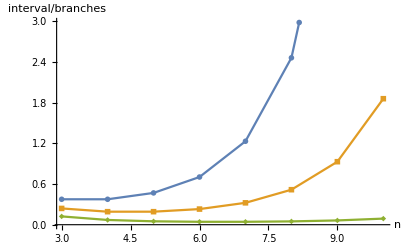

```mathematica
ListPlot[Drop[Table[Table[{n,(int/bra)},{n,3,10}],{km,3,6}],{-2}], AxesLabel->{"n","interval/branches"},PlotMarkers->{Automatic,Large}, Joined->True]
```

#### Timing for probK

In this example, calculating numerical values using a series expansion is much faster than direct differentiation with probK.  However, direct differentiation is slower for algebraic values.

Note: The example gf, sl, is calculated in the first single-deme example below

```mathematica
sl⟦1⟧
```

1/((6+ω[{a}]+ω[{b}]+ω[{c}]+ω[{d}]) (3+ω[{a}]+ω[{b}]+ω[{c,d}]) (1+ω[{a}]+ω[{b,c,d}]))

```mathematica
Timing[tbl=Array[probK[
DeleteCases[MapThread[If[#2==#3+1,Null,{#1,#2}]&,
{configs,{##},{3,3,3,3,3,3}}],Null],sl⟦1⟧,ω,0.2]&,{5,5,5,5,5,5},0];]
```

{3.61533,Null}

```mathematica
Timing[cl=Array[(0.1)^(Total[{##}]-1)&,{4,4,4,4,4,4},0]CoefficientList[Series[sl⟦1⟧/.{ω[x_List]:>(0.1-δ[x])},Sequence@@({δ[#],0,3}&/@configs)],δ/@configs];]
```

{0.44947,Null}

```mathematica
Timing[tbl=Array[probK[
DeleteCases[MapThread[If[#2==#3+1,Null,{#1,#2}]&,
{configs,{##},{3,3,3,3,3,3}}],Null],sl⟦1⟧,ω,θ]&,{5,5,5,5,5,5},0];]
```

{4.95011,Null}

```mathematica
Timing[cl=Array[(θ/2)^(Total[{##}]-1)&,{4,4,4,4,4,4},0]CoefficientList[Series[sl⟦1⟧/.{ω[x_List]:>(θ/2-δ[x])},Sequence@@({δ[#],0,3}&/@configs)],δ/@configs];]
```

{11.75333,Null}

#### Beyond infinite-sites: the Jukes-Cantor model

The notebook assumes infinite-sites mutation.  With deep coalescence events and high mutation rates, back-mutation needs to be considered. Probabilities can still be derived from the GF, but the number of mutational configurations becomes very large, unless some further simplification is made.

The probability of seeing j differences with n sites is (Eq. 2 of Lohse et al. 2011):

P[j]=(3/4)^n(n
j)∑_(k=0)^j ∑_(a=k)^(n-j+k) (-1)^k(1/3)^(n-j-a+k)(j
k)(n-j
a-k)ψ[μa]= (3/4)^n(n
j)∑_(a=0)^n (-9)^(a+j-n)(j
n-a-j)(2a+j-n
n-j)ψ[μa]

This calculation would be much faster than the infinite-sites version, since it involves a sum, rather than derivatives.  However, it would not be easy to calculate the full probability with multiple branches, since one would need to allow for multiple states - for example, the probability of seeing four different states on four leaves. It is not obvious whether mutational configurations could be simplified enough to allow them to be counted.

#### MakePT1

```mathematica
MakePT1::usage="MakePT1[GF,ω,θ,{{a},{b}},{k_(m, a),k_(m, b)}] uses a series expansion to make a table of mutation numbers {0,(…k)_m} for each listed branch. MakePT1[GF,ω,θ,{{a},…},{{a},{b},…},{k_(m, a),k_(m, b)}] makes a sub-table that sums over the branches in the first list, by setting those ω to 0.  This sub-table is embedded in the larger table with dimension {0(…k)_(m, a)+1,0(…k)_(m, b)+1,}, where the last element represents the residual probability. ";
```

```mathematica
MakePT1[gf_,ω_,θ_,sl_List,km_List]:=Module[{δ},
Array[(θ/2)^Total[{##}]&,km+1,0]PadRight[CoefficientList[Series[gf/.{ω[x_List]:>((θ/2)-δ[x])},Sequence@@MapThread[{δ[#1],0,#2}&,{sl,km}]],δ/@sl],km+1]];
```

```mathematica
MakePT1[gf_,ω_,θ_,zl_List,fl_List,km_List]:=
Module[{ss=TakeAway[fl,zl],rls=(ω[#]:>0)&/@zl,pos},
pos=Flatten[Position[fl,#]&/@ss];
EmbedTable[MakePT1[gf/.rls,ω,θ,ss,km⟦pos⟧],pos,km+2,km+2]];
```

#### MakePT

```mathematica
MakePT::usage="MakePT[GF,ω,θ,{{a},{b},…},{k_(m, a),k_(m, b)}] uses a series expansion to make a table of mutation numbers {0,(…k)_m} for each listed branch, and adds the residual probability to the last element in each row. Thus, each row runs from 0,…,k_m+1. Uses adjustTable to set the last element to the residual probability. Note: This appears no faster than direct differentiation, imlemented as the default in MakeProbTable.";
```

```mathematica
MakePT[gf_,ω_,θ_,fl_List,km_Integer]:=MakePT[gf,ω,θ,fl,ConstantArray[km,Length[fl]]];
MakePT[gf_,ω_,θ_,fl_List,km_List]:=
Module[{mt,nc=Length[fl],tot,rls=(ω[#]:>0)&/@fl},
tot=gf/.rls;
mt=Total[MakePT1[gf,ω,θ,#,fl,km]&/@Subsets[fl,{0,nc-1}]];
adjustTable[ReplacePart[mt,(km+2)->tot],nc]];
```

To implement an efficient method:
	- For a given set of ω, a subset will be zero, and the remainder will be used to make a series expansion
	- This set is embedded into a SparseArray with the full dimension
	- The full table is built up accordingly

To be flexible, I need to define an arbitrary list of branches that are distinguished, and that are the ω in the full GF.  The list of k_m must correspond to this list.  Any particular GF depends on a subset of these branches.  On this subset, I define sets of zeros; the remainder are used to make a full coefficient list.  This has to be slotted into the correct position in the full table.  However, because adjustTable is needed, it is best to first build the subtable, and then the full table.

Note: The next section shows that this method does not seem any faster than direct differentiation,

#### EmbedTable

```mathematica
EmbedTable::usage="EmbedTable[{{…},…},{i_1,…},{j_1,…},{d_1,…}] embeds the given table in a larger SparseArray with dimensions {d_1,…}. {i_1,…} lists the positions of the table dimensions in the larger SparseArray, and {j_1,…} lists the positions of the remaining dimensions.  For convenience, j has the same length as d, but the dimensions replaced by the embedded table are disregarded. EmbedTable[{{…},…},{i_1,…},1,{d_1,…}] uses the default position 1 for all dimensions.";
```

```mathematica
EmbedTable[tbl_List,i:{___Integer},j_Integer,d:{__Integer}]:=
EmbedTable[tbl,i,ConstantArray[j,Length[d]],d];
EmbedTable[tbl_List,i:{___Integer},j:{___Integer},d:{__Integer}]:=
Module[{xx,pl},
xx=IntegerSets[Dimensions[tbl]];(* all the entries that will be tabulated; {1,1,…}…{Subscript[d, 1],Subscript[d, 2],…} *)
pl=(ReplacePart[j,MapThread[Rule,{i,#}]])&/@xx;(* lists all the assignments that will be used to build the array *)
SparseArray[pl->Flatten[tbl],d]
(* builds a SparseArray with higher dimension d than the original table *)];
```

Example: The 2×3 table is embedded in a 3×4×3 SparseArray, using dimensions {1,3}, and inserting into position 2 of the remaining dimensions:

```mathematica
EmbedTable[{{a,b,bb},{c,d,dd}},{1,3},{0,2,0},{3,4,3}]//Normal
```

{{{0,0,0},{a,b,bb},{0,0,0},{0,0,0}},{{0,0,0},{c,d,dd},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}}}

#### IntegerSets

This is actually just a flattened Array[List,k]

```mathematica
IntegerSets::usage="IntegerSets[{k_1,k_2,…}] makes a flat list of all combinations of integers {i_1,i_2,…} for 1≤i≤k.   ";
```

```mathematica
IntegerSets[k:{__Integer}]:=Flatten[Array[List,k],Length[k]-1];
```

#### MakeProbTableOnce

```mathematica
MakeProbTableOnce::usage="MakeProbTableOnce[{{ψ,…},…},ω[{a,b}],θ,k_max] is used by MakeProbTable[] to construct a table of probabilities of all mutational configurations.  It takes a GF, or a GF that has already been differentiated to give a partial table, and constructs a series expansion in ω[{a,b}] around θ/2.  Tabulates 0(…k)_max itations, and adds a final element that gives the residual probability.";
```

```mathematica
MakeProbTableOnce[gf_,ω_,θ_,km_Integer]:=Module[{cl,δ,tr=TensorRank[gf]},
If[tr==0,cl=(θ/2)^Range[0,km] PadRight[CoefficientList[Series[gf/.ω:>(θ/2-δ),{δ,0,km}],δ],km+1];
Append[cl,(gf/.ω:>0)-Total[cl]] (* appends the residual probability *),
Map[MakeProbTableOnce[#,ω,θ,km]&,gf,{tr}]
(* if gf is a table, applies the function to the deepest level *)]];
```

#### Comparing direct differentiation with a series expansion

There are two alternative methods: direct differentiation using probK, and another method using a series expansion.  Surprisingly, the series expansion is much slower when θ is given numerically.  This contrasts with the check above (see under probK), because here, I use MakeTableOnce to find the residual probability.  It seems that a series expansion will give numerical values faster, but I have not found a way to use this efficiency when the residual probabilities are calculated.

Note: The example gf, sl, is calculated in the first single-deme example below

```mathematica
sl2=1/((6+ω[{a}]+ω[{b}]+ω[{c}]+ω[{d}]) (3+ω[{a}]+ω[{c}]+ω[{b,d}]) (1+ω[{a}]+ω[{b,c,d}]));
```

```mathematica
br=Subsets[{a,b,c,d},{1,3}];
```

```mathematica
Timing[tblNew=MakeProbTable[sl2,ω,0.2,br,3,OldMethod->False];]
```

{28.6378,Null}

```mathematica
Timing[tblOld=MakeProbTable[sl2,ω,0.24,br,3];]
```

{4.55628,Null}

When θ is kept as a symbol, the series expansion fails altogether.  The direct method using probK is much slower:

```mathematica
Timing[tblNewθ=MakeProbTable[sl2,ω,θ,br,3,OldMethod->False];]
```

$Aborted

```mathematica
Timing[tblOldθ=MakeProbTable[sl2,ω,θ,br,3];]
```

{8.73943,Null}

The two methods do agree:

```mathematica
{18Total[#//Flatten]&/@{tblNew,tblOld,tblOldθ/.θ->0.2},{Min[tblNew-tblOld//Flatten],Max[tblNew-tblOld//Flatten]}}
```

{{1.,1.,1},{-5.83437×10^-14,6.53337×10^-14}}

Note:  It may take an unreasonably long time to replace θ by a numerical value. The above expression is fast, but Min[tblNew-(tblOldθ/.θ→0.2)] fails, for obscure reasons.  It may be that Mathematica sometimes tries to convert a SparseArray into an enormous normal expression.

```mathematica
Timing[tblSeriesθ=MakePT[sl2,ω,θ,GetConfigsGF[sl2,ω],3];]
```

{42.35534,Null}

```mathematica
Timing[tblSeries=MakePT[sl2,ω,0.2,GetConfigsGF[sl2,ω],3];]
```

{5.28017,Null}

MakeProbTable generates a big array, in this example with 14 dimensions.  To compare the values, the output fromMakePT must be embedded into a table with the same dimensions.

```mathematica
tblSeriesBig=EmbedTable[tblSeries//Normal,{1,2,3,4,9,14},1,ConstantArray[5,14]]
```

SparseArray[<15625>, {5, 5, 5, 5, 5, 5, 5, 5, 5, 5, 5, 5, 5, 5}]

Miraculously, the new method gives the correct values:

```mathematica
{Min[tblSeriesBig-tblOld//Flatten],Max[tblSeriesBig-tblOld//Flatten]}
```

{-7.62259×10^-17,7.23105×10^-17}

Summary: Three methods are implemented: direct differentiation (the default OldMethod->True in MakeProbTable); series expansion (OldMethod->True in MakeProbTable); and a more efficient series expansion scheme in MakePT.   The latter has about the same speed as direct differentiation for numerical θ, but is much slower for algebraic expressions.  However, I have not tested it extensively.

### Setting up tables of probabilities: main functions

#### likFullG

```mathematica
likFullG::usage="likFullG[gf,ω,θ,rlznum,max] uses CoefficeintList to tabulate the probabilities of mutational configurations of to max mutations. By default the table of probabilities has the same dimensions as the list of ω of the gf. However a specific subset of ωs can be specified in ωlist (other ω parameteres are then set to 0). If ωlist is empty likFullG computes the marginal probability";
```

```mathematica
likFullG[gf_,ω_,θ_,rlznum_List,max_Integer]:=likFullG[gf,ω,θ,rlznum, ConstantArray[max,GetConfigsGF[gf,ω]//Length]];
```

```mathematica
likFullG[gf_,ω_,θ_,rlznum_List, max_List]:=
likFullG[gf,ω,θ,rlznum,GetConfigsGF[gf,ω]//Sort,max];
```

```mathematica
likFullG[gf_,ω_,θ_,rlznum_List,ωlist_,max_Integer]:=likFullG[gf,ω,θ,rlznum,ωlist,ConstantArray[max,Length[ωlist]]];
```

```mathematica
likFullG[gf_,ω_,θ_,rlznum_List,ωlist_,max_List]:=Module[{rules, nc,δs,δsmax,δ},
rules=(ω[#]:>θ/2-δ[#])&/@ωlist;
nc=ωlist//Length;
δs=δ[#]&/@ωlist;
δsmax={#⟦1⟧,0,#⟦2⟧}&/@({δs,max}//Thread);

N[(If[ωlist=={},gf/.rlznum/.ω[_]->0,CoefficientList[(Series[gf/.rlznum/.rules/.ω[_]->0,##]&@@δsmax),δs]]×
Array[(θ/2)^Total[{##}]&,max+1,ConstantArray[0,nc]]),Infinity]];
```

Note: There is a peculiar singularity at θ=2; the likelihood calculation blows up at this value.

```mathematica
likFullG[twoEnRXTsimpSort⟦2⟧//Total,ω,2,{M->0,T->1.7},{},3]
```

Part::partd: Part specification twoEnRXTsimpSort ⟦ 2 ⟧ is longer than depth of object.

2+twoEnRXTsimpSort

#### probK

```mathematica
probK::usage="probK[{{{a},2},{{{b,c},3},…},ψ,ω,θ] gives the probability of 2 mutations ancestral to {a}, and 3 to {b,c}. If arguments are omitted, then the probability is summed over these classes.  If a table of all the probabilities is needed, it is more efficient to use MakeProbTable[].";
```

```mathematica
probK[skl:{{_List,_Integer}...},ψ_,ω_,θ_]:=Module[{kl,rls},
rls=(ω[#⟦1⟧]->θ/2)&/@skl;
kl=Last/@skl;
(-θ/2)^Total[kl]/(Times@@(kl!))(D[ψ,Sequence@@(skl/.{s_List,k_Integer}:>{ω[s],k})]/.rls/.{ω[_]:>0})];
```

Note: probK calculates the probability of a configuration k by differentiating k times. If a full table of probabilities is needed, then it might be more efficient to use Mathematica’s built-in series expansion, and extract the coefficients.  However, this is not straightforward.

#### MakeProbTable

```mathematica
MakeProbTable::usage="MakeProbTable[GF,ω,θ,branches,{k_(m, 1),…}] generates a sparse array that gives the probability of each possible mutation type. MakeProbTable[{GF,…},ω,θ,branches,{k_(m, 1),…}] generates a list of tables, all with the same dimensions. Generates a large sparse array, with dimensions ∏(2+k_(max, i)), where k_m defines the maximum number of mtations that are counted.  The last entry in each column gives the residual probability - that is, the index runs {0,,1,…,k_max,residual}.  This is calculated using adjustTable.  The table is arranged in the same order as the list of branches that is supplied. Replacing {k_(m, 1),…} by an integer, k_m, sets the same maximum number of loci across all branches. OldMethod→False] is a slower version that uses a series expansion rather than the default option of direct differentiation.";
```

```mathematica
OldMethod::usage="OldMethod is an option for MakeProbTable; OldMethod→False specifies that a series expansion, raher than direct differentiation using probK should be used (the default).";
```

```mathematica
Options[MakeProbTable]={OldMethod->True};
```

```mathematica
MakeProbTable::badList="The list `1` of maximum numbers of mutations must have length equal to the list of branches, `2`.";
```

```mathematica
MakeProbTable::badBranches="The branches represented in the GF, `1` are not a subset of the supplied list of brancheslist of branches, `2`.";
```

```mathematica
MakeProbTable[gf_,ω_,θ_,branches_List,km_Integer,opts___Rule]:=
MakeProbTable[gf,ω,θ,branches,ConstantArray[km,Length[branches]],opts];
MakeProbTable[gf_,ω_,θ_,branches_List,km:{__Integer},opts___Rule]:=
If[ListQ[gf],MakeProbTable[#,ω,θ,branches,km,opts]&/@gf,
Module[{configs=GetConfigsGF[gf,ω],posn,nc,tt},
If[Length[km]≠Length[branches],Message[MakeProbTable::badList,km,branches]];
If[!SubsetQ[branches,configs],Message[MakeProbTable::badBranches,configs,branches]];
posn=Flatten[Position[branches,#]&/@configs];
tt=If[OldMethod/.{opts}/.Options[MakeProbTable],
nc=Length[configs];(* number of configurations that appear in this GF *)
adjustTable[
Array[probK[
DeleteCases[MapThread[If[#2==#3+1,Null,{#1,#2}]&,
{configs,{##},km⟦posn⟧}],Null],gf,ω,θ]&,km⟦posn⟧+2,0],nc],
Fold[MakeProbTableOnce[#1,ω[#2⟦1⟧],θ,#2⟦2⟧]&,gf,Transpose[{configs,km⟦posn⟧}]]];EmbedTable[tt,posn,1,km+2]]];
```

#### configList

```mathematica
configList::usage="configList[t,k_max] generates a list of mutational configurations for a given list of maximum # of mutations per branch category, and a list of the position of each branch category. Used in likFullTab.";
```

```mathematica
configList[t_List,inc_,kmax_List]:=Module[{ll=Length[t],max=kmax⟦t⟧,cons,int},
If[t=={},{ReplacePart[kmax+1,(#->0)&/@inc]},
cons=ConstantArray[kmax+1,Times@@(max+1)];int=Flatten[Array[{##}&,max+1,ConstantArray[0,ll]],ll-1];ReplacePart[#,(#->0)&/@inc]&/@Table[ReplacePart[cons⟦k⟧,Table[t⟦i⟧->int⟦k,i⟧,{i,1,ll}]],{k,Length[int]}]]]
```

#### likFullTab

```mathematica
likFullTab::usage="likFullTab[GF,ω,θ,{m->m1,T1->t1...},k_max_List] generates a sparse array that gives the probability of k_i of each possible mutation type. The input is a nested list of GF terms, each corresponding to a different equivalence class. The list k_max gives the maximum number of mutations on each branch type. The output has dimensions Times@@(2+k_max). The number of branch types that the GF distinguishes (which must match the length of k_max) defines the number of types of mutations. The last entry in each column gives the residual probability - that is, the index runs {0,1,…,k_max,residual}.  This is calculated using adjustTable.  The table is arranged in the same order as the list of ω indices of the GF. likFullTab works regardless of whether the ω variables of the GF correpsond to rooted branches or to combinations of branches.";
```

```mathematica
likFullTab[gf_,ω_,θ_,rlznum_List,max_Integer]:=likFullTab[gf,ω,θ,rlznum,ConstantArray[max,GetConfigsGF[Total[gf],ω]//Length]];
```

```mathematica
likFullTab[gf_,ω_,θ_,rlznum_List,max_List]:=Module[{ngf,ωs,ωslen,ωsall,posωs,ncall,ωssub,incomp,posnincomp,maxsub,posn,liktab,pl,tbl},
ngf=Length[gf];
ωs=GetConfigsGF[#,ω]&/@gf(* number of configurations that appear in the GF for each equivalence class *);
ωslen=Length[#]&/@ωs(* number of ω terms in each equivalence class*);
ωsall=Flatten[ωs,1]//Union//Sort(* the total list of ω terms*);
posωs=Table[Flatten[Position[ωsall,#]&/@ωs⟦i⟧],{i,1,ngf}] ;
ncall=Length[ωsall];
ωssub=(Table[Subsets[#,{n}],{n,0,Length[#]}])&/@ωs;
incomp=Complement[ωsall,#]&/@ωs;
posnincomp=Table[Flatten[Position[ωsall,#]&/@incomp⟦i⟧],{i,1,ngf}] (* the position of incompatible branches. Needs testing for cases with multiple incompatible branches*);
posn=Table[Table[Flatten[Position[ωsall,#]&/@ωssub⟦i,k,o⟧],{o,1,Length[ωssub⟦i,k⟧]}],{i,1,ngf},{k,1,ωssub⟦i⟧//Length}](* pos'ns of the ω terms of each equivalence class in ωsall*);
liktab=Table[(likFullG[Flatten[gf⟦i⟧],ω,θ,rlznum,#⟦1⟧,max⟦#⟦2⟧⟧]&/@({ωssub⟦i,k⟧,posn⟦i,k⟧}//Thread)),{i,1,ngf},{k,1,ωssub⟦i⟧//Length}];
pl=Table[Flatten[Table[configList[#,posnincomp⟦i⟧,max]&/@posn⟦i,k⟧,{k,1,Length[ωssub⟦i⟧]}],2],{i,1,ngf}](* all the numbers of mutations that will be tabulated; {0,0,…}…{Subscript[k, max]+1,Subscript[k, max]+1,…} *);tbl=Table[SparseArray[(1+pl⟦i⟧)->Flatten[liktab⟦i⟧],max+2],{i,1,ngf}];Table[Fold[adjustTable[#1,ncall,#2]&,tbl⟦i⟧,posωs⟦i⟧],{i,1,ngf}]//Total];
```

#### totallnL

```mathematica
totallnL[gf_,ω_,θ_?NumberQ,rlznum_List,max_List,counts_SparseArray]:=Module[{probTab,posn},probTab=likFullTab[gf,ω,θ,rlznum,max];
posn=probTab["NonzeroPositions"];Total[Log[probTab["NonzeroValues"]]*(Extract[counts,#]&/@posn)]];
```

```mathematica
totallnL[gf_,ω_,θ_?NumberQ,rlznum_List,max_Integer,counts_SparseArray]:=totallnL[gf,ω,θ,rlznum,ConstantArray[max,GetConfigsGF[Total[gf],ω]//Length],counts];
```

#### adjustTable

```mathematica
adjustTable::usage="adjustTable[{{…},…},d] takes a table with dimension d in which the last element at each level is the total probability, and produces a table in which the last element is the residual probability.  This new table should sum to 1. adjustTable[{{…},…},d,k] makes the adjustment only for level k.  Note that d cannot be inferred from the depth of the table, because its elements may themselves have depth. Works with sparse arrays.";
```

```mathematica
adjustTable[t:(_List|_SparseArray),d_Integer,k_Integer]:=Module[{jj,nt},
jj=RotateRight[Range[d],k-1];nt=Transpose[t,jj];
Transpose[ReplacePart[nt,-1->(nt⟦-1⟧-Total[Drop[nt,-1]])],Normal[SparseArray[jj->Range[d]]]]];
```

```mathematica
adjustTable[t:(_List|_SparseArray),d_Integer]:=Module[{nt=t,j},
Do[nt=adjustTable[nt,d,j],{j,d}];nt];
```

```mathematica
adjustTable[t:(_List|_SparseArray),d_Integer,k_Integer]:=Module[{jj,nt},
jj=RotateRight[Range[d],k-1];nt=Transpose[t,jj];
Transpose[ReplacePart[nt,-1->(nt⟦-1⟧-Total[Drop[nt,-1]])],Normal[SparseArray[jj->Range[d]]]]];
```

```mathematica
?Transpose
```

RowBox[{"Transpose", "[", StyleBox["list", "TI"], "]"}] transposes the first two levels in StyleBox["list", "TI"]. 
RowBox[{"Transpose", "[", RowBox[{StyleBox["list", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] transposes StyleBox["list", "TI"] so that the StyleBox["k", "TI"]SuperscriptBox["", "th"] level in StyleBox["list", "TI"] is the SubscriptBox[StyleBox["n", "TI"], StyleBox["k", "TI"]]SuperscriptBox["", "th"] level in the result.

```mathematica
Transpose[ReplacePart[nt,-1->(nt⟦-1⟧-Total[Drop[nt,-1]])],Normal[SparseArray[jj->Range[d]]]]
```

Part::partd: Part specification nt ⟦ -1 ⟧ is longer than depth of object.

Drop::normal: Nonatomic expression expected at position 1 in Drop[nt, -1].

Range::range: Range specification in Range[d] does not have appropriate bounds.

SparseArray::pos: The left-hand side of jj → Range[d] in {jj → Range[d]} is not a position or pattern that will match a position.

Transpose::list: List expected at position 2 in nt, TagBox[SparseArray[jj → Range[d]], False, Rule[Editable, False], Rule[SelectWithContents, True]].

Transpose[nt,SparseArray[jj→Range[d]]]

```mathematica
ReplacePart[nt,-1->(nt⟦-1⟧-Total[Drop[nt,-1]])]
```

Part::partd: Part specification nt ⟦ -1 ⟧ is longer than depth of object.

Drop::normal: Nonatomic expression expected at position 1 in Drop[nt, -1].

nt

```mathematica
{4,1,2,3}->Range[4]
```

{4,1,2,3}→{1,2,3,4}

```mathematica
SparseArray[{4,1,2,3}->{1,2,3,4}]
```

SparseArray[<4>, {4}]

```mathematica
Normal[SparseArray[{4,1,2,3}->Range[4]]]
```

{2,3,4,1}

```mathematica
RotateRight[Range[4],2-1]
```

{4,1,2,3}

#### Comparing MakeProbTable with likFullTab and MakePT

```mathematica
branch1=GetConfigsGF[twoEnRXTsimpSort⟦1⟧,ω];
branchall=GetConfigsGF[twoEnRXTsimpSort,ω];
```

It is unclear to me why likFullTab is more efficient than MakeProbTable. This tabulates probabilities under a strict divergence model with a global k_max=3 for blocks with fixed differences only.

```mathematica
AbsoluteTiming[ttKL1=likFullTab[{twoEnRXTsimpSort⟦1⟧//Flatten//Total},ω,2.48,{M->0.2,T->0.37},{3,3,3}];]
```

{5.16424,Null}

The default method used in MakeProbTable is much slower:

```mathematica
AbsoluteTiming[ttNB1=MakeProbTable[(twoEnRXTsimpSort⟦1⟧//Flatten//Total)/.{M->0.2,T->0.37},ω,2.48,branch1,3];]
```

{58.5771,Null}

Using Series expansion in MakeProbTable is almost as fast as likFullTab. I do not understand the difference between these  two functions ...

```mathematica
AbsoluteTiming[ttNB1b=MakeProbTable[(twoEnRXTsimpSort⟦1⟧//Flatten//Total)/.{M->0.2,T->0.37},ω,2.48,branch1,3,OldMethod->False];]
```

Part::partd: Part specification twoEnRXTsimpSort ⟦ 1 ⟧ is longer than depth of object.

{0.043464,Null}

Both schemes give the same answer:

```mathematica
SetPrecision[Chop[(ttNB1-ttKL1)//Normal],2]//TableForm
```

MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}] | MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}] | MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}] | MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}] | MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}] | MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}] | MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}] | MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}] | MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}] | MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}] | MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}] | MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}] | MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}] | MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}] | MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}] | MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}] | MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}] | MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}] | MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}] | MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}] | MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]
-1. (1.+twoEnRXTsimpSort)+MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]

but maybe differ in rounding error :

```mathematica
(ttNB1//Normal)-(ttKL1//Normal)//TableForm
```

MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}] | MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}] | MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}] | MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}] | MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}] | MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}] | MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}] | MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}] | MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}] | MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}] | MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}] | MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}] | MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}] | MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}] | MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}] | MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}] | MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}] | MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}] | MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}] | MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}] | MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]
-1. (1+twoEnRXTsimpSort)+MakeProbTable[1+twoEnRXTsimpSort,ω,2.48,{},{}]

```mathematica
Total[Flatten[#]]&/@{ttNB1,ttKL1}
```

{{},1. (1+twoEnRXTsimpSort)}

#### Comparing likFullTab with the old scheme

The probabilities of full configurations agree:

```mathematica
klOLD=quadfullNum[{2.43,0.37,0},3];
```

```mathematica
SetPrecision[klOLD⟦1,1⟧,2]//TableForm
```

2.4

```mathematica
klNEW=likFullTab[{twoEnRXTsimpSort⟦1⟧//Flatten//Total},ω,2.43,{M->0,T->0.37},{3,3,3}];
```

Part::partd: Part specification twoEnRXTsimpSort ⟦ 1 ⟧ is longer than depth of object.

```mathematica
SetPrecision[Transpose[klNEW⟦1;;4,1;;4,1;;4⟧,{2,3,1}],2]//TableForm
```

0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
0
0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
0
0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
0
0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
0

```mathematica
SetPrecision[Transpose[ttNB1⟦1;;4,1;;4,1;;4⟧,{2,3,1}],2]//TableForm
```

Part::take: Cannot take positions 1 through 4 in 1 + twoEnRXTsimpSort.

Part::take: Cannot take positions 1 through 4 in 1. + twoEnRXTsimpSort.

Transpose[MakeProbTable[1.+twoEnRXTsimpSort,ω,2.5,{},{}]⟦1;;4,1;;4,1;;4⟧,{2.,3.,1.}]

The residual probs for AA_BB topologies also agree:

```mathematica
SetPrecision[oldD2=klOLD⟦2,1⟧,2]//TableForm
```

Part::partd: Part specification quadfullNum[{2.43, 0.37, 0}, 3] ⟦ 2, 1 ⟧ is longer than depth of object.

Part::partd: Part specification quadfullNum[{2.4, 0.37, 0}, 3.] ⟦ 2, 1 ⟧ is longer than depth of object.

quadfullNum[{2.4,0.37,0},3.]⟦2,1⟧

```mathematica
SetPrecision[newD2={Drop[#,-1]&/@Drop[Transpose[klNEW,{2,3,1}]⟦-1⟧,-1],Drop[#,-1]&/@Drop[klNEW⟦-1⟧,-1],Drop[#,-1]&/@Drop[Transpose[klNEW,{3,1,2}]⟦-1⟧,-1]}//Normal,2]//TableForm
```

0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
0
0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
0
0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
0

```mathematica
SetPrecision[oldD1={klOLD⟦3,1⟧},2]//TableForm
```

Part::partw: Part 3 of quadfullNum[{2.43, 0.37, 0}, 3] does not exist.

Part::partw: Part 3 of quadfullNum[{2.4, 0.37, 0}, 3.] does not exist.

quadfullNum[{2.4,0.37,0},3.]⟦3,1⟧

```mathematica
SetPrecision[newD1={Transpose[klNEW,{2,3,1}]⟦-1,-1⟧,klNEW⟦-1,-1⟧,Transpose[klNEW,{3,1,2}]⟦-1,-1⟧}//Normal,2]//TableForm
```

0 | 0 | 0 | 0 | 1. (1.+twoEnRXTsimpSort)
0 | 0 | 0 | 0 | 1. (1.+twoEnRXTsimpSort)
0 | 0 | 0 | 0 | 1. (1.+twoEnRXTsimpSort)

### Simplifying genealogies

### Making simulated data

#### makeSample

```mathematica
makeSample::usage="makeSample[probs,n] draws n random samples according to the table of probabilities, and tabulates them in a sparse array that has the same form as the supplied table of probabilities.  probs may be a list or a sparse array.";
```

```mathematica
makeSample[pt:(_SparseArray|_List),n_]:=Module[{rls=ArrayRules[pt]},
SparseArray[(#⟦1⟧->#⟦2⟧)&/@Tally[RandomChoice[rls⟦All,2⟧->(rls⟦All,1⟧),n]]]];
```

### Summarising real data

#### replaceMax

```mathematica
replaceMax::usage="replaceMax[l_List,{max_,pos_}] replaces mutation counts > k_max with k_max+1. This function is needed for configcounts. ";
```

```mathematica
replaceMax[l_List,{max_,pos_}]:=Join[ReplacePart[#,pos->max+1]&/@(Select[l,#⟦pos⟧>max&]),Select[l,#⟦pos⟧⩽max&]];
```

#### configCounts

Note: configcounts works for arbitrary sample sizes. It is worthwhile to do this data summarizing step outside of Mathematica when dealing with large datasets or counting mutational configurations repeatedly, e.g. in sliding windows.

```mathematica
configCounts::usage="configcounts[l,max] counts blockwise mutational configurations for arbitrary number of mutation types. The input is a list of counts of those types in all blocks which should have the same ordering as the sorted list of ω terms of the GF. max is either a list of maxima or a single global maximum for all mutation types";
```

```mathematica
configCounts[l_List,max_List]:=Module[{ll=Length[max],r,truncl,maxt=max+1,counts},
r={max,Range[1,ll]}//Thread;truncl=Fold[replaceMax[#1,#2]&,l,r];
counts=((#⟦1⟧+1)->#⟦2⟧)&/@Tally[truncl];
SparseArray[counts,max+2]];
```

```mathematica
configCounts[l_List,max_Integer]:=configCounts[l,ConstantArray[max,Length[l⟦1⟧]]];
```

#### FindkMax

Note: Hard coded for 4 types, need to generalize to any # of branch types.

```mathematica
FindkMax::usage="For a given threshold p and a dataset consiting of a list of blockwise counts l, FindkMax[l,p] gives the kmax for each branch type such that (%l >k_max)<p. The output is a vector of kmax values and the total fraction of blocks > k_max.";
```

```mathematica
FindkMax[l_List,p_]:=Module[{ll=l⟦1⟧//Length,cond,kmax},
cond=Table[Sort[Select[(#⟦i⟧)&/@l,#>0&]],{i,1,ll}];kmax=Table[cond⟦i,-Round[Length[cond⟦i⟧]*p]⟧,{i,1,ll}];{kmax,(Select[l,#⟦1⟧>kmax⟦1⟧||#⟦2⟧>kmax⟦2⟧||#⟦3⟧>kmax⟦3⟧||#⟦4⟧>kmax⟦4⟧&]//Length)/(l//Length)//N}]
```

# Project North American Canids

## IUA models

We are modelling coalescent events backwards in time. The first event is represented by a single pulse of admixture with probability f. 
The second an third event are modelled in the same way but with probability 1 because they represent speciation.
We can always  build a simpler Divergence Model by setting the first pulse to zero.
We assume that  population Y and Z are sister species and X is  either the  Donor or the Recipient population involved in the Admixture pulse.

```mathematica
var3= ψ[ω,{{{a}},{{b}},{{c}}},{{X},{Y},{Z}},Admixture->{{Subscript[A, 1],Subscript[a, 1]},{Subscript[A, 2],Subscript[a, 2]},{Subscript[A, 3],Subscript[a, 3]}}];
```

### Model 1: admixture X → Y

```mathematica
rlz={Subscript[a, 1][{X},{Y}]->f,Subscript[a, 1][{X},{Z}]->0,Subscript[a, 1][{Y},{X}]->0,Subscript[a, 1][{Y},{Z}]->0,Subscript[a, 1][{Z},{X}]->0,Subscript[a, 1][{Z},{Y}]->0,
Subscript[a, 2][{X},{Y}]->0,Subscript[a, 2][{X},{Z}]->0,Subscript[a, 2][{Y},{X}]->0,Subscript[a, 2][{Y},{Z}]->1,Subscript[a, 2][{Z},{X}]->0,Subscript[a, 2][{Z},{Y}]->0,
Subscript[a, 3][{X},{Y}]->0,Subscript[a, 3][{X},{Z}]->0,Subscript[a, 3][{Y},{X}]->1,Subscript[a, 3][{Y},{Z}]->0,Subscript[a, 3][{Z},{X}]->0,Subscript[a, 3][{Z},{Y}]->0,
Subscript[A, 1][{X},{Y}]->ADM,Subscript[A, 1][{X},{Z}]->0,Subscript[A, 1][{Y},{X}]->0,Subscript[A, 1][{Y},{Z}]->0,Subscript[A, 1][{Z},{X}]->0,Subscript[A, 1][{Z},{Y}]->0,
Subscript[A, 2][{X},{Y}]->0,Subscript[A, 2][{X},{Z}]->0,Subscript[A, 2][{Y},{X}]->0,Subscript[A, 2][{Y},{Z}]->A2,Subscript[A, 2][{Z},{X}]->0,Subscript[A, 2][{Z},{Y}]->0,
Subscript[A, 3][{X},{Y}]->0,Subscript[A, 3][{X},{Z}]->0,Subscript[A, 3][{Y},{X}]->A3,Subscript[A, 3][{Y},{Z}]->0,Subscript[A, 3][{Z},{X}]->0,Subscript[A, 3][{Z},{Y}]->0};
```

Just a double check about the direction of merging maintaining the same topology

```mathematica
rlz2={Subscript[a, 1][{X},{Y}]->f,Subscript[a, 1][{X},{Z}]->0,Subscript[a, 1][{Y},{X}]->0,Subscript[a, 1][{Y},{Z}]->0,Subscript[a, 1][{Z},{X}]->0,Subscript[a, 1][{Z},{Y}]->0,
Subscript[a, 2][{X},{Y}]->0,Subscript[a, 2][{X},{Z}]->0,Subscript[a, 2][{Y},{X}]->0,Subscript[a, 2][{Y},{Z}]->0,Subscript[a, 2][{Z},{X}]->0,Subscript[a, 2][{Z},{Y}]->1,
Subscript[a, 3][{X},{Y}]->0,Subscript[a, 3][{X},{Z}]->1,Subscript[a, 3][{Y},{X}]->0,Subscript[a, 3][{Y},{Z}]->0,Subscript[a, 3][{Z},{X}]->0,Subscript[a, 3][{Z},{Y}]->0,
Subscript[A, 1][{X},{Y}]->ADM,Subscript[A, 1][{X},{Z}]->0,Subscript[A, 1][{Y},{X}]->0,Subscript[A, 1][{Y},{Z}]->0,Subscript[A, 1][{Z},{X}]->0,Subscript[A, 1][{Z},{Y}]->0,
Subscript[A, 2][{X},{Y}]->0,Subscript[A, 2][{X},{Z}]->0,Subscript[A, 2][{Y},{X}]->0,Subscript[A, 2][{Y},{Z}]->0,Subscript[A, 2][{Z},{X}]->0,Subscript[A, 2][{Z},{Y}]->A2,
Subscript[A, 3][{X},{Y}]->0,Subscript[A, 3][{X},{Z}]->A3,Subscript[A, 3][{Y},{X}]->0,Subscript[A, 3][{Y},{Z}]->0,Subscript[A, 3][{Z},{X}]->0,Subscript[A, 3][{Z},{Y}]->0};
```

### Model 2: admixture Y → X

```mathematica
rulz={Subscript[a, 1][{X},{Y}]->0,Subscript[a, 1][{X},{Z}]->0,Subscript[a, 1][{Y},{X}]->f,Subscript[a, 1][{Y},{Z}]->0,Subscript[a, 1][{Z},{X}]->0,Subscript[a, 1][{Z},{Y}]->0,
Subscript[a, 2][{X},{Y}]->0,Subscript[a, 2][{X},{Z}]->0,Subscript[a, 2][{Y},{X}]->0,Subscript[a, 2][{Y},{Z}]->1,Subscript[a, 2][{Z},{X}]->0,Subscript[a, 2][{Z},{Y}]->0,
Subscript[a, 3][{X},{Y}]->0,Subscript[a, 3][{X},{Z}]->0,Subscript[a, 3][{Y},{X}]->1,Subscript[a, 3][{Y},{Z}]->0,Subscript[a, 3][{Z},{X}]->0,Subscript[a, 3][{Z},{Y}]->0,
Subscript[A, 1][{X},{Y}]->0,Subscript[A, 1][{X},{Z}]->0,Subscript[A, 1][{Y},{X}]->ADM,Subscript[A, 1][{Y},{Z}]->0,Subscript[A, 1][{Z},{X}]->0,Subscript[A, 1][{Z},{Y}]->0,
Subscript[A, 2][{X},{Y}]->0,Subscript[A, 2][{X},{Z}]->0,Subscript[A, 2][{Y},{X}]->0,Subscript[A, 2][{Y},{Z}]->A2,Subscript[A, 2][{Z},{X}]->0,Subscript[A, 2][{Z},{Y}]->0,
Subscript[A, 3][{X},{Y}]->0,Subscript[A, 3][{X},{Z}]->0,Subscript[A, 3][{Y},{X}]->A3,Subscript[A, 3][{Y},{Z}]->0,Subscript[A, 3][{Z},{X}]->0,Subscript[A, 3][{Z},{Y}]->0};
```

Just another sanity check on the direction of merging

```mathematica
rulz2={Subscript[a, 1][{X},{Y}]->0,Subscript[a, 1][{X},{Z}]->0,Subscript[a, 1][{Y},{X}]->f,Subscript[a, 1][{Y},{Z}]->0,Subscript[a, 1][{Z},{X}]->0,Subscript[a, 1][{Z},{Y}]->0,
Subscript[a, 2][{X},{Y}]->0,Subscript[a, 2][{X},{Z}]->0,Subscript[a, 2][{Y},{X}]->0,Subscript[a, 2][{Y},{Z}]->0,Subscript[a, 2][{Z},{X}]->0,Subscript[a, 2][{Z},{Y}]->1,
Subscript[a, 3][{X},{Y}]->0,Subscript[a, 3][{X},{Z}]->1,Subscript[a, 3][{Y},{X}]->0,Subscript[a, 3][{Y},{Z}]->0,Subscript[a, 3][{Z},{X}]->0,Subscript[a, 3][{Z},{Y}]->0,
Subscript[A, 1][{X},{Y}]->0,Subscript[A, 1][{X},{Z}]->0,Subscript[A, 1][{Y},{X}]->ADM,Subscript[A, 1][{Y},{Z}]->0,Subscript[A, 1][{Z},{X}]->0,Subscript[A, 1][{Z},{Y}]->0,
Subscript[A, 2][{X},{Y}]->0,Subscript[A, 2][{X},{Z}]->0,Subscript[A, 2][{Y},{X}]->0,Subscript[A, 2][{Y},{Z}]->0,Subscript[A, 2][{Z},{X}]->0,Subscript[A, 2][{Z},{Y}]->A2, 
Subscript[A, 3][{X},{Y}]->0,Subscript[A, 3][{X},{Z}]->A3,Subscript[A, 3][{Y},{X}]->0,Subscript[A, 3][{Y},{Z}]->0,Subscript[A, 3][{Z},{X}]->0,Subscript[A, 3][{Z},{Y}]->0};
```

### Model 3: admixture X → Z

```mathematica
rula={Subscript[a, 1][{X},{Y}]->0,Subscript[a, 1][{X},{Z}]->f,Subscript[a, 1][{Y},{X}]->0,Subscript[a, 1][{Y},{Z}]->0,Subscript[a, 1][{Z},{X}]->0,Subscript[a, 1][{Z},{Y}]->0,
Subscript[a, 2][{X},{Y}]->0,Subscript[a, 2][{X},{Z}]->0,Subscript[a, 2][{Y},{X}]->0,Subscript[a, 2][{Y},{Z}]->1,Subscript[a, 2][{Z},{X}]->0,Subscript[a, 2][{Z},{Y}]->0,
Subscript[a, 3][{X},{Y}]->0,Subscript[a, 3][{X},{Z}]->0,Subscript[a, 3][{Y},{X}]->1,Subscript[a, 3][{Y},{Z}]->0,Subscript[a, 3][{Z},{X}]->0,Subscript[a, 3][{Z},{Y}]->0,
Subscript[A, 1][{X},{Y}]->0,Subscript[A, 1][{X},{Z}]->ADM,Subscript[A, 1][{Y},{X}]->0,Subscript[A, 1][{Y},{Z}]->0,Subscript[A, 1][{Z},{X}]->0,Subscript[A, 1][{Z},{Y}]->0,
Subscript[A, 2][{X},{Y}]->0,Subscript[A, 2][{X},{Z}]->0,Subscript[A, 2][{Y},{X}]->0,Subscript[A, 2][{Y},{Z}]->A2,Subscript[A, 2][{Z},{X}]->0,Subscript[A, 2][{Z},{Y}]->0,
Subscript[A, 3][{X},{Y}]->0,Subscript[A, 3][{X},{Z}]->0,Subscript[A, 3][{Y},{X}]->A3,Subscript[A, 3][{Y},{Z}]->0,Subscript[A, 3][{Z},{X}]->0,Subscript[A, 3][{Z},{Y}]->0};
```

### Model 4: admixture Z → X

```mathematica
rulla={Subscript[a, 1][{X},{Y}]->0,Subscript[a, 1][{X},{Z}]->0,Subscript[a, 1][{Y},{X}]->0,Subscript[a, 1][{Y},{Z}]->0,Subscript[a, 1][{Z},{X}]->f,Subscript[a, 1][{Z},{Y}]->0,
Subscript[a, 2][{X},{Y}]->0,Subscript[a, 2][{X},{Z}]->0,Subscript[a, 2][{Y},{X}]->0,Subscript[a, 2][{Y},{Z}]->1,Subscript[a, 2][{Z},{X}]->0,Subscript[a, 2][{Z},{Y}]->0,
Subscript[a, 3][{X},{Y}]->0,Subscript[a, 3][{X},{Z}]->0,Subscript[a, 3][{Y},{X}]->1,Subscript[a, 3][{Y},{Z}]->0,Subscript[a, 3][{Z},{X}]->0,Subscript[a, 3][{Z},{Y}]->0,
Subscript[A, 1][{X},{Y}]->0,Subscript[A, 1][{X},{Z}]->0,Subscript[A, 1][{Y},{X}]->0,Subscript[A, 1][{Y},{Z}]->0,Subscript[A, 1][{Z},{X}]->ADM,Subscript[A, 1][{Z},{Y}]->0,
Subscript[A, 2][{X},{Y}]->0,Subscript[A, 2][{X},{Z}]->0,Subscript[A, 2][{Y},{X}]->0,Subscript[A, 2][{Y},{Z}]->A2,Subscript[A, 2][{Z},{X}]->0,Subscript[A, 2][{Z},{Y}]->0,
Subscript[A, 3][{X},{Y}]->0,Subscript[A, 3][{X},{Z}]->0,Subscript[A, 3][{Y},{X}]->A3,Subscript[A, 3][{Y},{Z}]->0,Subscript[A, 3][{Z},{X}]->0,Subscript[A, 3][{Z},{Y}]->0};
```

### Model 5: Old admixture

```mathematica
oldRLZ={Subscript[a, 1][{X},{Y}]->0,Subscript[a, 1][{X},{Z}]->0,Subscript[a, 1][{Y},{X}]->0,Subscript[a, 1][{Y},{Z}]->1,Subscript[a, 1][{Z},{X}]->0,Subscript[a, 1][{Z},{Y}]->0,
Subscript[a, 2][{X},{Y}]->f,Subscript[a, 2][{X},{Z}]->0,Subscript[a, 2][{Y},{X}]->0,Subscript[a, 2][{Y},{Z}]->0,Subscript[a, 2][{Z},{X}]->0,Subscript[a, 2][{Z},{Y}]->0,
Subscript[a, 3][{X},{Y}]->1,Subscript[a, 3][{X},{Z}]->0,Subscript[a, 3][{Y},{X}]->0,Subscript[a, 3][{Y},{Z}]->0,Subscript[a, 3][{Z},{X}]->0,Subscript[a, 3][{Z},{Y}]->0,
Subscript[A, 1][{X},{Y}]->0,Subscript[A, 1][{X},{Z}]->0,Subscript[A, 1][{Y},{X}]->0,Subscript[A, 1][{Y},{Z}]->A1,Subscript[A, 1][{Z},{X}]->0,Subscript[A, 1][{Z},{Y}]->0,
Subscript[A, 2][{X},{Y}]->ADM,Subscript[A, 2][{X},{Z}]->0,Subscript[A, 2][{Y},{X}]->0,Subscript[A, 2][{Y},{Z}]->0,Subscript[A, 2][{Z},{X}]->0,Subscript[A, 2][{Z},{Y}]->0,
Subscript[A, 3][{X},{Y}]->A2,Subscript[A, 3][{X},{Z}]->0,Subscript[A, 3][{Y},{X}]->0,Subscript[A, 3][{Y},{Z}]->0,Subscript[A, 3][{Z},{X}]->0,Subscript[A, 3][{Z},{Y}]->0};
```

### Model 6: Old admixture (other direction)

```mathematica
oldRLZ2={Subscript[a, 1][{X},{Y}]->0,Subscript[a, 1][{X},{Z}]->0,Subscript[a, 1][{Y},{X}]->0,Subscript[a, 1][{Y},{Z}]->1,Subscript[a, 1][{Z},{X}]->0,Subscript[a, 1][{Z},{Y}]->0,
Subscript[a, 2][{X},{Y}]->0,Subscript[a, 2][{X},{Z}]->0,Subscript[a, 2][{Y},{X}]->f,Subscript[a, 2][{Y},{Z}]->0,Subscript[a, 2][{Z},{X}]->0,Subscript[a, 2][{Z},{Y}]->0,
Subscript[a, 3][{X},{Y}]->1,Subscript[a, 3][{X},{Z}]->0,Subscript[a, 3][{Y},{X}]->0,Subscript[a, 3][{Y},{Z}]->0,Subscript[a, 3][{Z},{X}]->0,Subscript[a, 3][{Z},{Y}]->0,
Subscript[A, 1][{X},{Y}]->0,Subscript[A, 1][{X},{Z}]->0,Subscript[A, 1][{Y},{X}]->0,Subscript[A, 1][{Y},{Z}]->A1,Subscript[A, 1][{Z},{X}]->0,Subscript[A, 1][{Z},{Y}]->0,
Subscript[A, 2][{X},{Y}]->0,Subscript[A, 2][{X},{Z}]->0,Subscript[A, 2][{Y},{X}]->ADM,Subscript[A, 2][{Y},{Z}]->0,Subscript[A, 2][{Z},{X}]->0,Subscript[A, 2][{Z},{Y}]->0,
Subscript[A, 3][{X},{Y}]->A2,Subscript[A, 3][{X},{Z}]->0,Subscript[A, 3][{Y},{X}]->0,Subscript[A, 3][{Y},{Z}]->0,Subscript[A, 3][{Z},{X}]->0,Subscript[A, 3][{Z},{Y}]->0};
```

### TO CHECK Model 7 : admixture + different coalescent rate

```mathematica
var3b= ψ[ω,{{{a}},{{b}},{{c}}},{{X},{Y},{Z}},Admixture->{{Subscript[A, 1],Subscript[a, 1]},{Subscript[A, 2],Subscript[a, 2]},{Subscript[A, 3],Subscript[a, 3]}}, Coalescence->λ];
```

```mathematica
rlzCOA={Subscript[a, 1][{X},{Y}]->f,Subscript[a, 1][{X},{Z}]->0,Subscript[a, 1][{Y},{X}]->0,Subscript[a, 1][{Y},{Z}]->0,Subscript[a, 1][{Z},{X}]->0,Subscript[a, 1][{Z},{Y}]->0,
Subscript[a, 2][{X},{Y}]->0,Subscript[a, 2][{X},{Z}]->0,Subscript[a, 2][{Y},{X}]->0,Subscript[a, 2][{Y},{Z}]->1,Subscript[a, 2][{Z},{X}]->0,Subscript[a, 2][{Z},{Y}]->0,
Subscript[a, 3][{X},{Y}]->0,Subscript[a, 3][{X},{Z}]->0,Subscript[a, 3][{Y},{X}]->1,Subscript[a, 3][{Y},{Z}]->0,Subscript[a, 3][{Z},{X}]->0,Subscript[a, 3][{Z},{Y}]->0,
Subscript[A, 1][{X},{Y}]->ADM,Subscript[A, 1][{X},{Z}]->0,Subscript[A, 1][{Y},{X}]->0,Subscript[A, 1][{Y},{Z}]->0,Subscript[A, 1][{Z},{X}]->0,Subscript[A, 1][{Z},{Y}]->0,
Subscript[A, 2][{X},{Y}]->0,Subscript[A, 2][{X},{Z}]->0,Subscript[A, 2][{Y},{X}]->0,Subscript[A, 2][{Y},{Z}]->A2,Subscript[A, 2][{Z},{X}]->0,Subscript[A, 2][{Z},{Y}]->0,
Subscript[A, 3][{X},{Y}]->0,Subscript[A, 3][{X},{Z}]->0,Subscript[A, 3][{Y},{X}]->A3,Subscript[A, 3][{Y},{Z}]->0,Subscript[A, 3][{Z},{X}]->0,Subscript[A, 3][{Z},{Y}]->0,λ[{Z}]->1};
```

```mathematica
tripleGFcoa=MakeSolvedGF[var3b,{{{X}},{{Y}},{{Z}}},rlzCOA];
```

```mathematica
tripleGFcoaINV=Simplify[InverseLaplaceTransform[A3^-1 A2^-1 ADM^-1#,{ADM,A2,A3},{A1,T1,T2}]&/@tripleGFcoa];
```

```mathematica
tripleGFcoaINVf0=(Limit[tripleGFcoaINV,f->0]/.A1->0)//Simplify;
```

### The Laplace Transform

#### 1) Divergence model and Admixture X → Y

```mathematica
tripleGFadm=MakeSolvedGF[var3,{{{X}},{{Y}},{{Z}}},rlz];
```

```mathematica
tripleGFinv=Simplify[InverseLaplaceTransform[A3^-1 A2^-1 ADM^-1#,{ADM,A2,A3},{A1,T1,T2}]&/@tripleGFadm];
```

```mathematica
tripleGFinvf0=(Limit[tripleGFinv,f->0]/.A1->0)//Simplify;
```

```mathematica
tripleGFVariant=MakeSolvedGF[var3,{{{X}},{{Y}},{{Z}}},rlz2];
```

```mathematica
tripleGFVariantINV=Simplify[InverseLaplaceTransform[A3^-1 A2^-1 ADM^-1#,{ADM,A2,A3},{A1,T1,T2}]&/@tripleGFVariant];
```

```mathematica
tripleGFVariantINVf0=(Limit[tripleGFVariantINV,f->0]/.A1->T-T1)//Simplify;
```

#### 2) Divergence model and Admixture Y → X

```mathematica
triGFadm=MakeSolvedGF[var3,{{{X}},{{Y}},{{Z}}},rulz];
```

```mathematica
triGFinv=Simplify[InverseLaplaceTransform[A3^-1 A2^-1 ADM^-1#,{ADM,A2,A3},{A1,T1,T2}]&/@triGFadm];
```

```mathematica
triGFinvf0=(Limit[triGFinv,f->0]/.A1->T-T1)//Simplify;
```

```mathematica
triGFvariant=MakeSolvedGF[var3,{{{X}},{{Y}},{{Z}}},rulz2];
```

```mathematica
triGFvariantINV=Simplify[InverseLaplaceTransform[A3^-1 A2^-1 ADM^-1#,{ADM,A2,A3},{A1,T1,T2}]&/@triGFvariant];
```

```mathematica
triGFvariantINVf0=(Limit[triGFvariantINV,f->0]/.A1->T-T1)//Simplify;
```

#### 3) Divergence model and Admixture X → Z

```mathematica
triGFother=MakeSolvedGF[var3,{{{X}},{{Y}},{{Z}}},rula];
```

```mathematica
triGFotherINV=Simplify[InverseLaplaceTransform[A3^-1 A2^-1 ADM^-1#,{ADM,A2,A3},{A1,T1,T2}]&/@triGFother];
```

#### 4) Divergence model and Admixture Z → X

```mathematica
triGFotherVerso=MakeSolvedGF[var3,{{{X}},{{Y}},{{Z}}},rulla];
```

```mathematica
triGFotherVersoINV=Simplify[InverseLaplaceTransform[A3^-1 A2^-1 ADM^-1#,{ADM,A2,A3},{A1,T1,T2}]&/@triGFotherVerso];
```

#### 5) Old Admixture X → (Z,Y)

```mathematica
oldGF=MakeSolvedGF[var3,{{{X}},{{Y}},{{Z}}},oldRLZ];
```

```mathematica
oldGFinv=Simplify[InverseLaplaceTransform[A2^-1 ADM^-1 A1^-1#,{A1,ADM,A2},{T1,A,T2}]&/@oldGF];
```

#### 6) Old Admixture (Z,Y)→ X

```mathematica
oldGFverso=MakeSolvedGF[var3,{{{X}},{{Y}},{{Z}}},oldRLZ2];
```

```mathematica
oldGFversoINV=Simplify[InverseLaplaceTransform[A2^-1 ADM^-1 A1^-1#,{A1,ADM,A2},{T1,A,T2}]&/@oldGFverso];
```

## Double Admixture models

These models are designed to test the fit of multiple admixture pulses.

```mathematica
var4= ψ[ω,{{{a}},{{b}},{{c}}},{{X},{Y},{Z}},Admixture->{{Subscript[A, 1],Subscript[a, 1]},{Subscript[A, 2],Subscript[a, 2]},{Subscript[A, 3],Subscript[a, 3]},{Subscript[A, 4],Subscript[a, 4]}}];
```

### Model 1: Two pulses between X and Y

```mathematica
lsr={
Subscript[a, 1][{X},{Y}]->f1,Subscript[a, 1][{X},{Z}]->0,Subscript[a, 1][{Y},{X}]->0,Subscript[a, 1][{Y},{Z}]->0,Subscript[a, 1][{Z},{X}]->0,Subscript[a, 1][{Z},{Y}]->0,
Subscript[a, 2][{X},{Y}]->0,Subscript[a, 2][{X},{Z}]->0,Subscript[a, 2][{Y},{X}]->f2,Subscript[a, 2][{Y},{Z}]->0,Subscript[a, 2][{Z},{X}]->0,Subscript[a, 2][{Z},{Y}]->0,
Subscript[a, 3][{X},{Y}]->0,Subscript[a, 3][{X},{Z}]->0,Subscript[a, 3][{Y},{X}]->0,Subscript[a, 3][{Y},{Z}]->0,Subscript[a, 3][{Z},{X}]->0,Subscript[a, 3][{Z},{Y}]->1,
Subscript[a, 4][{X},{Y}]->0,Subscript[a, 4][{X},{Z}]->1,Subscript[a, 4][{Y},{X}]->0,Subscript[a, 4][{Y},{Z}]->0,Subscript[a, 4][{Z},{X}]->0,Subscript[a, 4][{Z},{Y}]->0,
Subscript[A, 1][{X},{Y}]->ADM1,Subscript[A, 1][{X},{Z}]->0,Subscript[A, 1][{Y},{X}]->0,Subscript[A, 1][{Y},{Z}]->0,Subscript[A, 1][{Z},{X}]->0,Subscript[A, 1][{Z},{Y}]->0,
Subscript[A, 2][{X},{Y}]->0,Subscript[A, 2][{X},{Z}]->0,Subscript[A, 2][{Y},{X}]->ADM2,Subscript[A, 2][{Y},{Z}]->0,Subscript[A, 2][{Z},{X}]->0,Subscript[A, 2][{Z},{Y}]->0,
Subscript[A, 3][{X},{Y}]->0,Subscript[A, 3][{X},{Z}]->0,Subscript[A, 3][{Y},{X}]->0,Subscript[A, 3][{Y},{Z}]->0,Subscript[A, 3][{Z},{X}]->0,Subscript[A, 3][{Z},{Y}]->A3,
Subscript[A, 4][{X},{Y}]->0,Subscript[A, 4][{X},{Z}]->A4,Subscript[A, 4][{Y},{X}]->0,Subscript[A, 4][{Y},{Z}]->0,Subscript[A, 4][{Z},{X}]->0,Subscript[A, 4][{Z},{Y}]->0};
```

Testing the opposite order of the admixture pulses

```mathematica
lsr2={
Subscript[a, 1][{X},{Y}]->0,Subscript[a, 1][{X},{Z}]->0,Subscript[a, 1][{Y},{X}]->f1,Subscript[a, 1][{Y},{Z}]->0,Subscript[a, 1][{Z},{X}]->0,Subscript[a, 1][{Z},{Y}]->0,
Subscript[a, 2][{X},{Y}]->f2,Subscript[a, 2][{X},{Z}]->0,Subscript[a, 2][{Y},{X}]->0,Subscript[a, 2][{Y},{Z}]->0,Subscript[a, 2][{Z},{X}]->0,Subscript[a, 2][{Z},{Y}]->0,
Subscript[a, 3][{X},{Y}]->0,Subscript[a, 3][{X},{Z}]->0,Subscript[a, 3][{Y},{X}]->0,Subscript[a, 3][{Y},{Z}]->0,Subscript[a, 3][{Z},{X}]->0,Subscript[a, 3][{Z},{Y}]->1,
Subscript[a, 4][{X},{Y}]->0,Subscript[a, 4][{X},{Z}]->1,Subscript[a, 4][{Y},{X}]->0,Subscript[a, 4][{Y},{Z}]->0,Subscript[a, 4][{Z},{X}]->0,Subscript[a, 4][{Z},{Y}]->0,
Subscript[A, 1][{X},{Y}]->0,Subscript[A, 1][{X},{Z}]->0,Subscript[A, 1][{Y},{X}]->ADM1,Subscript[A, 1][{Y},{Z}]->0,Subscript[A, 1][{Z},{X}]->0,Subscript[A, 1][{Z},{Y}]->0,
Subscript[A, 2][{X},{Y}]->ADM2,Subscript[A, 2][{X},{Z}]->0,Subscript[A, 2][{Y},{X}]->0,Subscript[A, 2][{Y},{Z}]->0,Subscript[A, 2][{Z},{X}]->0,Subscript[A, 2][{Z},{Y}]->0,
Subscript[A, 3][{X},{Y}]->0,Subscript[A, 3][{X},{Z}]->0,Subscript[A, 3][{Y},{X}]->0,Subscript[A, 3][{Y},{Z}]->0,Subscript[A, 3][{Z},{X}]->0,Subscript[A, 3][{Z},{Y}]->A3,
Subscript[A, 4][{X},{Y}]->0,Subscript[A, 4][{X},{Z}]->A4,Subscript[A, 4][{Y},{X}]->0,Subscript[A, 4][{Y},{Z}]->0,Subscript[A, 4][{Z},{X}]->0,Subscript[A, 4][{Z},{Y}]->0};
```

### Model 2: Recent Pulse Z → Y followed by a second (recent) involving Y and X

This is designed to test the hypothesis of a recent introgression from coyote into red wolf while coyotes were invading the red wolves habitat.

```mathematica
zlr={
Subscript[a, 1][{X},{Y}]->0,Subscript[a, 1][{X},{Z}]->0,Subscript[a, 1][{Y},{X}]->0,Subscript[a, 1][{Y},{Z}]->0,Subscript[a, 1][{Z},{X}]->0,Subscript[a, 1][{Z},{Y}]->f1,
Subscript[a, 2][{X},{Y}]->f2,Subscript[a, 2][{X},{Z}]->0,Subscript[a, 2][{Y},{X}]->0,Subscript[a, 2][{Y},{Z}]->0,Subscript[a, 2][{Z},{X}]->0,Subscript[a, 2][{Z},{Y}]->0,
Subscript[a, 3][{X},{Y}]->0,Subscript[a, 3][{X},{Z}]->0,Subscript[a, 3][{Y},{X}]->0,Subscript[a, 3][{Y},{Z}]->0,Subscript[a, 3][{Z},{X}]->0,Subscript[a, 3][{Z},{Y}]->1,
Subscript[a, 4][{X},{Y}]->0,Subscript[a, 4][{X},{Z}]->1,Subscript[a, 4][{Y},{X}]->0,Subscript[a, 4][{Y},{Z}]->0,Subscript[a, 4][{Z},{X}]->0,Subscript[a, 4][{Z},{Y}]->0,
Subscript[A, 1][{X},{Y}]->0,Subscript[A, 1][{X},{Z}]->0,Subscript[A, 1][{Y},{X}]->0,Subscript[A, 1][{Y},{Z}]->0,Subscript[A, 1][{Z},{X}]->0,Subscript[A, 1][{Z},{Y}]->ADM1,
Subscript[A, 2][{X},{Y}]->ADM2,Subscript[A, 2][{X},{Z}]->0,Subscript[A, 2][{Y},{X}]->0,Subscript[A, 2][{Y},{Z}]->0,Subscript[A, 2][{Z},{X}]->0,Subscript[A, 2][{Z},{Y}]->0,
Subscript[A, 3][{X},{Y}]->0,Subscript[A, 3][{X},{Z}]->0,Subscript[A, 3][{Y},{X}]->0,Subscript[A, 3][{Y},{Z}]->0,Subscript[A, 3][{Z},{X}]->0,Subscript[A, 3][{Z},{Y}]->A3,
Subscript[A, 4][{X},{Y}]->0,Subscript[A, 4][{X},{Z}]->A4,Subscript[A, 4][{Y},{X}]->0,Subscript[A, 4][{Y},{Z}]->0,Subscript[A, 4][{Z},{X}]->0,Subscript[A, 4][{Z},{Y}]->0};
```

The difference with the previous model consists in the direction of the second admixture pulse

```mathematica
zlr2={
Subscript[a, 1][{X},{Y}]->0,Subscript[a, 1][{X},{Z}]->0,Subscript[a, 1][{Y},{X}]->0,Subscript[a, 1][{Y},{Z}]->0,Subscript[a, 1][{Z},{X}]->0,Subscript[a, 1][{Z},{Y}]->f1,
Subscript[a, 2][{X},{Y}]->0,Subscript[a, 2][{X},{Z}]->0,Subscript[a, 2][{Y},{X}]->f2,Subscript[a, 2][{Y},{Z}]->0,Subscript[a, 2][{Z},{X}]->0,Subscript[a, 2][{Z},{Y}]->0,
Subscript[a, 3][{X},{Y}]->0,Subscript[a, 3][{X},{Z}]->0,Subscript[a, 3][{Y},{X}]->0,Subscript[a, 3][{Y},{Z}]->0,Subscript[a, 3][{Z},{X}]->0,Subscript[a, 3][{Z},{Y}]->1,
Subscript[a, 4][{X},{Y}]->0,Subscript[a, 4][{X},{Z}]->1,Subscript[a, 4][{Y},{X}]->0,Subscript[a, 4][{Y},{Z}]->0,Subscript[a, 4][{Z},{X}]->0,Subscript[a, 4][{Z},{Y}]->0,
Subscript[A, 1][{X},{Y}]->0,Subscript[A, 1][{X},{Z}]->0,Subscript[A, 1][{Y},{X}]->0,Subscript[A, 1][{Y},{Z}]->0,Subscript[A, 1][{Z},{X}]->0,Subscript[A, 1][{Z},{Y}]->ADM1,
Subscript[A, 2][{X},{Y}]->0,Subscript[A, 2][{X},{Z}]->0,Subscript[A, 2][{Y},{X}]->ADM2,Subscript[A, 2][{Y},{Z}]->0,Subscript[A, 2][{Z},{X}]->0,Subscript[A, 2][{Z},{Y}]->0,
Subscript[A, 3][{X},{Y}]->0,Subscript[A, 3][{X},{Z}]->0,Subscript[A, 3][{Y},{X}]->0,Subscript[A, 3][{Y},{Z}]->0,Subscript[A, 3][{Z},{X}]->0,Subscript[A, 3][{Z},{Y}]->A3,
Subscript[A, 4][{X},{Y}]->0,Subscript[A, 4][{X},{Z}]->A4,Subscript[A, 4][{Y},{X}]->0,Subscript[A, 4][{Y},{Z}]->0,Subscript[A, 4][{Z},{X}]->0,Subscript[A, 4][{Z},{Y}]->0};
```

### Model 3 : Recent and old admixture pulses

```mathematica
rolz={
Subscript[a, 1][{X},{Y}]->0,Subscript[a, 1][{X},{Z}]->0,Subscript[a, 1][{Y},{X}]->0,Subscript[a, 1][{Y},{Z}]->0,Subscript[a, 1][{Z},{X}]->0,Subscript[a, 1][{Z},{Y}]->f1,
Subscript[a, 2][{X},{Y}]->0,Subscript[a, 2][{X},{Z}]->0,Subscript[a, 2][{Y},{X}]->0,Subscript[a, 2][{Y},{Z}]->1,Subscript[a, 2][{Z},{X}]->0,Subscript[a, 2][{Z},{Y}]->0,
Subscript[a, 3][{X},{Y}]->f2,Subscript[a, 3][{X},{Z}]->0,Subscript[a, 3][{Y},{X}]->0,Subscript[a, 3][{Y},{Z}]->0,Subscript[a, 3][{Z},{X}]->0,Subscript[a, 3][{Z},{Y}]->0,
Subscript[a, 4][{X},{Y}]->0,Subscript[a, 4][{X},{Z}]->0,Subscript[a, 4][{Y},{X}]->1,Subscript[a, 4][{Y},{Z}]->0,Subscript[a, 4][{Z},{X}]->0,Subscript[a, 4][{Z},{Y}]->0,
Subscript[A, 1][{X},{Y}]->0,Subscript[A, 1][{X},{Z}]->0,Subscript[A, 1][{Y},{X}]->0,Subscript[A, 1][{Y},{Z}]->0,Subscript[A, 1][{Z},{X}]->0,Subscript[A, 1][{Z},{Y}]->ADM1,
Subscript[A, 2][{X},{Y}]->0,Subscript[A, 2][{X},{Z}]->0,Subscript[A, 2][{Y},{X}]->0,Subscript[A, 2][{Y},{Z}]->A2,Subscript[A, 2][{Z},{X}]->0,Subscript[A, 2][{Z},{Y}]->0,
Subscript[A, 3][{X},{Y}]->ADM2,Subscript[A, 3][{X},{Z}]->0,Subscript[A, 3][{Y},{X}]->0,Subscript[A, 3][{Y},{Z}]->0,Subscript[A, 3][{Z},{X}]->0,Subscript[A, 3][{Z},{Y}]->0,
Subscript[A, 4][{X},{Y}]->0,Subscript[A, 4][{X},{Z}]->0,Subscript[A, 4][{Y},{X}]->A4,Subscript[A, 4][{Y},{Z}]->0,Subscript[A, 4][{Z},{X}]->0,Subscript[A, 4][{Z},{Y}]->0};
```

```mathematica
rolz2={
Subscript[a, 1][{X},{Y}]->0,Subscript[a, 1][{X},{Z}]->0,Subscript[a, 1][{Y},{X}]->0,Subscript[a, 1][{Y},{Z}]->0,Subscript[a, 1][{Z},{X}]->0,Subscript[a, 1][{Z},{Y}]->f1,
Subscript[a, 2][{X},{Y}]->0,Subscript[a, 2][{X},{Z}]->0,Subscript[a, 2][{Y},{X}]->0,Subscript[a, 2][{Y},{Z}]->1,Subscript[a, 2][{Z},{X}]->0,Subscript[a, 2][{Z},{Y}]->0,
Subscript[a, 3][{X},{Y}]->0,Subscript[a, 3][{X},{Z}]->0,Subscript[a, 3][{Y},{X}]->f2,Subscript[a, 3][{Y},{Z}]->0,Subscript[a, 3][{Z},{X}]->0,Subscript[a, 3][{Z},{Y}]->0,
Subscript[a, 4][{X},{Y}]->0,Subscript[a, 4][{X},{Z}]->0,Subscript[a, 4][{Y},{X}]->1,Subscript[a, 4][{Y},{Z}]->0,Subscript[a, 4][{Z},{X}]->0,Subscript[a, 4][{Z},{Y}]->0,
Subscript[A, 1][{X},{Y}]->0,Subscript[A, 1][{X},{Z}]->0,Subscript[A, 1][{Y},{X}]->0,Subscript[A, 1][{Y},{Z}]->0,Subscript[A, 1][{Z},{X}]->0,Subscript[A, 1][{Z},{Y}]->ADM1,
Subscript[A, 2][{X},{Y}]->0,Subscript[A, 2][{X},{Z}]->0,Subscript[A, 2][{Y},{X}]->0,Subscript[A, 2][{Y},{Z}]->A2,Subscript[A, 2][{Z},{X}]->0,Subscript[A, 2][{Z},{Y}]->0,
Subscript[A, 3][{X},{Y}]->0,Subscript[A, 3][{X},{Z}]->0,Subscript[A, 3][{Y},{X}]->ADM2,Subscript[A, 3][{Y},{Z}]->0,Subscript[A, 3][{Z},{X}]->0,Subscript[A, 3][{Z},{Y}]->0,
Subscript[A, 4][{X},{Y}]->0,Subscript[A, 4][{X},{Z}]->0,Subscript[A, 4][{Y},{X}]->A4,Subscript[A, 4][{Y},{Z}]->0,Subscript[A, 4][{Z},{X}]->0,Subscript[A, 4][{Z},{Y}]->0};
```

```mathematica
rolz3={
Subscript[a, 1][{X},{Y}]->f1,Subscript[a, 1][{X},{Z}]->0,Subscript[a, 1][{Y},{X}]->0,Subscript[a, 1][{Y},{Z}]->0,Subscript[a, 1][{Z},{X}]->0,Subscript[a, 1][{Z},{Y}]->0,
Subscript[a, 2][{X},{Y}]->0,Subscript[a, 2][{X},{Z}]->0,Subscript[a, 2][{Y},{X}]->0,Subscript[a, 2][{Y},{Z}]->1,Subscript[a, 2][{Z},{X}]->0,Subscript[a, 2][{Z},{Y}]->0,
Subscript[a, 3][{X},{Y}]->0,Subscript[a, 3][{X},{Z}]->0,Subscript[a, 3][{Y},{X}]->f2,Subscript[a, 3][{Y},{Z}]->0,Subscript[a, 3][{Z},{X}]->0,Subscript[a, 3][{Z},{Y}]->0,
Subscript[a, 4][{X},{Y}]->1,Subscript[a, 4][{X},{Z}]->0,Subscript[a, 4][{Y},{X}]->0,Subscript[a, 4][{Y},{Z}]->0,Subscript[a, 4][{Z},{X}]->0,Subscript[a, 4][{Z},{Y}]->0,
Subscript[A, 1][{X},{Y}]->ADM1,Subscript[A, 1][{X},{Z}]->0,Subscript[A, 1][{Y},{X}]->0,Subscript[A, 1][{Y},{Z}]->0,Subscript[A, 1][{Z},{X}]->0,Subscript[A, 1][{Z},{Y}]->0,
Subscript[A, 2][{X},{Y}]->0,Subscript[A, 2][{X},{Z}]->0,Subscript[A, 2][{Y},{X}]->0,Subscript[A, 2][{Y},{Z}]->A2,Subscript[A, 2][{Z},{X}]->0,Subscript[A, 2][{Z},{Y}]->0,
Subscript[A, 3][{X},{Y}]->0,Subscript[A, 3][{X},{Z}]->0,Subscript[A, 3][{Y},{X}]->ADM2,Subscript[A, 3][{Y},{Z}]->0,Subscript[A, 3][{Z},{X}]->0,Subscript[A, 3][{Z},{Y}]->0,
Subscript[A, 4][{X},{Y}]->A4,Subscript[A, 4][{X},{Z}]->0,Subscript[A, 4][{Y},{X}]->0,Subscript[A, 4][{Y},{Z}]->0,Subscript[A, 4][{Z},{X}]->0,Subscript[A, 4][{Z},{Y}]->0};
```

### Trouble shooting the dualGF

This GF passes various sanity checks: Setting all the ω to 0:

```mathematica
Clear[ca]
```

```mathematica
ca=dualGFinv/.ω[_]->0//Simplify;
cb=dualGFinv/.f1->0/.ω[_]->0//Simplify;
cc=dualGFinv/.f2->0/.ω[_]->0//Simplify;
```

The GF sums to 1:

```mathematica
{Total[ca]//FullSimplify,Total[cb]//FullSimplify,Total[cc]//FullSimplify}
```

{1,1,1}

The same is true before we take the inverse LT:

```mathematica
ba=triGFadm/.ω[_]->0//Simplify;
Total[ba]//FullSimplify
```

1

The GF for the 1st events is correct:

```mathematica
MakeEqns[var4]/.lsr
```

ψ[ω,{{{a}},{{b}},{{c}}},{{X},{Y},{Z}},Admixture→{{A_1,a_1},{A_2,a_2},{A_3,a_3},{A_4,a_4}}]==1/(ADM1+ω[{a}]+ω[{b}]+ω[{c}])(ADM1 (1-f1) ψ[ω,{{{a}},{{b}},{{c}}},{{X},{Y},{Z}},Admixture→{{A_2,a_2},{A_3,a_3},{A_4,a_4}}]+ADM1 f1 ψ[ω,{{{a},{b}},{},{{c}}},{{X},{Y},{Z}},Admixture→{{A_2,a_2},{A_3,a_3},{A_4,a_4}}])

We can also check that if we set f1->0, the GF for the bi-directional model is the same as the unidirectional GF:

```mathematica
dualGFinvf10= dualGFinv/.f1->0/.A1->0/.f2->f/.A2->A1//Simplify;
```

```mathematica
(triGFinv-dualGFinvf10)//Simplify
```

{0,0,0}

```mathematica
dualGFinvf20=dualGFinv/.f1->f/.f2->0/.A2->0//Simplify;
```

```mathematica
(tripleGFinv-dualGFinvf20)//Simplify
```

{0,0,0}

### The Laplace Transform

```mathematica
dualGFadm=MakeSolvedGF[var4,{{{X}},{{Y}},{{Z}}},lsr];
```

```mathematica
dualGFinv=Simplify[InverseLaplaceTransform[A4^-1 A3^-1 ADM2^-1 ADM1^-1#,{ADM1,ADM2,A3,A4},{A1,A2,T1,T2}]&/@dualGFadm];
```

```mathematica
dualGFadmVariant=MakeSolvedGF[var4,{{{X}},{{Y}},{{Z}}},lsr2];
```

```mathematica
dualGFvariantINV=Simplify[InverseLaplaceTransform[A4^-1 A3^-1 ADM2^-1 ADM1^-1#,{ADM1,ADM2,A3,A4},{A1,A2,T1,T2}]&/@dualGFadmVariant];
```

```mathematica
dualZYandXY=MakeSolvedGF[var4,{{{X}},{{Y}},{{Z}}},zlr];
```

```mathematica
dualZYandXYinv=Simplify[InverseLaplaceTransform[A4^-1 A3^-1 ADM2^-1 ADM1^-1#,{ADM1,ADM2,A3,A4},{A1,A2,T1,T2}]&/@dualZYandXY];
```

```mathematica
dualZYandYX=MakeSolvedGF[var4,{{{X}},{{Y}},{{Z}}},zlr2];
```

```mathematica
dualZYandYXinv= Simplify[InverseLaplaceTransform[A4^-1 A3^-1 ADM2^-1 ADM1^-1#,{ADM1,ADM2,A3,A4},{A1,A2,T1,T2}]&/@dualZYandYX];
```

```mathematica
dualGFold=MakeSolvedGF[var4,{{{X}},{{Y}},{{Z}}},rolz];
```

```mathematica
dualGFoldINV= Simplify[InverseLaplaceTransform[A4^-1 ADM2^-1 A2^-1 ADM1^-1#,{ADM1,A2,ADM2,A4},{AD1,T1,AD2,T2}]&/@dualGFold];
```

```mathematica
dualGFoldVariant=MakeSolvedGF[var4,{{{X}},{{Y}},{{Z}}},rolz2];
```

```mathematica
dualGFoldVarINV= Simplify[InverseLaplaceTransform[A4^-1 ADM2^-1 A2^-1 ADM1^-1#,{ADM1,A2,ADM2,A4},{AD1,T1,AD2,T2}]&/@dualGFoldVariant];
```

```mathematica
dualGFoldVerso=MakeSolvedGF[var4,{{{X}},{{Y}},{{Z}}},rolz3];
```

```mathematica
dualGFoldVersoINV= Simplify[InverseLaplaceTransform[A4^-1 ADM2^-1 A2^-1 ADM1^-1#,{ADM1,A2,ADM2,A4},{AD1,T1,AD2,T2}]&/@dualGFoldVariant];
```

## American Grey wolf, Red wolf, Coyote

Yellowstone

## Loading and ordering the data assuming (W, (R, C))

```mathematica
test=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/ARC/autosomes_YRCJ_1000.csv","TSV"];
```

```mathematica
header=test[[1]]
```

{chr,start,end,Multiple,(0, 0, 0),(0, 0, 1),(0, 1, 0),(0, 1, 1),(1, 0, 0),(1, 0, 1),(1, 1, 0),(1, 1, 1)}

Check the number of blocks

```mathematica
data1=Drop[test,1];
```

```mathematica
Length[data1]
```

141741

```mathematica
testinGroup={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{6,12}]&/@data1);
```

```mathematica
testcounts=configCounts[testinGroup,3]
```

SparseArray[…]

```mathematica
largecounts=configCounts[testinGroup,5]
```

SparseArray[…]

## The D-statistic and Relative Divergence

### Global D-stat

```mathematica
testmean=testinGroup//Mean//N
```

{0.91016,0.788727,0.90822,0.391792,0.270811,0.404576}

```mathematica
dtest=(testmean⟦4⟧-testmean⟦5⟧)/(testmean⟦4⟧+testmean⟦5⟧)
```

0.182585

### TOCHECK

```mathematica
catDIVwrc={181278*4,604445,352627*2,301443,51347*4,333163}
```

{725112,604445,705254,301443,205388,333163}

```mathematica
lenWRC=Length[testinGroup]*1000
```

808492000

```mathematica
lmutWRC=lenWRC*5*10^(-9)//N
```

4.04246

```mathematica
expectedSPLITtimeRC= div[catDIVwrc]/lmutWRC//N
```

462122.

```mathematica
expectedSPLITtimeWR= div2[catDIVwrc]/lmutWRC//N
```

449363.

```mathematica
expectedSPLITtimeWC=div3[catDIVwrc]/lmutWRC//N
```

510821.

### Checking the expected D

D only depends on the expected length of ABBA and BABA type branches. Given our labels a,b and c for samples from the three pops, these correspond to dummy variables ω[{a,b}] and ω[{a,c}]. The mean length of a branch is - 1st derivative of the GF. So the expected length of ABBA and BABA  branches are:

```mathematica
exptABBA=Total[-D[tripleGFinv/.ω[{a,b}]->ωab/.ω[_]->0,ωab]/.ωab->0]//Simplify
```

-1/3 ⅇ^-T2 (-1+f)+1/3 ⅇ^(-T1-T2) f+f (T1+T2)

```mathematica
exptBABA=Total[-D[tripleGFinv/.ω[{a,c}]->ωac/.ω[_]->0,ωac]/.ωac->0]//Simplify
```

1/3 ⅇ^-T2 (1+(-1+ⅇ^-T1) f)

and D is :

```mathematica
exptD=((exptABBA-exptBABA)/(exptABBA+exptBABA))//Simplify
```

(3 ⅇ^(T1+T2) f (T1+T2))/(-2 ⅇ^T1 (-1+f)+2 f+3 ⅇ^(T1+T2) f (T1+T2))

Note that D does not depend on the admixture time Tgf or theta, which makes sense. The expected D under the best fitting history of admixture from Red into Grey wolf is higher than the observed:

```mathematica
iuaMLE={F->0.35598232741965014,tgf->0.22322842426842088,t1->0.20151793772988696,t2->0.2922149107427849,theta->1.3386089873002474};
```

```mathematica
divMLE={t1->0.44932532901295674,t2->0.08533268240981519,theta->1.420216182921921};
```

```mathematica
otherMLE={F->0.6929111673939187,tgf->0.3203126636279886,t1->0.2264817155381797,t2->0.6969112446016255,theta->1.302437575628312};
```

```mathematica
other=otherMLE/.{F->f,t1->T1,t2->T2, tgf->A1}
```

{f→0.692911,A1→0.320313,T1→0.226482,T2→0.696911,theta→1.30244}

```mathematica
mle=iuaMLE/.{F->f,t1->T1,t2->T2, tgf->A1}
```

{f→0.355982,A1→0.223228,T1→0.201518,T2→0.292215,theta→1.33861}

```mathematica
exptD/.mle
```

0.274128

```mathematica
exptABBA2=Total[-D[triGFinv/.ω[{a,b}]->ωab/.ω[_]->0,ωab]/.ωab->0]//Simplify
```

1/3 (-ⅇ^-T2 (-1+f)+ⅇ^-T1 f+3 f T1)

```mathematica
exptBABA2=Total[-D[triGFinv/.ω[{a,c}]->ωac/.ω[_]->0,ωac]/.ωac->0]//Simplify
```

1/3 (-ⅇ^-T2 (-1+f)+ⅇ^-T1 f)

```mathematica
exptD2=((exptABBA2-exptBABA2)/(exptABBA2+exptBABA2))//Simplify
```

(3 ⅇ^(T1+T2) f T1)/(-2 ⅇ^T1 (-1+f)+2 ⅇ^T2 f+3 ⅇ^(T1+T2) f T1)

```mathematica
exptD2/.other
```

0.250198

```mathematica
exptD-exptD2//Simplify
```

3 ⅇ^(T1+T2) f (-T1/(-2 ⅇ^T1 (-1+f)+2 ⅇ^T2 f+3 ⅇ^(T1+T2) f T1)+(T1+T2)/(-2 ⅇ^T1 (-1+f)+2 f+3 ⅇ^(T1+T2) f (T1+T2)))

### The D-stat along the genome

```mathematica
datatrans[data_]:=SplitBy[SortBy[Drop[data,1],First],First]
```

```mathematica
dstat[l_]:=(l[[4]]-l[[5]])/(l[[4]]+l[[5]]);
```

```mathematica
orgdata=datatrans[test];
```

#### Create a sliding window

```mathematica
windowmeans[data_,len_,o_]:=Module[{partd=Partition[data,len,o]},Table[{Mean[((#⟦2⟧+#⟦3⟧)/2)&/@partd⟦i⟧],Total[{#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{6,12}]&/@partd⟦i⟧)]},{i,1,Length[partd]}]]
```

```mathematica
chromtest=Table[windowmeans[orgdata[[i]],500,50],{i,1,38}];
```

```mathematica
chromD=Table[{#⟦1⟧/(10^6),dstat[#⟦2⟧]}&/@chromtest⟦i⟧//N,{i,1,38}];
```

#### Different window size (medium)

```mathematica
chromTestMed=Table[windowmeans[orgdata⟦i⟧,300,30],{i,1,38}];
```

```mathematica
chromMed=Table[{#⟦1⟧/(10^6),dstat[#⟦2⟧]}&/@chromTestMed⟦i⟧//N,{i,1,38}];
```

#### Different window size (short)

```mathematica
chromTestShort=Table[windowmeans[orgdata⟦i⟧,160,20],{i,1,38}];
```

```mathematica
chromsh=Table[{#⟦1⟧/(10^6),dstat[#⟦2⟧]}&/@chromTestShort⟦i⟧//N,{i,1,38}];
```

#### Plot the results of the D-statistic

D varies between chromosomes (although not dramatically):

```mathematica
Table[dstat[Total[{#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{6,12}]&/@orgdata⟦i⟧)]]//N,{i,1,38}]
```

{0.154012,0.27118,0.203276,0.207556,0.159836,0.107385,0.205738,0.207608,0.226368,0.341406,0.209624,0.198082,0.193173,0.176009,0.14313,0.146905,0.271131,0.0926518,0.288377,0.139179,0.186201,0.209467,0.207317,0.107784,0.103051,0.0430108,0.252661,0.200323,0.150436,0.104594,0.0949258,0.160572,0.225,0.108394,0.200318,-0.0298661,0.216851,0.0870056}

```mathematica
GraphicsGrid[Partition[Table[ListPlot[chromD⟦i⟧,ImageSize->300, AxesLabel->{ "Mb","D"}, Joined->True, PlotRange->{-1,1}],{i,1,12}],4]];
```

Using a medium size of the partially overlapping windows:

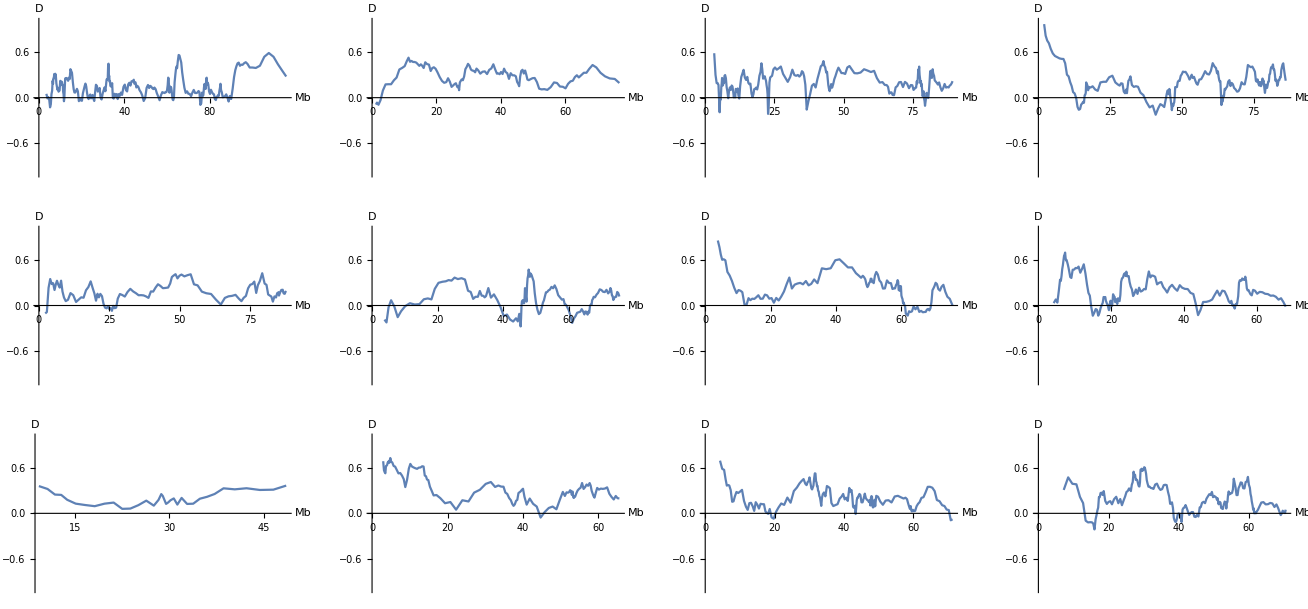

```mathematica
GraphicsGrid[Partition[Table[ListPlot[chromMed⟦i⟧,ImageSize->300, AxesLabel->{ "Mb","D"}, Joined->True, PlotRange->{-1,1}],{i,1,12}],4]]
```

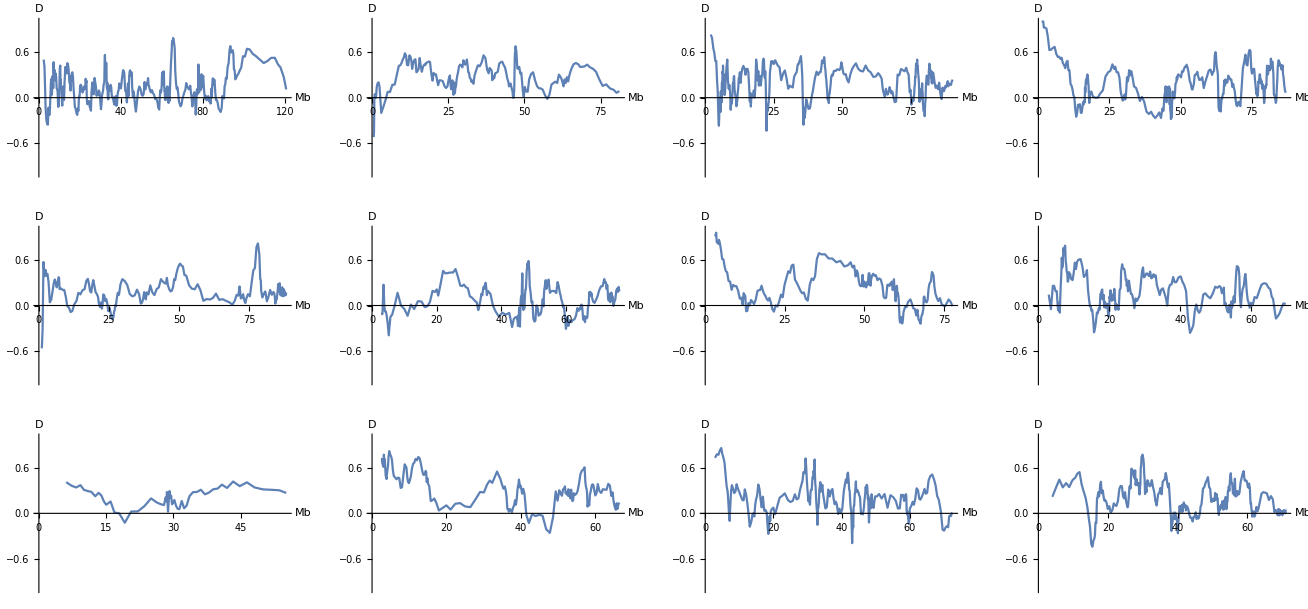

```mathematica
GraphicsGrid[Partition[Table[ListPlot[chromsh⟦i⟧,ImageSize->300, AxesLabel->{ "Mb","D"}, Joined->True, PlotRange->{-1,1}],{i,1,12}],4]]
```

### Pattern of divergence along the genome

##### Divergence Wolf - Red

```mathematica
div[l_]:=Total[Delete[l,{{3},{4}}]]
```

```mathematica
chromDivWR=Table[{#⟦1⟧/(10^6),div[#⟦2⟧]/(1000*300)}&/@chromTestMed⟦i⟧//N, {i,1,38}];
```

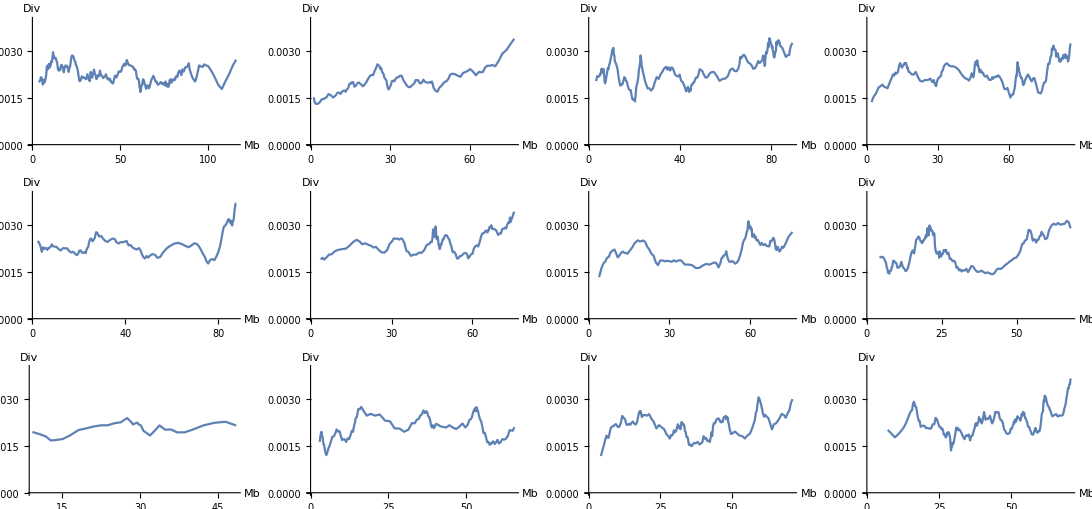

```mathematica
GraphicsGrid[Partition[Table[ListPlot[chromDivWR⟦i⟧, ImageSize->250,AxesLabel->{ "Mb","Div"}, Joined->True, PlotRange->{0,0.004}],{i,1,12}],4]]
```

Using a shorter size of the partially overlapping windows:

```mathematica
chromDivShortWR=Table[{#⟦1⟧/(10^6),div[#⟦2⟧]/(1000*160)}&/@chromTestShort⟦i⟧//N, {i,1,38}];
```

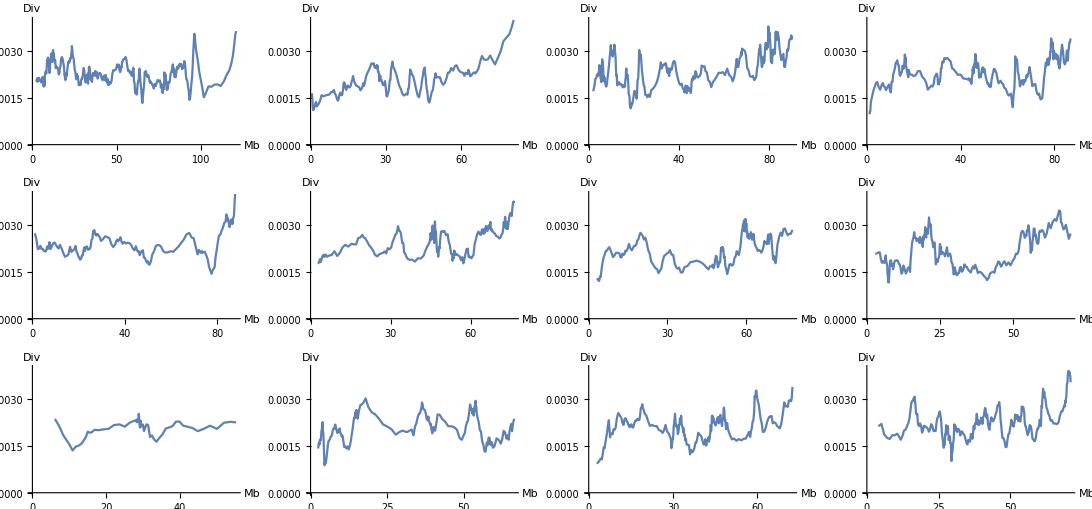

```mathematica
GraphicsGrid[Partition[Table[ListPlot[chromDivShortWR⟦i⟧, ImageSize->250,AxesLabel->{ "Mb","Div"}, Joined->True, PlotRange->{0,0.004}],{i,1,12}],4]]
```

##### Divergence Coyote - Red

```mathematica
div2[l_]:=Total[Delete[l,{{1},{6}}]]
```

```mathematica
chromDivCR=Table[{#⟦1⟧/(10^6),div2[#⟦2⟧]/(1000*300)}&/@chromTestMed⟦i⟧//N, {i,1,38}];
```

```mathematica
GraphicsGrid[Partition[Table[ListPlot[chromDivCR⟦i⟧, ImageSize->250,AxesLabel->{ "Mb","Div"}, Joined->True, PlotRange->{0,0.004}],{i,1,12}],4]];
```

Using a shorter size of the partially overlapping windows:

```mathematica
chromDivShortCR=Table[{#⟦1⟧/(10^6),div2[#⟦2⟧]/(1000*160)}&/@chromTestShort⟦i⟧//N, {i,1,38}];
```

```mathematica
GraphicsGrid[Partition[Table[ListPlot[chromDivShortCR⟦i⟧, ImageSize->250,AxesLabel->{ "Mb","Div"}, Joined->True, PlotRange->{0,0.004}],{i,1,12}],4]];
```

##### Divergence Coyote - Wolf

```mathematica
div3[l_]:=Total[Delete[l,{{2},{5}}]]
```

```mathematica
chromDivCW=Table[{#⟦1⟧/(10^6),div3[#⟦2⟧]/(1000*300)}&/@chromTestMed⟦i⟧//N, {i,1,38}];
```

```mathematica
GraphicsGrid[Partition[Table[ListPlot[chromDivCW⟦i⟧, ImageSize->250,AxesLabel->{ "Mb","Div"}, Joined->True, PlotRange->{0,0.004}],{i,1,12}],4]];
```

Using a shorter size of the partially overlapping windows:

```mathematica
chromDivShortCW=Table[{#⟦1⟧/(10^6),div3[#⟦2⟧]/(1000*160)}&/@chromTestShort⟦i⟧//N, {i,1,38}];
```

```mathematica
GraphicsGrid[Partition[Table[ListPlot[chromDivShortCW⟦i⟧, ImageSize->250,AxesLabel->{ "Mb","Div"}, Joined->True, PlotRange->{0,0.004}],{i,1,12}],4]];
```

##### Comparison

```mathematica
compareChromDiv={chromDivWR[[#]],chromDivCR[[#]],chromDivCW[[#]]}&/@Range[4];
```

```mathematica
GraphicsGrid[Partition[Table[ListPlot[compareChromDiv[[i]],ImageSize->500,PlotLegends->Placed[{"WR","CR","CW"},Below], AxesLabel->{ "Mb","Div"}, Joined->True,PlotRange->{0.0009,0.0040}],{i,1,4}],2]]
```

-Graphics-

```mathematica
compareChromDivShort={chromDivShortWR[[#]],chromDivShortCR[[#]],chromDivShortCW[[#]]}&/@Range[4];
```

```mathematica
GraphicsGrid[Partition[Table[ListPlot[compareChromDivShort[[i]],ImageSize->500,PlotLegends->Placed[{"WR","CR","CW"},Below], AxesLabel->{ "Mb","Div"}, Joined->True,PlotRange->{0.0001,0.0042}],{i,1,4}],2]]
```

-Graphics-

### Building the distribution of the relative divergence

```mathematica
Total[Length[chromTestMed[[#]]]&/@Range[38]]
```

5307

#### WR - CR

```mathematica
genomeRelDiv=Catenate[(div[#⟦2⟧]-div2[#⟦2⟧])&/@chromtest⟦#⟧&/@Range[38]];
```

```mathematica
genomeRelDiv//Mean // N
```

0.911075

```mathematica
WRvsCR=Histogram[genomeRelDiv,50,PlotRangePadding->{1000,10},ChartLabels->{Placed[{"WR - CR"},Above]}];
```

#### WC - WR

```mathematica
genomeRelDiv2=Catenate[(div3[#⟦2⟧]-div[#⟦2⟧])&/@chromtest⟦#⟧&/@Range[38]];
genomeRelDiv2//Mean // N
```

118.52

```mathematica
WCvsWR=Histogram[genomeRelDiv2,50,PlotRangePadding->{1000,10},ChartLabels->{Placed[{"WC - WR"},Above]}];
```

#### WC - CR

```mathematica
genomeRelDiv3=Catenate[(div3[#⟦2⟧]-div2[#⟦2⟧])&/@chromtest⟦#⟧&/@Range[38]];
```

```mathematica
genomeRelDiv3//Mean // N
```

271.625

```mathematica
WCvsCR=Histogram[genomeRelDiv3,50,PlotRangePadding->{1000,10},ChartLabels->{Placed[{"WC - CR"},Above]}];
```

#### Relative Divergence Plots

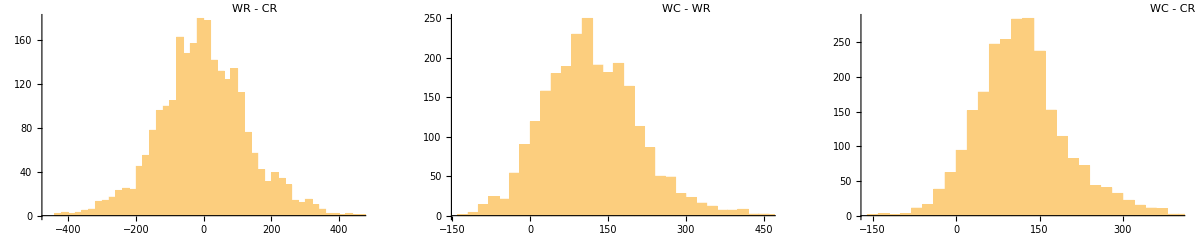

```mathematica
GraphicsGrid[{{WRvsCR,WCvsWR,WCvsCR}}]
```

### GlobalTajima’s D (to test deviations from Neutrality)

```mathematica
tajima=(Take[#,{6,12}]&/@data1);
```

```mathematica
countTajima=Total[tajima[[#]]&/@Range[Length[tajima]]];
```

```mathematica
tajimaK=(3(countTajima[[7]]+countTajima[[1]]+ countTajima[[2]]+ countTajima[[4]])+4(countTajima[[3]]+countTajima[[5]]+countTajima[[6]]))/6;
```

```mathematica
tajimaS=Total[countTajima]/HarmonicNumber[3];
```

```mathematica
e1=(5/9 -1/HarmonicNumber[3])/HarmonicNumber[3];
e2=(46/96 -6/(4 HarmonicNumber[3])+HarmonicNumber[3,2]/(HarmonicNumber[3]^2))/HarmonicNumber[3,2];
```

```mathematica
varTajima=(e1 Total[countTajima]+e2 Total[countTajima](Total[countTajima]-1));
```

```mathematica
tajimasD=(tajimaK-tajimaS)/varTajima^(1/2)//N
```

-0.125502

## Model Fitting assuming (W,(R,C))

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLE=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcounts],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->200]]
```

{1292.9,{-652792.,{t1→0.449325,t2→0.0853327,theta→1.42022}}}

Checking the direction of merging for the two divergence events

```mathematica
AbsoluteTiming[divMLE2=NMaximize[{totallnL[tripleGFVariantINVf0,ω,theta,{T->t1,T2->t2},3,testcounts],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->200]]
```

{676.452,{-652792.,{t1→0.449325,t2→0.0853327,theta→1.42022}}}

Same result, which is reassuring!

```mathematica
AbsoluteTiming[divMLE3=NMaximize[{totallnL[triGFinvf0,ω,theta,{T->t1,T2->t2},3,testcounts],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->200]]
```

{670.597,{-652792.,{t1→0.449325,t2→0.0853327,theta→1.42022}}}

Again we got the same results as expected. This is true for the following model as well.

```mathematica
AbsoluteTiming[divMLE4=NMaximize[{totallnL[triGFvariantINVf0,ω,theta,{T->t1,T2->t2},3,testcounts],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->200]]
```

{710.091,{-652792.,{t1→0.449325,t2→0.0853327,theta→1.42022}}}

Just a couple of extra sanity checks: testing a different method to maximize the likelihood....

```mathematica
AbsoluteTiming[FindMaximum[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcounts],2>t1>0 ,1>t2>0,2>theta>0.5},{t1,t2,theta}]]
```

{762.607,{-652792.,{t1→0.449323,t2→0.0853262,theta→1.42024}}}

Same result! Now let’s expand the region of the manifold in the parameter space where we look for the maximum

```mathematica
AbsoluteTiming[FindMaximum[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcounts],5>t1>0 ,5>t2>0,10>theta>1},{t1,t2,theta}]]
```

{728.859,{-652792.,{t1→0.449323,t2→0.0853262,theta→1.42024}}}

Same result again! The Gf machinery seems to be consistent.

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.42;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

88750.

```mathematica
divT=2 Ne 3 (0.449)
```

239092.

(R, C) divergence time = 240 ky BP

```mathematica
divT2=2 Ne 3 (0.449+0.085)
```

284355.

(W, C) divergence time = 285 ky BP

Let' s use a higher max in configcounts :

```mathematica
AbsoluteTiming[divMLEhm=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,largecounts],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->200]]
```

{358.312,{-613681.,{t1→0.534154,t2→0.0896204,theta→1.25665}}}

```mathematica
blocksize=1000;gen1=3;μ=0.4 10^-8; θ=1.257;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

78562.5

```mathematica
divT1=2 Ne 3 (0.534)
```

251714.

(R, C) divergence time = 250 ky BP

```mathematica
divT2=2 Ne 3 (0.534+0.0896)
```

293949.

(W, C) divergence time = 295 ky BP

### Fitting different IUA models

#### IUA (W → R)

```mathematica
AbsoluteTiming[iuaMLE=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcounts],9/10>tgf>1/10,1>t1>1/10 ,1>t2>1/10,18/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->250]]
```

{1233.42,{-650892.,{F→0.355982,tgf→0.223228,t1→0.201518,t2→0.292215,theta→1.33861}}}

```mathematica
AbsoluteTiming[iuaMLElarge=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,largecounts],0.5>tgf>0.1,0.5>t1>0.1 ,1>t2>0.1,1.5>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7,MaxIterations->350]]
```

{912.522,{-611682.,{F→0.317718,tgf→0.236598,t1→0.303779,t2→0.300799,theta→1.17118}}}

##### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.34;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

83750.

```mathematica
admT=2 Ne 3 (0.223)
```

112058.

Admixture time =  110 ky BP

```mathematica
divT=2 Ne 3 (0.2232+0.2015)
```

213412.

(R, C) divergence time = 210 ky BP

```mathematica
divT2=2 Ne 3 (0.2232+0.2015+0.2922)
```

360242.

(W, C) divergence time = 360 ky BP

Let' s use a higher max in configcounts :

```mathematica
blocksize=1000;gen1=3;μ=0.4 10^-8; θ=1.17;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

73125.

```mathematica
admT= 2Ne 3 0.2366
```

103808.

Admixture time =  100 ky BP

```mathematica
divT1=2 Ne 3 (0.2366+0.304)
```

237188.

(R, C) divergence time =  240 ky BP

```mathematica
divT2=2 Ne 3  (0.2366+0.304+0.301)
```

369252.

(W, C) divergence time = 370 ky BP

#### IUA (R → W)

```mathematica
AbsoluteTiming[OtherIUAMLE=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcounts],1>tgf>0,1>t1>0 ,1>t2>0,1.6>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{3961.42,{-650564.,{F→0.692843,tgf→0.320282,t1→0.226512,t2→0.696779,theta→1.30241}}}

```mathematica
AbsoluteTiming[OtherIUAMLEhm=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,largecounts],1>tgf>0,1>t1>0 ,2>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7,MaxIterations->350]]
```

{4897.56,{-611466.,{F→0.689432,tgf→0.398115,t1→0.247322,t2→0.73387,theta→1.14848}}}

##### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.30;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

81250.

```mathematica
admT=2 Ne 3 0.32
```

156000.

Admixture time = 155 ky BP

```mathematica
divT=2 Ne 3 (0.32+0.2265)
```

266419.

(R, C) divergence time = 265 ky BP

```mathematica
divT2=2 Ne 3 (0.32+0.2265+0.6969)
```

606157.

(W, C) divergence time = 600 ky BP

Let' s use a higher max in configcounts :

```mathematica
blocksize=1000;gen1=3;μ=0.4 10^-8; θ=1.148;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

71750.

```mathematica
divT1=2 Ne 3 (0.398+0.247)
```

277672.

(R, C) divergence time = 275 ky BP

```mathematica
divT2=2 Ne 3  (0.398+0.247+0.734)
```

593660.

(W, C) divergence time = 590 ky BP

#### IUA (W → C)

We do not expect wolf and coyote to be admixed, we use wolves as a proxy for recent admixture from dogs into coyote.
We found an almost null F and this model has the same likelihood that a pure divergence model which excludes any recent introgression into the Californian coyote lineage

```mathematica
AbsoluteTiming[RecentIUAMLE=NMaximize[{totallnL[triGFotherINV,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcounts],2>tgf>0,2>t1>0 ,2>t2>0,17/10>theta>1,0.5>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->400]]
```

{735.788,{-652792.,{F→8.82153×10^-8,tgf→0.244454,t1→0.205254,t2→0.084931,theta→1.41989}}}

#### IUA (C → W)

Again the admixture fraction is negligible also same likelihood that a pure divergence model which is reassuring

```mathematica
AbsoluteTiming[wrongIUAMLE=NMaximize[{totallnL[triGFotherVersoINV,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcounts],1>tgf>0,1>t1>0 ,1>t2>0,2>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->300]]
```

{1868.53,{-652792.,{F→1.31019×10^-6,tgf→0.183964,t1→0.265288,t2→0.085408,theta→1.42034}}}

#### Old Admixture W → (R,C)

```mathematica
AbsoluteTiming[oldIUAmle=NMaximize[{totallnL[oldGFinv,ω,theta,{A->tgf,T1->t1,T2->t2,f->F},3,testcounts],1>tgf>0,1>t1>0 ,2>t2>0,1.9>theta>0.9,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{6811.88,{-651245.,{F→0.518233,tgf→0.0790265,t1→0.456603,t2→1.09798,theta→1.0462}}}

#### Old Admixture (R,C) → W

This model collapsed : tgf = 0

```mathematica
AbsoluteTiming[oldotherIUAmle=NMaximize[{totallnL[oldGFversoINV,ω,theta,{A->tgf,T1->t1,T2->t2,f->F},3,testcounts],1>tgf>0,1>t1>0 ,1>t2>0,1.9>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->300]]
```

{1427.29,{-652186.,{F→0.84166,tgf→0.,t1→0.487542,t2→0.920353,theta→1.34744}}}

### Fitting a double admixture model

#### Model 1: (W→R) and (R→W)

```mathematica
AbsoluteTiming[dualMLE=NMaximize[{totallnL[dualGFinv,ω,theta,{A1->tgf1,A2->tgf2,T1->t1,T2->t2,f1->F1,f2->F2},3,testcounts],1>tgf1>0,1>tgf2>0,2>t1>0 ,2>t2>0,1.8>theta>0.8,1>F1>0,1>F2>0},{F1,F2,tgf1,tgf2,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->400]]
```

{11093.5,{-649997.,{F1→0.640188,F2→0.391953,tgf1→0.320315,tgf2→0.000102435,t1→0.193945,t2→0.964105,theta→1.07769}}}

#### Model 1 : (R → W) and (W → R)

```mathematica
AbsoluteTiming[dualMLEvariant=NMaximize[{totallnL[dualGFvariantINV,ω,theta,{A1->tgf1,A2->tgf2,T1->t1,T2->t2,f1->F1,f2->F2},3,testcounts],1>tgf1>0,1>tgf2>0,1>t1>0 ,2>t2>0,18/10>theta>9/10,1>F1>0,1>F2>0},{F1,F2,tgf1,tgf2,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7,MaxIterations->750]]
```

{10770.5,{-650106.,{F1→0.599065,F2→0.324574,tgf1→0.231733,tgf2→0.00147504,t1→0.299825,t2→0.823616,theta→1.12757}}}

#### Model 2 : (C → R) and (W → R)

```mathematica
AbsoluteTiming[dualMLECRWR=NMaximize[{totallnL[dualZYandXYinv,ω,theta,{A1->tgf1,A2->tgf2,T1->t1,T2->t2,f1->F1,f2->F2},3,testcounts],1>tgf1>0,1>tgf2>0,2>t1>0 ,2>t2>0,18/10>theta>1,1>F1>0,1>F2>0},{F1,F2,tgf1,tgf2,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->500]]
```

{3547.18,{-650765.,{F1→0.286753,F2→0.412066,tgf1→0.180115,tgf2→0.00127135,t1→0.540981,t2→0.0246672,theta→1.30809}}}

#### Model 2 : (C → R) and (R → W)

```mathematica
AbsoluteTiming[dualMLECRRW=NMaximize[{totallnL[dualZYandYXinv,ω,theta,{A1->tgf1,A2->tgf2,T1->t1,T2->t2,f1->F1,f2->F2},3,testcounts],1>tgf1>0,1>tgf2>0,2>t1>0 ,2>t2>0,18/10>theta>1,1>F1>0,1>F2>0},{F1,F2,tgf1,tgf2,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->600]]
```

#### Model 3 : (C → R) and (W→(R,C))

```mathematica
AbsoluteTiming[dualMLEold=NMaximize[{totallnL[dualGFoldINV,ω,theta,{AD1->tgf1,T1->t1,AD2->tgf2,T2->t2,f1->F1,f2->F2},3,testcounts],1>tgf1>0,1>tgf2>0,2>t1>0 ,2>t2>0,18/10>theta>1,1>F1>0,1>F2>0},{F1,F2,tgf1,t1,tgf2,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7,MaxIterations->750]]
```

## Loading and ordering the data assuming (C,(R,W))

```mathematica
test=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/ARC/autosomes_YRCJ_1000.csv","TSV"];
```

```mathematica
data1=Drop[test,1];
```

```mathematica
test[[1]]
```

{(ch,start,end),Multiple,(0, 0, 0),(0, 0, 1),(0, 1, 0),(0, 1, 1),(1, 0, 0),(1, 0, 1),(1, 1, 0),(1, 1, 1)}

```mathematica
testinGroupBis={#⟦1⟧,#⟦2⟧,#⟦4⟧,#⟦3⟧,#⟦5⟧,#⟦6⟧}&/@(Take[#,{6,12}]&/@data1);
```

```mathematica
testcountsBis=configCounts[testinGroupBis,3]
```

SparseArray[…]

## The D-statistic and Divergence

### Global D-stat

```mathematica
testmeanBis=testinGroupBis//Mean//N
```

{0.90822,0.788727,0.91016,0.404576,0.270811,0.391792}

```mathematica
dBis=(testmeanBis⟦4⟧-testmeanBis⟦5⟧)/(testmeanBis⟦4⟧+testmeanBis⟦5⟧)
```

0.198057

### The D-stat along the genome

```mathematica
windowmeansBIS[data_,len_,o_]:=Module[{partd=Partition[data,len,o]},Table[{Mean[((#⟦2⟧+#⟦3⟧)/2)&/@partd⟦i⟧],Total[{#⟦1⟧,#⟦2⟧,#⟦4⟧,#⟦3⟧,#⟦5⟧,#⟦6⟧}&/@(Take[#,{6,12}]&/@partd⟦i⟧)]},{i,1,Length[partd]}]]
```

#### Create a sliding window

```mathematica
chromtestBis=Table[windowmeansBIS[orgdata⟦i⟧,500,50],{i,1,38}];
```

```mathematica
chromDbis=Table[{#⟦1⟧/(10^6),dstat[#⟦2⟧]}&/@chromtestBis⟦i⟧//N,{i,1,38}];
```

#### Different window size (medium)

```mathematica
chromTestMedbis=Table[windowmeansBIS[orgdata⟦i⟧,300,30],{i,1,38}];
```

```mathematica
chromMedbis=Table[{#⟦1⟧/(10^6),dstat[#⟦2⟧]}&/@chromTestMedbis⟦i⟧//N,{i,1,38}];
```

#### Different window size (short)

```mathematica
chromTestShortBis=Table[windowmeansBIS[orgdata⟦i⟧,150,20],{i,1,38}];
```

```mathematica
chromshBis=Table[{#⟦1⟧/(10^6),dstat[#⟦2⟧]}&/@chromTestShortBis⟦i⟧//N,{i,1,38}];
```

#### Plot the results of the D-statistic

D varies between chromosomes:

```mathematica
Table[dstat[Total[{#⟦1⟧,#⟦2⟧,#⟦4⟧,#⟦3⟧,#⟦5⟧,#⟦6⟧}&/@(Take[#,{6,12}]&/@orgdata⟦i⟧)]]//N,{i,1,38}]
```

{0.223674,0.233589,0.28522,0.210353,0.259661,0.263034,0.262276,0.260529,0.182654,0.207707,0.147307,0.180928,0.121793,0.118411,0.137644,0.172514,0.214821,0.293239,0.15357,0.251748,0.10919,0.230902,0.120773,0.164095,0.209538,0.136621,0.13264,0.125442,0.122161,0.227656,0.115086,0.133005,0.253012,0.165204,0.184765,0.490576,0.216851,0.0466077}

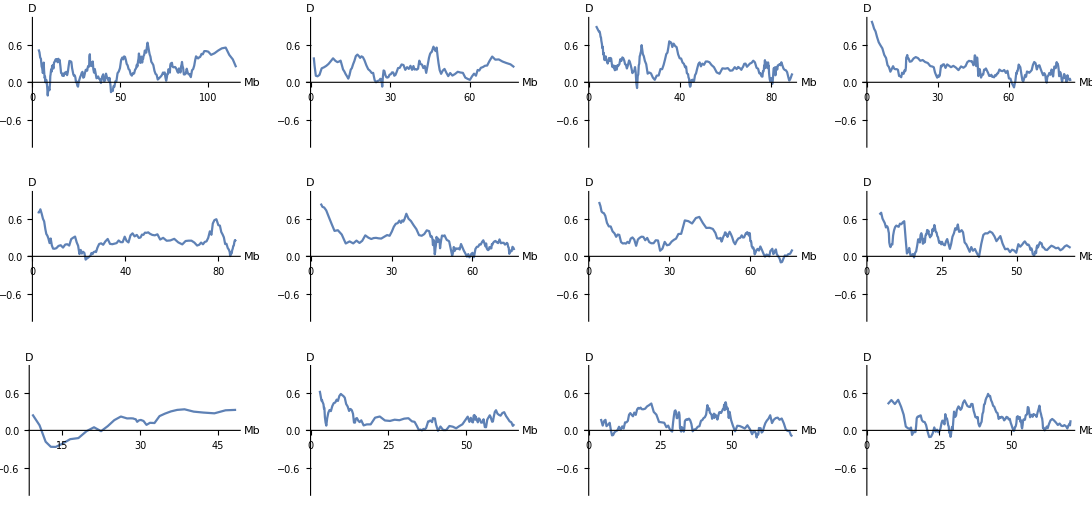

```mathematica
GraphicsGrid[Partition[Table[ListPlot[chromMedbis⟦i⟧,ImageSize->250, AxesLabel->{ "Mb","D"}, Joined->True, PlotRange->{-1,1}],{i,1,12}],4]]
```

Using a shorter size of the partially overlapping windows:

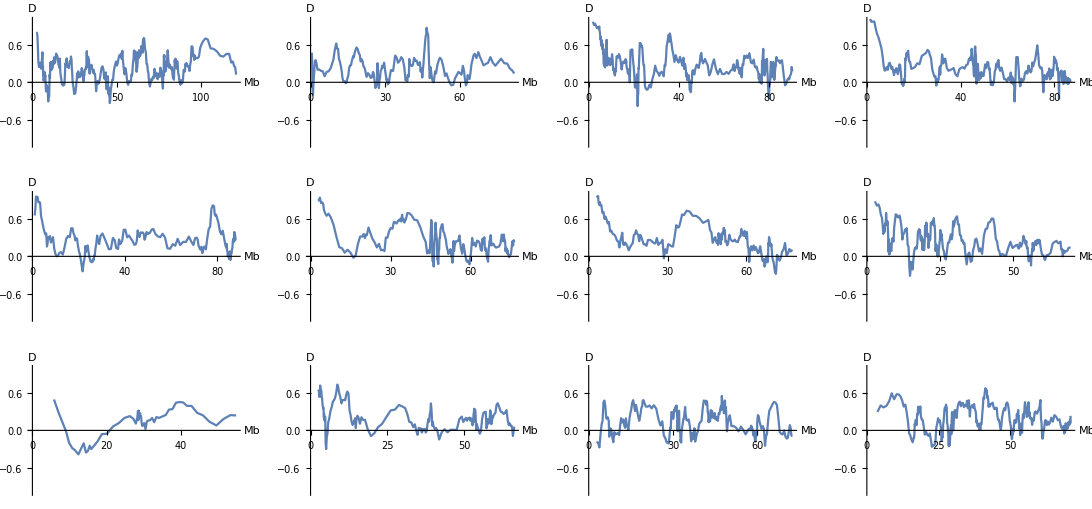

```mathematica
GraphicsGrid[Partition[Table[ListPlot[chromshBis⟦i⟧,ImageSize->250, AxesLabel->{ "Mb","D"}, Joined->True, PlotRange->{-1,1}],{i,1,12}],4]]
```

### Pattern of divergence along the genome

##### Divergence Wolf - Red

```mathematica
chromDivWRbis=Table[{#⟦1⟧/(10^6),div2[#⟦2⟧]/(1000*300)}&/@chromTestMedbis⟦i⟧//N, {i,1,38}];
```

```mathematica
GraphicsGrid[Partition[Table[ListPlot[chromDivWRbis⟦i⟧, ImageSize->250,AxesLabel->{ "Mb","Div"}, Joined->True, PlotRange->{0,0.005}],{i,1,12}],4]];
```

Using a shorter size of the partially overlapping windows:

```mathematica
chromDivShortWRbis=Table[{#⟦1⟧/(10^6),div2[#⟦2⟧]/(1000*150)}&/@chromTestShortBis⟦i⟧//N, {i,1,38}];
```

```mathematica
GraphicsGrid[Partition[Table[ListPlot[chromDivShortWRbis⟦i⟧, ImageSize->250,AxesLabel->{ "Mb","Div"}, Joined->True, PlotRange->{0,0.005}],{i,1,12}],4]];
```

##### Divergence Coyote - Red

```mathematica
chromDivCRbis=Table[{#⟦1⟧/(10^6),div[#⟦2⟧]/(1000*300)}&/@chromTestMedbis⟦i⟧//N, {i,1,38}];
```

```mathematica
GraphicsGrid[Partition[Table[ListPlot[chromDivCRbis⟦i⟧, ImageSize->250,AxesLabel->{ "Mb","Div"}, Joined->True, PlotRange->{0,0.005}],{i,1,12}],4]];
```

Using a shorter size of the partially overlapping windows:

```mathematica
chromDivShortCRbis=Table[{#⟦1⟧/(10^6),div2[#⟦2⟧]/(1000*150)}&/@chromTestShortBis⟦i⟧//N, {i,1,38}];
```

```mathematica
GraphicsGrid[Partition[Table[ListPlot[chromDivShortCR⟦i⟧, ImageSize->250,AxesLabel->{ "Mb","Div"}, Joined->True, PlotRange->{0,0.005}],{i,1,12}],4]];
```

##### Divergence Coyote - Wolf

```mathematica
chromDivCWbis=Table[{#⟦1⟧/(10^6),div3[#⟦2⟧]/(1000*300)}&/@chromTestMedbis⟦i⟧//N, {i,1,38}];
```

```mathematica
GraphicsGrid[Partition[Table[ListPlot[chromDivCWbis⟦i⟧, ImageSize->250,AxesLabel->{ "Mb","Div"}, Joined->True, PlotRange->{0,0.005}],{i,1,12}],4]];
```

Using a shorter size of the partially overlapping windows:

```mathematica
chromDivShortCWbis=Table[{#⟦1⟧/(10^6),div3[#⟦2⟧]/(1000*150)}&/@chromTestShortBis⟦i⟧//N, {i,1,38}];
```

```mathematica
GraphicsGrid[Partition[Table[ListPlot[chromDivShortCWbis⟦i⟧, ImageSize->250,AxesLabel->{ "Mb","Div"}, Joined->True, PlotRange->{0,0.005}],{i,1,12}],4]];
```

##### Comparison

```mathematica
compareChromDivBis={chromDivWRbis[[#]],chromDivCRbis[[#]],chromDivCWbis[[#]]}&/@Range[4];
```

```mathematica
GraphicsGrid[Partition[Table[ListPlot[compareChromDivBis[[i]],ImageSize->250,PlotLegends->Placed[{"WR","CR","CW"},Below], AxesLabel->{ "Mb","Div"}, Joined->True,PlotRange->{0.0009,0.0045}],{i,1,4}],4]]
```

-Graphics-

Sanity Check:

```mathematica
chromDivWRbis[[1]]==chromDivWR[[1]]
```

True

To change

## Model Fitting assuming (C,(R,W))

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLEbis=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsBis],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{290.763,{-3.66986×10^6,{t1→0.430279,t2→0.051491,theta→1.40808}}}

When f → 0  the following model should give the same results as the previous one and indeed it does!

```mathematica
AbsoluteTiming[divMLEbisVERSO=NMaximize[{totallnL[triGFinvf0,ω,theta,{T->t1,T2->t2},3,testcountsBis],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{301.483,{-3.66986×10^6,{t1→0.430279,t2→0.051491,theta→1.40808}}}

When f → 0  this model should give the same results as the first one and indeed it does!

```mathematica
AbsoluteTiming[divMLEbisVariant=NMaximize[{totallnL[tripleGFVariantINVf0,ω,theta,{T->t1,T2->t2},3,testcountsBis],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{308.862,{-3.66986×10^6,{t1→0.430279,t2→0.051491,theta→1.40808}}}

When f → 0  this model should also give the same results as the first one and indeed it does!

```mathematica
AbsoluteTiming[divMLEbisVariant2=NMaximize[{totallnL[triGFvariantINVf0,ω,theta,{T->t1,T2->t2},3,testcountsBis],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{326.391,{-3.66986×10^6,{t1→0.430279,t2→0.051491,theta→1.40808}}}

### Fitting different IUA models

#### IUA (C → R)

```mathematica
AbsoluteTiming[iuaMLEBis=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsBis],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{1383.21,{-3.65321×10^6,{F→0.566463,tgf→0.298587,t1→0.000262168,t2→0.411531,theta→1.30876}}}

This model should give the same results as the previous one, given that the only difference is the direction of the second and the third mergers. Indeed it does, which is reassuring.

```mathematica
AbsoluteTiming[iuaMLEBisVariant=NMaximize[{totallnL[tripleGFVariantINV,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsBis],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{1400.11,{-3.65321×10^6,{F→0.566463,tgf→0.298587,t1→0.000262168,t2→0.411531,theta→1.30876}}}

#### IUA (R → C)

```mathematica
AbsoluteTiming[OtherIUAMLEBis=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsBis],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{1851.15,{-3.65286×10^6,{F→0.700191,tgf→0.258419,t1→0.282993,t2→0.623824,theta→1.2839}}}

This should give the same results and again it’s consistent.

```mathematica
AbsoluteTiming[OtherIUAMLEvariantBis=NMaximize[{totallnL[triGFvariantINV,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsBis],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{2362.22,{-3.65286×10^6,{F→0.700191,tgf→0.258419,t1→0.282993,t2→0.623824,theta→1.2839}}}

#### IUA (W → C)

Attempting to control for recent admixture from dogs into the coyote lineage using grey wolf as a proxy

```mathematica
AbsoluteTiming[recentIUAMLEBis=NMaximize[{totallnL[triGFotherVersoINV,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsBis],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{1620.43,{-3.66765×10^6,{F→0.883081,tgf→0.451021,t1→0.0000116,t2→0.878755,theta→1.35517}}}

#### IUA (C → W)

Another attempt to control for recent admixture from dogs into the coyote lineage using grey wolf as a proxy

```mathematica
AbsoluteTiming[wrongIUAMLEbis=NMaximize[{totallnL[triGFotherINV,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsBis],2>tgf>0,2>t1>0 ,2>t2>0,17/10>theta>1,0.5>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->400]]
```

{716.7,{-3.66986×10^6,{F→0.000209764,tgf→0.326366,t1→0.103857,t2→0.0515778,theta→1.40813}}}

#### Old Admixture C → (R,W)

```mathematica
AbsoluteTiming[oldIUAmleBis=NMaximize[{totallnL[oldGFinv,ω,theta,{A->tgf,T1->t1,T2->t2,f->F},3,testcountsBis],1>tgf>0,1>t1>0 ,2>t2>0,1.9>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->300]]
```

{4304.6,{-3.66109×10^6,{F→0.57325,tgf→0.0784737,t1→0.407554,t2→1.09251,theta→1.05854}}}

#### Old Admixture (R,W) → C

```mathematica
AbsoluteTiming[oldOtherIUAmleBis=NMaximize[{totallnL[oldGFversoINV,ω,theta,{A->tgf,T1->t1,T2->t2,f->F},3,testcountsBis],1>tgf>0,1>t1>0 ,1>t2>0,1.9>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->300]]
```

{1351.3,{-3.66764×10^6,{F→0.882921,tgf→0.,t1→0.450853,t2→0.878846,theta→1.35539}}}

## Checking the effect of block length

### 500 base-pairs

#### Model Fitting (W, (R, C))

##### Loading and ordering the data assuming (W, (R, C))

```mathematica
test500=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/ARC/autosomes_YRCJ_500.csv","TSV"];
```

Check the number of blocks

```mathematica
data500=Drop[test500,1];
```

```mathematica
Length[data500]
```

419200

```mathematica
testinGroup500={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{6,12}]&/@data500);
```

```mathematica
testcounts500=configCounts[testinGroup500,3]
```

SparseArray[…]

##### SD (W, (R, C))

```mathematica
AbsoluteTiming[divMLE500=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcounts500],1>t1>0 ,1>t2>0,1>theta>0 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{653.172,{-1.52266×10^6,{t1→0.375495,t2→0.0772719,theta→0.802155}}}

##### IUA (W → R)

```mathematica
AbsoluteTiming[iuaMLE500=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcounts500],1>tgf>0,1>t1>0 ,1>t2>0,1>theta>0.1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->250]]
```

{1482.3,{-1.5199×10^6,{F→0.344228,tgf→0.161926,t1→0.184845,t2→0.241175,theta→0.769707}}}

##### IUA (R → W)

```mathematica
AbsoluteTiming[OtherIUAMLE500=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcounts500],1>tgf>0,1>t1>0 ,1>t2>0,1>theta>0,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 350 iterations.

{5695.11,{-1.51919×10^6,{F→0.778787,tgf→0.274015,t1→0.182289,t2→0.833715,theta→0.746407}}}

#### Model Fitting ((W, R), C)

##### Loading and ordering the data assuming ((W, R), C)

```mathematica
test500=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/ARC/autosomes_YRCJ_500.csv","TSV"];
```

```mathematica
data500=Drop[test500,1];
```

```mathematica
testinGroup500bis={#⟦1⟧,#⟦2⟧,#⟦4⟧,#⟦3⟧,#⟦5⟧,#⟦6⟧}&/@(Take[#,{6,12}]&/@data500);
```

```mathematica
testcounts500bis=configCounts[testinGroup500bis,3]
```

SparseArray[…]

##### SD ((W, R), C)

```mathematica
AbsoluteTiming[divMLE500bis=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcounts500bis],1>t1>0 ,1>t2>0,1>theta>0 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{354.847,{-1.52293×10^6,{t1→0.380778,t2→0.0645885,theta→0.803999}}}

##### IUA (C → R)

```mathematica
AbsoluteTiming[iuaMLE500Bis=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcounts500bis],1>tgf>0,1>t1>0 ,1>t2>0,0.9>theta>0.1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->250]]
```

##### IUA (R → C)

```mathematica
AbsoluteTiming[OtherIUAMLE500Bis=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcounts500bis],1>tgf>0,1>t1>0 ,1>t2>0,0.9>theta>0.1,0.9>F>0.1},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->250]]
```

### 2 Kb

#### Model Fitting (W, (R, C))

##### Loading and ordering the data assuming (W, (R, C))

```mathematica
test2kb=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/ARC/autosomes_YRCJ_2000.csv","TSV"];
```

```mathematica
data2kb=Drop[test2kb,1];
```

```mathematica
testinGroup2kbVERSO={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{6,12}]&/@data2kb);
```

```mathematica
testcounts2kbVERSO=configCounts[testinGroup2kbVERSO,3]
```

SparseArray[…]

##### SD (W, (R, C))

```mathematica
AbsoluteTiming[divMLE2kb=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcounts2kbVERSO],2>t1>0 ,2>t2>0,5>theta>2.1 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{274.144,{-153909.,{t1→0.483933,t2→0.0849843,theta→2.56418}}}

##### IUA (W → R)

```mathematica
AbsoluteTiming[iuaMLE2kb=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcounts2kbVERSO],1>tgf>0,1>t1>0 ,1>t2>0,2.7>theta>2.1,1>F>0.1},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->250]]
```

##### IUA (R → W)

```mathematica
AbsoluteTiming[OtherIUAMLE2kb=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcounts2kbVERSO],1>tgf>0,1>t1>0 ,1>t2>0,2.7>theta>2.1,1>F>0.1},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->300]]
```

#### Model Fitting ((W, R), C)

##### Loading and ordering the data assuming ((W, R), C)

```mathematica
test2kb=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/ARC/autosomes_YRCJ_2000.csv","TSV"];
```

```mathematica
data2kb=Drop[test2kb,1];
```

```mathematica
Length[data2kb]
```

389332

```mathematica
testinGroup2kb={#⟦1⟧,#⟦2⟧,#⟦4⟧,#⟦3⟧,#⟦5⟧,#⟦6⟧}&/@(Take[#,{6,12}]&/@data2kb);
```

```mathematica
testcounts2kb=configCounts[testinGroup2kb,3]
```

SparseArray[…]

##### SD ((W, R), C)

```mathematica
AbsoluteTiming[divMLEbis2kb=NMaximize[{totallnL[triGFinvf0,ω,theta,{T->t1,T2->t2},3,testcounts2kb],2>t1>0 ,1>t2>0,3>theta>2},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->200]]
```

##### IUA (C → R)

```mathematica
AbsoluteTiming[iuaMLEbis2kb=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcounts2kb],1>tgf>0,1>t1>0 ,1>t2>0,2.7>theta>2.1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->300]]
```

##### IUA (R → C)

```mathematica
AbsoluteTiming[OtherIUAMLEbis2kb=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcounts2kb],1>tgf>0,1>t1>0 ,1>t2>0,2.7>theta>2.1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->300]]
```

Banks Island

## Loading and ordering the data assuming (W, (R, C))

```mathematica
testBI=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/ARC/autosomes_BRCJ_1000.csv","TSV"];
```

Check the number of blocks

```mathematica
dataBI=Drop[testBI,1];
```

```mathematica
Length[dataBI]
```

129050

```mathematica
testinGroupBI={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{6,12}]&/@dataBI);
```

```mathematica
testcountsBI=configCounts[testinGroupBI,3]
```

SparseArray[…]

## The D-statistic and Relative Divergence

### Global D-stat

```mathematica
testmeanBI=testinGroupBI//Mean//N
```

{0.987269,0.778931,0.891895,0.379279,0.267609,0.403425}

```mathematica
dtestBI=(testmeanBI⟦4⟧-testmeanBI⟦5⟧)/(testmeanBI⟦4⟧+testmeanBI⟦5⟧)
```

0.172626

## Model Fitting assuming (W, (R, C))

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLEbi=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsBI],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{271.044,{-600163.,{t1→0.463954,t2→0.108628,theta→1.41597}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 gen1; θ = 1.416;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

29500.

```mathematica
divT=2 Ne 3 (0.464)
```

82128.

(R, C) divergence time =  82 ky BP

```mathematica
divT2=2 Ne 3 (0.464+0.109)
```

101421.

(W, C) divergence time =  101 ky BP

### Fitting different IUA models

#### IUA (W → R)

```mathematica
AbsoluteTiming[iuaMLEbi=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsBI],9/10>tgf>1/10,1>t1>1/10 ,1>t2>1/10,18/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->200]]
```

{857.414,{-598555.,{F→0.243189,tgf→0.104504,t1→0.373744,t2→0.272265,theta→1.33331}}}

#### IUA (R → W)

```mathematica
AbsoluteTiming[OtherIUAMLEbi=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsBI],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->300]]
```

{2932.49,{-598213.,{F→0.666004,tgf→0.345203,t1→0.220823,t2→0.700113,theta→1.29638}}}

#### IUA (W → C)

We do not expect wolf and coyote to be admixed, we use wolves as a proxy for recent admixture from dogs into coyote.
We found a null F and this model has the same likelihood that a pure divergence model which excludes any recent introgression into the Californian coyote lineage

```mathematica
AbsoluteTiming[RecentIUAMLEbi=NMaximize[{totallnL[triGFotherINV,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsBI],2>tgf>0,2>t1>0 ,2>t2>0,17/10>theta>1,0.5>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->400]]
```

{1237.91,{-600163.,{F→0.,tgf→0.463044,t1→0.00118728,t2→0.108787,theta→1.41547}}}

#### IUA (C → W)

Again the admixture fraction is negligible also same likelihood that a pure divergence model which is reassuring

```mathematica
AbsoluteTiming[wrongIUAMLEbi=NMaximize[{totallnL[triGFotherVersoINV,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsBI],1>tgf>0,2>t1>0 ,2>t2>0,1.9>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7,MaxIterations->400]]
```

{2314.2,{-600084.,{F→0.92052,tgf→0.583957,t1→6.34003×10^-6,t2→1.99932,theta→1.28073}}}

{105.881,{-641877.,{F→0.448125,t1→0.79332,t2→0.833628,tgf→0.395171,theta→1.32223}}}

```mathematica
AbsoluteTiming[FindMaximum[{totallnL[triGFotherVersoINV,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsBI],1>tgf>0,2>t1>0 ,2>t2>0,2>theta>1,1>F>0},{F,tgf,t1,t2,theta}]]
```

$Aborted

#### Old Admixture W → (R,C)

```mathematica
AbsoluteTiming[oldIUAmleBI=NMaximize[{totallnL[oldGFinv,ω,theta,{A->tgf,T1->t1,T2->t2,f->F},3,testcountsBI],1>tgf>0,1>t1>0 ,2>t2>0,1.9>theta>0.9,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{5970.27,{-598672.,{F→0.51228,tgf→0.0984603,t1→0.506501,t2→1.15288,theta→1.01868}}}

#### Old Admixture (R,C) → W

```mathematica
AbsoluteTiming[oldotherIUAmleBI=NMaximize[{totallnL[oldGFversoINV,ω,theta,{A->tgf,T1->t1,T2->t2,f->F},3,testcountsBI],1>tgf>0,1>t1>0 ,1>t2>0,1.9>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->400]]
```

{1252.81,{-599556.,{F→0.810957,tgf→0.,t1→0.510634,t2→0.894831,theta→1.33765}}}

## TODO : ALL THE REST

Great Plain wolf (Historical Sample)

## Loading and ordering the data assuming (W, (R, C))

```mathematica
testGP=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/HIST/autosomes_GRCJ_1000.csv","TSV"];
```

Check the number of blocks

```mathematica
dataGP=Drop[testGP,1];
```

```mathematica
Length[dataGP]
```

21793

```mathematica
testinGroupGP={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{6,12}]&/@dataGP);
```

```mathematica
testcountsGP=configCounts[testinGroupGP,3]
```

SparseArray[…]

## The D-statistic and Relative Divergence

### Global D-stat

```mathematica
testmeanGP=testinGroupGP//Mean//N
```

{7.35975,0.820263,0.930345,0.426926,0.292938,0.523517}

```mathematica
dtestGP=(testmeanGP⟦4⟧-testmeanGP⟦5⟧)/(testmeanGP⟦4⟧+testmeanGP⟦5⟧)
```

0.18613

## Model Fitting assuming (W, (R, C))

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLEGP=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsGP],2>t1>0 ,1>t2>0,3>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{240.539,{-118011.,{t1→0.649107,t2→0.859055,theta→2.0111}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 2.01;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

125625.

```mathematica
divT=2 Ne 3 (0.649)
```

489184.

(R, C) divergence time =  490 ky BP

```mathematica
divT2=2 Ne 3 (0.649+0.859)
```

1.13665×10^6

(W, C) divergence time =  1 My BP

### Fitting different IUA models

#### IUA (W → R)

```mathematica
AbsoluteTiming[iuaMLEgp=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsGP],9/10>tgf>1/10,1>t1>0.01 ,2>t2>1/10,18/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->200]]
```

#### IUA (R → W)

```mathematica
AbsoluteTiming[OtherIUAMLEbi=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsBI],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->300]]
```

#### IUA (W → C)

We do not expect wolf and coyote to be admixed, we use wolves as a proxy for recent admixture from dogs into coyote.
We found a null F and this model has the same likelihood that a pure divergence model which excludes any recent introgression into the Californian coyote lineage

```mathematica
AbsoluteTiming[RecentIUAMLEbi=NMaximize[{totallnL[triGFotherINV,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsBI],2>tgf>0,2>t1>0 ,2>t2>0,17/10>theta>1,0.5>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->400]]
```

#### IUA (C → W)

Again the admixture fraction is negligible also same likelihood that a pure divergence model which is reassuring

```mathematica
AbsoluteTiming[wrongIUAMLEbi=NMaximize[{totallnL[triGFotherVersoINV,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsBI],1>tgf>0,2>t1>0 ,2>t2>0,1.9>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7,MaxIterations->400]]
```

#### Old Admixture W → (R,C)

```mathematica
AbsoluteTiming[oldIUAmleBI=NMaximize[{totallnL[oldGFinv,ω,theta,{A->tgf,T1->t1,T2->t2,f->F},3,testcountsBI],1>tgf>0,1>t1>0 ,2>t2>0,1.9>theta>0.9,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

#### Old Admixture (R,C) → W

```mathematica
AbsoluteTiming[oldotherIUAmleBI=NMaximize[{totallnL[oldGFversoINV,ω,theta,{A->tgf,T1->t1,T2->t2,f->F},3,testcountsBI],1>tgf>0,1>t1>0 ,1>t2>0,1.9>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->400]]
```

## TODO : ALL THE REST

## Eurasian Grey wolf, Red wolf, Coyote

Portugal Grey Wolf

## Loading and ordering the data assuming (W,(R, C))

```mathematica
testEW1=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/ERC/autosomes_PRCJ_1000.csv","TSV"];
```

Check the number of blocks

```mathematica
dataEW1=Drop[testEW1,1];
```

```mathematica
Length[dataEW1]
```

94131

```mathematica
testinGroupEW1={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{6,12}]&/@dataEW1);
```

```mathematica
testcountsEW1=configCounts[testinGroupEW1,3]
```

SparseArray[…]

```mathematica
largecountsEW1=configCounts[testinGroupEW1,5]
```

SparseArray[…]

## The D-statistic and Divergence

### Global D-stat

```mathematica
testmeanEW1=testinGroupEW1//Mean//N
```

{0.980538,0.835304,0.939892,0.381564,0.275658,0.436966}

```mathematica
dEW1=(testmeanEW1⟦4⟧-testmeanEW1⟦5⟧)/(testmeanEW1⟦4⟧+testmeanEW1⟦5⟧)
```

0.161141

## Model Fitting assuming (W,(R, C))

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLEew1=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsEW1],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{206.699,{-439828.,{t1→0.458889,t2→0.116377,theta→1.45778}}}

```mathematica
AbsoluteTiming[divMLEew1Variant=NMaximize[{totallnL[triGFinvf0,ω,theta,{T->t1,T2->t2},3,testcountsEW1],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{204.85,{-439828.,{t1→0.458889,t2→0.116377,theta→1.45778}}}

#### Rescaling Time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.458;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

91125.

```mathematica
divT=2 Ne 3 (0.459)
```

250958.

(R, C) divergence time = 250 ky BP

```mathematica
divT2=2 Ne 3 (0.4589+0.1164)
```

314545.

(W, C) divergence time =  315 ky BP

### Fitting different IUA models

#### IUA (W → R)

```mathematica
AbsoluteTiming[iuaMLEew1=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsEW1],9/10>tgf>1/10,1.5>t1>1/100 ,1.5>t2>1/100,18/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->250]]
```

{1211.32,{-438799.,{F→0.307425,tgf→0.243106,t1→0.19872,t2→0.299425,theta→1.37955}}}

```mathematica
AbsoluteTiming[iuaMLEew1Large=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,largecountsEW1],9/10>tgf>1/10,1.5>t1>1/100 ,1.5>t2>1/100,18/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->250]]
```

{1890.31,{-409279.,{F→0.304816,tgf→0.310083,t1→0.237945,t2→0.328137,theta→1.1956}}}

##### Rescaling Time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.379;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

86187.5

```mathematica
admT= 2Ne 3 0.243
```

125661.

Admixture time = 125 ky BP

```mathematica
divT=2 Ne 3 (0.243+0.199)
```

228569.

(R, C) divergence time = 230 ky BP

```mathematica
divT2=2 Ne 3 (0.243+0.199+0.299)
```

383190.

(W, C) divergence time = 380 ky BP

Using large counts:

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.196;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

74750.

```mathematica
admT= 2Ne 3 0.31
```

139035.

Admixture time = 140 ky BP

```mathematica
divT=2 Ne 3 (0.31+0.238)
```

245778.

(R, C) divergence time = 245 ky BP

```mathematica
divT2=2 Ne 3 (0.31+0.238+0.328)
```

392886.

(W, C) divergence time = 390 ky BP

#### IUA (R → W)

```mathematica
AbsoluteTiming[OtherIUAMLEew1=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsEW1],1>tgf>0,1.5>t1>0 ,1.5>t2>0,1.8>theta>0.8,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{1738.03,{-438515.,{F→0.67066,tgf→0.356214,t1→0.201743,t2→0.727057,theta→1.33498}}}

##### Rescaling Time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.335;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

83437.5

```mathematica
admT= 2Ne 3 0.356
```

178222.

Admixture time = 180 ky BP

```mathematica
divT=2 Ne 3 (0.356+0.202)
```

279349.

(R, C) divergence time = 280 ky BP

```mathematica
divT2=2 Ne 3 (0.356+0.202+0.727)
```

643303.

(W, C) divergence time = 640 ky BP

#### IUA (W → C)

We do not expect an European wolf to be admixed with a Californian coyote,  it’s just a different proxy for dog admixture. The admixture fraction is 10^-5 which is reassuring.

```mathematica
AbsoluteTiming[RecentIUAMLEew1=NMaximize[{totallnL[triGFotherINV,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsEW1],2>tgf>0,2>t1>0 ,2>t2>0,17/10>theta>1,0.5>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->400]]
```

{981.279,{-439828.,{F→0.0000157317,tgf→0.437491,t1→0.0211154,t2→0.116447,theta→1.45789}}}

#### IUA (C → W)

This should have a poor fit as well but such an high admixture fraction is hard to interpret. It is worth noticing though that the admixture time seems to coincide with the split time suggesting that the model collapsed.

```mathematica
AbsoluteTiming[wrongIUAMLEew1=NMaximize[{totallnL[triGFotherVersoINV,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsEW1],1>tgf>0,1>t1>0 ,2>t2>0,2>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->6,PrecisionGoal->6,MaxIterations->300]]
```

{4052.81,{-439342.,{F→0.804941,tgf→0.511476,t1→0.0000853095,t2→0.926385,theta→1.37087}}}

#### Old Admixture W → (R,C)

```mathematica
AbsoluteTiming[oldIUAmleEW1=NMaximize[{totallnL[oldGFinv,ω,theta,{A->tgf,T1->t1,T2->t2,f->F},3,testcountsEW1],1>tgf>0,1>t1>0 ,2>t2>0,1.9>theta>0.9,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->300]]
```

{4169.99,{-438880.,{F→0.496486,tgf→0.0920226,t1→0.470618,t2→1.02966,theta→1.09389}}}

##### Rescaling Time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.09;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

68125.

```mathematica
divT1= 2Ne 3 0.471
```

192521.

(R, C) divergence time = 190 ky BP

```mathematica
admT=2 Ne 3 (0.471+0.092)
```

230126.

Admixture time = 230 ky BP

```mathematica
divT2=2 Ne 3 (0.471+0.092+1.03)
```

651139.

(W, C) divergence time = 650 ky BP

#### Old Admixture (R,C) → W

```mathematica
AbsoluteTiming[oldotherIUAmleEW1=NMaximize[{totallnL[oldGFversoINV,ω,theta,{A->tgf,T1->t1,T2->t2,f->F},3,testcountsEW1],2>tgf>0,2>t1>0 ,2>t2>0,1.9>theta>0.9,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{1177.6,{-439341.,{F→0.803394,tgf→0.,t1→0.510018,t2→0.915881,theta→1.37131}}}

The model collapsed, let' s try with large counts:

```mathematica
AbsoluteTiming[oldotherIUAmleEW1=NMaximize[{totallnL[oldGFversoINV,ω,theta,{A->tgf,T1->t1,T2->t2,f->F},3,largecountsEW1],2>tgf>0,2>t1>0 ,2>t2>0,1.8>theta>0.8,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7,MaxIterations->400]]
```

{1491.27,{-409925.,{F→0.793846,tgf→0.000806599,t1→0.610388,t2→0.953657,theta→1.19227}}}

Again almost  a collapsed model (tgf is approximately zero)

##### Rescaling Time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.19 ;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

74375.

```mathematica
divT1= 2Ne 3 0.61
```

272212.

(R, C) divergence time = 270 ky BP

```mathematica
admT=2 Ne 3 (0.61+0.001)
```

272659.

Admixture time = 270 ky BP

```mathematica
divT2=2 Ne 3 (0.61+0.001+0.954)
```

698381.

(W, C) divergence time = 700 ky BP

### Fitting a double admixture model

```mathematica
AbsoluteTiming[dualMLEew1=NMaximize[{totallnL[dualGFinv,ω,theta,{A1->tgf1,A2->tgf2,T1->t1,T2->t2,f1->F1,f2->F2},3,testcountsEW1],1>tgf1>0,1>tgf2>0,2>t1>0 ,2>t2>0,1.8>theta>0.8,1>F1>0,1>F2>0},{F1,F2,tgf1,tgf2,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7,MaxIterations->500]]
```

{8592.58,{-438183.,{F1→0.585359,F2→0.421165,tgf1→0.370719,tgf2→0.014779,t1→0.164918,t2→0.995933,theta→1.11353}}}

Rescaling Time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.11 ;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

69375.

```mathematica
admT1= 2Ne 3 0.37
```

154012.

Admixture time 1 = 150 ky BP

```mathematica
admT2=2 Ne 3 (0.371+0.015)
```

160673.

Admixture time 2 = 160 ky BP

```mathematica
divT1=2 Ne 3 (0.371+0.015+0.165)
```

229354.

(R, C) divergence time = 230 ky BP

```mathematica
divT2=2 Ne 3 (0.371+0.015+0.996)
```

575258.

(W, C) divergence time = 575 ky BP

```mathematica
AbsoluteTiming[dualMLEvariantEW1=NMaximize[{totallnL[dualGFvariantINV,ω,theta,{A1->tgf1,A2->tgf2,T1->t1,T2->t2,f1->F1,f2->F2},3,testcountsEW1],1>tgf1>0,1>tgf2>0,1>t1>0 ,1>t2>0,1.5>theta>0.8,1>F1>0,1>F2>0},{F1,F2,tgf1,tgf2,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7,MaxIterations->800]]
```

## TOCHECK/RE-RUN: Sampling blocks (W,(R,C))

### Distance > 100 kb

#### Loading

```mathematica
testW2=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/math_ERC_1kb.csv","TSV"];
```

```mathematica
orgdataW2=datatrans[testW2];
```

```mathematica
chromtest100kb=Table[windowmeans[orgdataW2⟦i⟧,1,100],{i,1,38}];
```

```mathematica
sampled100kb=Flatten[chromtest100kb[[All,All,2]],1];
```

```mathematica
sampledCounts100kb=configCounts[sampled100kb,3]
```

SparseArray[…]

#### Divergence

```mathematica
AbsoluteTiming[divMLEw2Samp100kb=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,sampledCounts100kb],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{366.811,{-35543.3,{t1→0.471544,t2→0.176718,theta→1.36093}}}

#### IUA (W → R)

```mathematica
AbsoluteTiming[iuaMLEw2Samp100kb=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,sampledCounts100kb],9/10>tgf>1/10,1>t1>1/100 ,1>t2>1/10,18/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->250]]
```

{786.19,{-35468.1,{F→0.254684,tgf→0.263219,t1→0.201445,t2→0.352838,theta→1.28359}}}

#### IUA (R → W)

```mathematica
AbsoluteTiming[OtherIUAMLEw2Samp100kb=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,sampledCounts100kb],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{2646.56,{-35437.,{F→0.607456,tgf→0.37964,t1→0.199925,t2→0.768137,theta→1.24007}}}

#### Double Admixture

```mathematica
AbsoluteTiming[dualMLEw2samp100kb=NMaximize[{totallnL[dualGFinv,ω,theta,{A1->tgf1,A2->tgf2,T1->t1,T2->t2,f1->F1,f2->F2},3,sampledCounts100kb],1>tgf1>0,1>tgf2>0,1>t1>0 ,1>t2>0,1.5>theta>1,1>F1>0,1>F2>0},{F1,F2,tgf1,tgf2,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->500]]
```

{8970.29,{-35437.,{F1→0.0000215446,F2→0.607923,tgf1→0.00584236,tgf2→0.374079,t1→0.199802,t2→0.768937,theta→1.24013}}}

```mathematica
AbsoluteTiming[dualMLEvariantW2samp100kb=NMaximize[{totallnL[dualGFvariantINV,ω,theta,{A1->tgf1,A2->tgf2,T1->t1,T2->t2,f1->F1,f2->F2},3,sampledCounts100kb],1>tgf1>0,1>tgf2>0,1>t1>0 ,2>t2>0,1.5>theta>1,1>F1>0,1>F2>0},{F1,F2,tgf1,tgf2,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7,MaxIterations->650]]
```

{19397.9,{-35418.8,{F1→0.590058,F2→0.240374,tgf1→0.377354,tgf2→0.0168357,t1→0.205805,t2→1.,theta→1.07394}}}

### Replicate 0 (distance > 1 Mb)

#### Loading

```mathematica
testW2=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/math_ERC_1kb.csv","TSV"];
```

```mathematica
orgdataW2=datatrans[testW2];
```

```mathematica
chromtestW2=Table[windowmeans[orgdataW2⟦i⟧,1,1000],{i,1,38}];
```

```mathematica
sampledW2=Flatten[chromtestW2[[All,All,2]],1];
```

```mathematica
sampledCounts=configCounts[sampledW2,3]
```

SparseArray[…]

#### Divergence

```mathematica
AbsoluteTiming[divMLEw2Sampled=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,sampledCounts],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{340.908,{-3627.05,{t1→0.482839,t2→0.156008,theta→1.37261}}}

#### IUA (W → R)

```mathematica
AbsoluteTiming[iuaMLEw2Sampled=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,sampledCounts],9/10>tgf>1/10,1>t1>1/100 ,1>t2>1/10,18/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->250]]
```

{835.504,{-3620.48,{F→0.260818,tgf→0.292301,t1→0.181748,t2→0.317579,theta→1.30265}}}

#### IUA (R → W)

```mathematica
AbsoluteTiming[OtherIUAMLEw2Sampled=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,sampledCounts],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{1740.66,{-3618.25,{F→0.606526,tgf→0.391758,t1→0.18054,t2→0.666672,theta→1.26978}}}

#### Double Admixture

```mathematica
AbsoluteTiming[dualMLEw2samp=NMaximize[{totallnL[dualGFinv,ω,theta,{A1->tgf1,A2->tgf2,T1->t1,T2->t2,f1->F1,f2->F2},3,sampledCounts],1>tgf1>0,1>tgf2>0,1>t1>0 ,1>t2>0,1.5>theta>1,1>F1>0,1>F2>0},{F1,F2,tgf1,tgf2,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7,MaxIterations->700]]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{16593.9,{-3615.52,{F1→0.516594,F2→0.384478,tgf1→0.427179,tgf2→0.00426858,t1→0.113774,t2→0.881094,theta→1.10074}}}

```mathematica
AbsoluteTiming[dualMLEvariantW2samp=NMaximize[{totallnL[dualGFvariantINV,ω,theta,{A1->tgf1,A2->tgf2,T1->t1,T2->t2,f1->F1,f2->F2},3,sampledCounts],1>tgf1>0,1>tgf2>0,1>t1>0 ,2>t2>0,1.5>theta>1,1>F1>0,1>F2>0},{F1,F2,tgf1,tgf2,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7,MaxIterations->700]]
```

### Replicate 1 (distance > 1 Mb)

#### Loading

```mathematica
testW2=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/math_ERC_1kb.csv","TSV"];
```

```mathematica
orgdataW2=datatrans[testW2];
```

```mathematica
orgOFFSETdataW2=Drop[orgdataW2,None,25];
```

```mathematica
chromW2replica=Table[windowmeans[orgOFFSETdataW2⟦i⟧,1,1000],{i,1,38}];
```

```mathematica
sampledW2replica=Flatten[chromW2replica[[All,All,2]],1];
```

```mathematica
sampledCountsreplica=configCounts[sampledW2replica,3]
```

SparseArray[…]

#### Divergence

```mathematica
AbsoluteTiming[divMLEw2Replica=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,sampledCountsreplica],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{288.319,{-3599.82,{t1→0.418631,t2→0.177161,theta→1.36026}}}

#### IUA (W → R)

```mathematica
AbsoluteTiming[iuaMLEw2Replica=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,sampledCountsreplica],9/10>tgf>1/10,1>t1>1/100 ,1>t2>1/10,18/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{1322.24,{-3584.39,{F→0.341844,tgf→0.24262,t1→0.156946,t2→0.462764,theta→1.23469}}}

#### IUA (R → W)

```mathematica
AbsoluteTiming[OtherIUAMLEw2Replica=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,sampledCountsreplica],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{2923.38,{-3586.52,{F→0.458204,tgf→0.201538,t1→0.332878,t2→0.515535,theta→1.24818}}}

### Replicate 2 (distance > 1 Mb)

#### Loading

```mathematica
testW2=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/math_ERC_1kb.csv","TSV"];
```

```mathematica
orgdataW2=datatrans[testW2];
```

```mathematica
orgOFFSET2dataW2=Drop[orgdataW2,None,50];
```

```mathematica
chromW2replica2=Table[windowmeans[orgOFFSET2dataW2⟦i⟧,1,1000],{i,1,38}];
```

```mathematica
sampledW2replica2=Flatten[chromW2replica2[[All,All,2]],1];
```

```mathematica
sampledCountsreplica2=configCounts[sampledW2replica2,3]
```

SparseArray[…]

#### Divergence

```mathematica
AbsoluteTiming[divMLEw2Replica2=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,sampledCountsreplica2],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{293.263,{-3616.79,{t1→0.486504,t2→0.106368,theta→1.35274}}}

#### IUA (W → R)

```mathematica
AbsoluteTiming[iuaMLEw2Replica2=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,sampledCountsreplica2],1>tgf>0,1>t1>1/100 ,1>t2>1/10,18/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->300]]
```

{1162.73,{-3609.95,{F→0.379537,tgf→0.359772,t1→0.077175,t2→0.299141,theta→1.29373}}}

#### IUA (R → W)

```mathematica
AbsoluteTiming[OtherIUAMLEw2Replica2=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,sampledCountsreplica2],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{3308.74,{-3606.42,{F→0.762576,tgf→0.438192,t1→0.172981,t2→0.999846,theta→1.21769}}}

### Replicate 3 (distance > 1 Mb)

#### Loading

```mathematica
testW2=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/math_ERC_1kb.csv","TSV"];
```

```mathematica
orgdataW2=datatrans[testW2];
```

```mathematica
orgOFFSET3dataW2=Drop[orgdataW2,None,100];
```

```mathematica
chromW2replica3=Table[windowmeans[orgOFFSET3dataW2⟦i⟧,1,1000],{i,1,39}];
```

```mathematica
sampledW2replica3=Flatten[chromW2replica3[[All,All,2]],1];
```

```mathematica
sampledCountsreplica3=configCounts[sampledW2replica3,3]
```

SparseArray[…]

#### Divergence

```mathematica
AbsoluteTiming[divMLEw2Replica3=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,sampledCountsreplica3],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{355.32,{-3798.47,{t1→0.40163,t2→0.182566,theta→1.37864}}}

#### IUA (W → R)

```mathematica
AbsoluteTiming[iuaMLEw2Replica3=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,sampledCountsreplica3],1>tgf>0,1>t1>1/100 ,1>t2>1/10,18/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->300]]
```

{2165.06,{-3790.11,{F→0.349785,tgf→0.333978,t1→0.0102431,t2→0.410022,theta→1.29747}}}

#### IUA (R → W)

```mathematica
AbsoluteTiming[OtherIUAMLEw2Replica3=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,sampledCountsreplica3],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{2058.24,{-3789.11,{F→0.543324,tgf→0.282526,t1→0.208044,t2→0.615206,theta→1.27772}}}

### Replicate 4 (distance > 1 Mb)

#### Loading

```mathematica
testW2=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/math_ERC_1kb.csv","TSV"];
```

```mathematica
orgdataW2=datatrans[testW2];
```

```mathematica
orgOFFSET4dataW2=Drop[orgdataW2,None,150];
```

```mathematica
chromW2replica4=Table[windowmeans[orgOFFSET4dataW2⟦i⟧,1,1000],{i,1,38}];
```

```mathematica
sampledW2replica4=Flatten[chromW2replica4[[All,All,2]],1];
```

```mathematica
sampledCountsreplica4=configCounts[sampledW2replica4,3]
```

SparseArray[…]

#### Divergence

```mathematica
AbsoluteTiming[divMLEw2Replica4=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,sampledCountsreplica4],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{262.995,{-3571.24,{t1→0.442324,t2→0.224674,theta→1.40124}}}

#### IUA (W → R)

```mathematica
AbsoluteTiming[iuaMLEw2Replica4=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,sampledCountsreplica4],1>tgf>0,1>t1>1/100 ,1>t2>1/10,18/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->300]]
```

{1227.14,{-3564.99,{F→0.306814,tgf→0.394627,t1→0.0103903,t2→0.423214,theta→1.31932}}}

#### IUA (R → W)

```mathematica
AbsoluteTiming[OtherIUAMLEw2Replica4=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,sampledCountsreplica4],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{3885.05,{-3567.39,{F→0.418273,tgf→0.335858,t1→0.195233,t2→0.474456,theta→1.31766}}}

### Replicate 5 (distance > 1 Mb)

#### Loading

```mathematica
testW2=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/math_ERC_1kb.csv","TSV"];
```

```mathematica
orgdataW2=datatrans[testW2];
```

```mathematica
orgOFFSET5dataW2=Drop[orgdataW2,None,300];
```

```mathematica
chromW2replica5=Table[windowmeans[orgOFFSET5dataW2⟦i⟧,1,1000],{i,1,38}];
```

```mathematica
sampledW2replica5=Flatten[chromW2replica5[[All,All,2]],1];
```

```mathematica
sampledCountsreplica5=configCounts[sampledW2replica5,3]
```

SparseArray[…]

#### Divergence

```mathematica
AbsoluteTiming[divMLEw2Replica5=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,sampledCountsreplica5],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{370.792,{-3750.53,{t1→0.466034,t2→0.170837,theta→1.4365}}}

#### IUA (W → R)

```mathematica
AbsoluteTiming[iuaMLEw2Replica5=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,sampledCountsreplica5],1>tgf>0,1>t1>1/100 ,1>t2>1/10,18/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->300]]
```

{774.92,{-3742.87,{F→0.182719,tgf→0.108884,t1→0.37317,t2→0.308608,theta→1.36131}}}

#### IUA (R → W)

```mathematica
AbsoluteTiming[OtherIUAMLEw2Replica5=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,sampledCountsreplica5],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{1849.01,{-3737.55,{F→0.663601,tgf→0.41775,t1→0.171416,t2→0.958235,theta→1.28173}}}

### Replicate 6 (distance > 1 Mb)

#### Loading

```mathematica
testW2=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/math_ERC_1kb.csv","TSV"];
```

```mathematica
orgdataW2=datatrans[testW2];
```

```mathematica
orgOFFSET6dataW2=Drop[orgdataW2,None,500];
```

```mathematica
chromW2replica6=Table[windowmeans[orgOFFSET6dataW2⟦i⟧,1,1000],{i,1,38}];
```

```mathematica
sampledW2replica6=Flatten[chromW2replica6[[All,All,2]],1];
```

```mathematica
sampledCountsreplica6=configCounts[sampledW2replica6,3]
```

SparseArray[…]

#### Divergence

```mathematica
AbsoluteTiming[divMLEw2Replica6=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,sampledCountsreplica6],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{249.766,{-3464.35,{t1→0.447376,t2→0.222162,theta→1.33829}}}

#### IUA (W → R)

```mathematica
AbsoluteTiming[iuaMLEw2Replica6=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,sampledCountsreplica6],1>tgf>0,1>t1>1/100 ,1>t2>1/10,18/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->300]]
```

{1419.02,{-3459.91,{F→0.257828,tgf→0.368493,t1→0.0437241,t2→0.387609,theta→1.27972}}}

#### IUA (R → W)

```mathematica
AbsoluteTiming[OtherIUAMLEw2Replica6=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,sampledCountsreplica6],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{3084.41,{-3458.21,{F→0.597702,tgf→0.411895,t1→0.15018,t2→0.795279,theta→1.22032}}}

### Replicate 7 (distance > 1 Mb)

#### Loading

```mathematica
testW2=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/math_ERC_1kb.csv","TSV"];
```

```mathematica
orgdataW2=datatrans[testW2];
```

```mathematica
orgOFFSET7dataW2=Drop[orgdataW2,None,650];
```

```mathematica
chromW2replica7=Table[windowmeans[orgOFFSET7dataW2⟦i⟧,1,1000],{i,1,38}];
```

```mathematica
sampledW2replica7=Flatten[chromW2replica7[[All,All,2]],1];
```

```mathematica
sampledCountsreplica7=configCounts[sampledW2replica7,3]
```

SparseArray[…]

#### Divergence

```mathematica
AbsoluteTiming[divMLEw2Replica7=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,sampledCountsreplica7],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{299.261,{-3620.2,{t1→0.431288,t2→0.204712,theta→1.38562}}}

#### IUA (W → R)

```mathematica
AbsoluteTiming[iuaMLEw2Replica7=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,sampledCountsreplica7],1>tgf>0,1>t1>1/100 ,1>t2>1/10,18/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->300]]
```

{1847.47,{-3612.36,{F→0.215367,tgf→0.180755,t1→0.264131,t2→0.372722,theta→1.29444}}}

#### IUA (R → W)

```mathematica
AbsoluteTiming[OtherIUAMLEw2Replica7=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,sampledCountsreplica7],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{2042.18,{-3606.67,{F→0.60486,tgf→0.354807,t1→0.20091,t2→0.880749,theta→1.23967}}}

### Replicate 8 (distance > 1 Mb)

#### Loading

```mathematica
testW2=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/math_ERC_1kb.csv","TSV"];
```

```mathematica
orgdataW2=datatrans[testW2];
```

```mathematica
orgOFFSET8dataW2=Drop[orgdataW2,None,750];
```

```mathematica
chromW2replica8=Table[windowmeans[orgOFFSET8dataW2⟦i⟧,1,1000],{i,1,38}];
```

```mathematica
sampledW2replica8=Flatten[chromW2replica8[[All,All,2]],1];
```

```mathematica
sampledCountsreplica8=configCounts[sampledW2replica8,3]
```

SparseArray[…]

#### Divergence

```mathematica
AbsoluteTiming[divMLEw2Replica8=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,sampledCountsreplica8],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{211.691,{-3582.27,{t1→0.373044,t2→0.15853,theta→1.4908}}}

#### IUA (W → R)

```mathematica
AbsoluteTiming[iuaMLEw2Replica8=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,sampledCountsreplica8],1>tgf>0,1>t1>1/100 ,1>t2>1/10,18/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->300]]
```

{1081.24,{-3570.43,{F→0.406828,tgf→0.284552,t1→0.0112725,t2→0.443351,theta→1.38464}}}

#### IUA (R → W)

```mathematica
AbsoluteTiming[OtherIUAMLEw2Replica8=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,sampledCountsreplica8],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{3107.18,{-3571.3,{F→0.478272,tgf→0.185306,t1→0.27553,t2→0.486625,theta→1.38475}}}

### Replicate 9 (distance > 1 Mb)

#### Loading

```mathematica
testW2=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/math_ERC_1kb.csv","TSV"];
```

```mathematica
orgdataW2=datatrans[testW2];
```

```mathematica
orgOFFSET9dataW2=Drop[orgdataW2,None,900];
```

```mathematica
chromW2replica9=Table[windowmeans[orgOFFSET9dataW2⟦i⟧,1,1000],{i,1,38}];
```

```mathematica
sampledW2replica9=Flatten[chromW2replica9[[All,All,2]],1];
```

```mathematica
sampledCountsreplica9=configCounts[sampledW2replica9,3]
```

SparseArray[…]

#### Divergence

```mathematica
AbsoluteTiming[divMLEw2Replica9=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,sampledCountsreplica9],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{359.983,{-3579.38,{t1→0.461727,t2→0.1138,theta→1.41055}}}

#### IUA (W → R)

```mathematica
AbsoluteTiming[iuaMLEw2Replica9=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,sampledCountsreplica9],1>tgf>0,1>t1>1/100 ,1>t2>1/10,18/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->300]]
```

{1443.41,{-3574.,{F→0.395261,tgf→0.388892,t1→0.0127952,t2→0.31507,theta→1.34476}}}

#### IUA (R → W)

```mathematica
AbsoluteTiming[OtherIUAMLEw2Replica9=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,sampledCountsreplica9],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{3222.4,{-3571.18,{F→0.681302,tgf→0.379824,t1→0.155781,t2→0.69625,theta→1.31316}}}

## TO CHANGE Loading and ordering the data assuming (C,(R,W))

```mathematica
testW2=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/ERC/autosomes_PRCJ_1000.csv","TSV"];
```

```mathematica
orgdataBisW2=datatransAlt[testW2];
```

```mathematica
dataW2bis=Drop[testW2,1];
```

```mathematica
testinGroupBisW2={#⟦1⟧,#⟦2⟧,#⟦4⟧,#⟦3⟧,#⟦5⟧,#⟦6⟧}&/@(Take[#,{4,10}]&/@dataW2bis);
```

```mathematica
testcountsBisW2=configCounts[testinGroupBisW2,3]
```

SparseArray[…]

## TO CHANGE Model Fitting assuming (C,(R,W))

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLEw2Bis=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsBisW2],1>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{386.052,{-3.78856×10^6,{t1→0.518369,t2→0.,theta→1.40278}}}

```mathematica
AbsoluteTiming[divMLEw2BisVariant=NMaximize[{totallnL[triGFinvf0,ω,theta,{T->t1,T2->t2},3,testcountsBisW2],1>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{379.15,{-3.78856×10^6,{t1→0.518369,t2→0.,theta→1.40278}}}

### Fitting different IUA models

#### IUA (C → R)

```mathematica
AbsoluteTiming[iuaMLEw2Bis=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsBisW2],1>tgf>0,1>t1>0,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->250]]
```

{1270.08,{-3.76452×10^6,{F→0.617423,tgf→0.324189,t1→0.07768,t2→0.397534,theta→1.2873}}}

#### IUA (R → C)

```mathematica
AbsoluteTiming[OtherIUAMLEw2Bis=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsBisW2],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{2660.01,{-3.76404×10^6,{F→0.74936,tgf→0.306258,t1→0.350814,t2→0.638825,theta→1.26538}}}

#### Old Admixture C → (R,W)

```mathematica
AbsoluteTiming[oldIUAmleBis=NMaximize[{totallnL[oldGFinv,ω,theta,{A->tgf,T1->t1,T2->t2,f->F},3,testcountsBisW2],1>tgf>0,1>t1>0 ,2>t2>0,1.9>theta>0.9,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->500]]
```

{7991.55,{-3.77925×10^6,{F→0.572962,tgf→0.0331548,t1→0.498219,t2→1.15232,theta→1.04224}}}

#### Old Admixture (R,W) → C

```mathematica
AbsoluteTiming[oldOtherIUAmleBis=NMaximize[{totallnL[oldGFversoINV,ω,theta,{A->tgf,T1->t1,T2->t2,f->F},3,testcountsBisW2],1>tgf>0,1>t1>0 ,1>t2>0,1.9>theta>0.9,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->500]]
```

{1029.19,{-3.78856×10^6,{F→0.,tgf→0.,t1→0.518305,t2→0.,theta→1.40294}}}

### Fitting a double admixture model

```mathematica
AbsoluteTiming[dualMLEw2=NMaximize[{totallnL[dualGFinv,ω,theta,{A1->tgf1,A2->tgf2,T1->t1,T2->t2,f1->F1,f2->F2},3,testcountsW2],1>tgf1>0,1>tgf2>0,2>t1>0 ,2>t2>0,18/10>theta>1,1>F1>0,1>F2>0},{F1,F2,tgf1,tgf2,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7,MaxIterations->500]]
```

{9328.85,{-3.7635×10^6,{F1→0.0229585,F2→0.528207,tgf1→0.083654,tgf2→0.233752,t1→0.200495,t2→0.671466,theta→1.25064}}}

```mathematica
AbsoluteTiming[dualMLEvariantW2=NMaximize[{totallnL[dualGFvariantINV,ω,theta,{A1->tgf1,A2->tgf2,T1->t1,T2->t2,f1->F1,f2->F2},3,testcountsW2],1>tgf1>0,1>tgf2>0,1>t1>0 ,1>t2>0,1.5>theta>1,1>F1>0,1>F2>0},{F1,F2,tgf1,tgf2,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7,MaxIterations->600]]
```

{11771.2,{-3.76071×10^6,{F1→0.505355,F2→0.248275,tgf1→0.364994,tgf2→0.131177,t1→0.00395002,t2→0.884227,theta→1.12436}}}

Iranian Grey Wolf

## Loading and ordering the data assuming (W,(R, C))

```mathematica
testEW2=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/ERC/autosomes_IRCJ_1000.csv","TSV"];
```

Check the number of blocks

```mathematica
dataEW2=Drop[testEW2,1];
```

```mathematica
Length[dataEW2]
```

105650

```mathematica
testinGroupEW2={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{6,12}]&/@dataEW2);
```

```mathematica
testcountsEW2=configCounts[testinGroupEW2,3]
```

SparseArray[…]

```mathematica
largecountsEW2=configCounts[testinGroupEW2,5]
```

SparseArray[…]

## The D-statistic and Divergence

### Global D-stat

```mathematica
testmeanEW2=testinGroupEW2//Mean//N
```

{1.01469,0.83877,0.942508,0.378363,0.27469,0.456687}

```mathematica
dEW2=(testmeanEW2⟦4⟧-testmeanEW2⟦5⟧)/(testmeanEW2⟦4⟧+testmeanEW2⟦5⟧)
```

0.158751

## Model Fitting assuming (W,(R, C))

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLEew2=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsEW2],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{354.603,{-491509.,{t1→0.473445,t2→0.160246,theta→1.42884}}}

#### Rescaling Time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.43;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

89375.

```mathematica
divT=2 Ne gen1 (0.473)
```

253646.

(R, C) divergence time =  250 ky BP

```mathematica
divT2= 2 Ne gen1 (0.473+0.16)
```

339446.

(W, C) divergence time =  340 ky BP

### Fitting different IUA models

#### IUA (W → R)

```mathematica
AbsoluteTiming[iuaMLEew2=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsEW2],9/10>tgf>1/10,1.5>t1>1/100 ,1.5>t2>1/100,18/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->250]]
```

{1885.08,{-490322.,{F→0.340454,tgf→0.353685,t1→0.0772351,t2→0.385766,theta→1.3425}}}

```mathematica
AbsoluteTiming[iuaMLEew2Large=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,largecountsEW2],9/10>tgf>1/10,1.5>t1>1/100 ,1.5>t2>1/100,18/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->250]]
```

{3970.99,{-459033.,{F→0.360103,tgf→0.454843,t1→0.0608718,t2→0.435695,theta→1.17286}}}

##### Rescaling Time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.34;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

83750.

```mathematica
admT=2 Ne 3 0.354
```

177885.

Admixture time = 175 ky BP

```mathematica
divT=2 Ne 3 (0.354+0.077)
```

216578.

(R, C) divergence time = 215 ky BP

Using large counts:

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.173;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

73312.5

```mathematica
admT=2 Ne 3 0.455
```

200143.

Admixture time = 200 ky BP

```mathematica
divT=2 Ne 3 (0.454+0.061)
```

226536.

(R, C) divergence time = 225 ky BP

#### IUA (R → W)

```mathematica
AbsoluteTiming[OtherIUAMLEew2=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsEW2],1>tgf>0,1.5>t1>0 ,1.5>t2>0,1.8>theta>0.8,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{3501.,{-490031.,{F→0.611134,tgf→0.374083,t1→0.210377,t2→0.719566,theta→1.30265}}}

```mathematica
AbsoluteTiming[OtherIUAMLEew2Large=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,largecountsEW2],1>tgf>0,1.5>t1>0 ,1.5>t2>0,1.8>theta>0.8,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{7374.62,{-458855.,{F→0.611273,tgf→0.459851,t1→0.231846,t2→0.764213,theta→1.14388}}}

##### Rescaling Time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.3;0
```

```mathematica
Ne= θ/(4 blocksize μ)
```

81250.

```mathematica
admT = 2 Ne 3 (0.374)
```

182325.

Admixture time = 180 ky BP

```mathematica
divT=2 Ne 3 (0.374+0.21)
```

284700.

(R, C) divergence time = 284 ky BP

Using large counts :

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.144;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

71500.

```mathematica
admT = 2 Ne 3 (0.46)
```

197340.

Admixture time = 200 ky BP

```mathematica
divT=2 Ne 3 (0.46+0.23)
```

296010.

(R, C) divergence time = 300 ky BP

## Eurasian Grey wolf, American Grey wolf, Coyote

Portugal - Yellowstone

## Loading and ordering the data assuming (C,(A,E))

```mathematica
dataset1=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/EAC/autosomes_PYCJ_1000.csv","TSV"];
```

```mathematica
datasetNoH1=Drop[dataset1,1];
```

```mathematica
{"(ch,start,end)","Multiple","(0, 0, 0)","(0, 0, 1)","(0, 1, 0)","(0, 1, 1)","(1, 0, 0)","(1, 0, 1)","(1, 1, 0)","(1, 1, 1)"}
```

```mathematica
testinGroupEAC1={#⟦1⟧,#⟦2⟧,#⟦4⟧,#⟦3⟧,#⟦5⟧,#⟦6⟧}&/@(Take[#,{6,12}]&/@datasetNoH1);
```

```mathematica
testcountsEAC1=configCounts[testinGroupEAC1,3]
```

SparseArray[…]

## The D-statistic and Divergence

### Global D-stat

```mathematica
testmeanEAC1=testinGroupEAC1//Mean //N
```

{1.0698,0.766578,0.796124,0.276135,0.252655,0.5353}

```mathematica
dEAC1=(testmeanEAC1⟦4⟧-testmeanEAC1⟦5⟧)/(testmeanEAC1⟦4⟧+testmeanEAC1⟦5⟧)
```

0.0444042

## Model Fitting

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLEeac1=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsEAC1],0.8>t1>0 ,0.8>t2>0,2>theta>1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{292.426,{-468427.,{t1→0.290298,t2→0.377046,theta→1.4114}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.4114;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

88212.5

```mathematica
divT=2 Ne 3 0.29
```

153490.

(A, E) divergence time = 153 ky BP

Using a generation time of 4.5 years, we get:

```mathematica
blocksize=1000 ; gen2 = 4.5; μ2= 0.4 10^-8 ;
```

```mathematica
Ne2= θ/(4 blocksize μ2)
```

88212.5

```mathematica
divT2=2 Ne2 4.5 0.29
```

230235.

### Fitting IUA (C → A) model

```mathematica
AbsoluteTiming[IUAcaMLE1=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsEAC1],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{4000.59,{-468311.,{F→0.0897603,tgf→0.277465,t1→0.000481124,t2→0.444572,theta→1.38194}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.382;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

86375.

```mathematica
divT=2 Ne 3 (0.2775+0.0005)
```

144074.

(A, E) divergence time = 144 ky BP

Using a generation time of 4.5 years, we get:

```mathematica
blocksize=1000 ; gen2 = 4.5; μ2= 0.4 10^-8 ;
```

```mathematica
Ne2= θ/(4 blocksize μ2)
```

86375.

And the divergence time is the same:

```mathematica
divT2=2 Ne2 4.5 (0.2775+0.0005)
```

216110.

Portugal - Banks Island

## Loading and ordering the data assuming (C,(A,E))

```mathematica
dataset2=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/EAC/autosomes_PBCJ_1000.csv","TSV"];
```

```mathematica
datasetNoH2=Drop[dataset2,1];
```

```mathematica
testinGroupEAC2={#⟦1⟧,#⟦2⟧,#⟦4⟧,#⟦3⟧,#⟦5⟧,#⟦6⟧}&/@(Take[#,{6,12}]&/@datasetNoH2);
```

```mathematica
testcountsEAC2=configCounts[testinGroupEAC2,3]
```

SparseArray[…]

## The D-statistic and Divergence

### Global D-stat

```mathematica
testmeanEAC2=testinGroupEAC2//Mean //N
```

{1.05695,0.830339,0.787813,0.269352,0.246441,0.526547}

```mathematica
dEAC2=(testmeanEAC2⟦4⟧-testmeanEAC2⟦5⟧)/(testmeanEAC2⟦4⟧+testmeanEAC2⟦5⟧)
```

0.0444195

## Model Fitting

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLEeac2=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsEAC2],0.8>t1>0 ,0.8>t2>0,2>theta>1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{438.016,{-476952.,{t1→0.329951,t2→0.374619,theta→1.39418}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8; θ = 1.394;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

87125.

```mathematica
divT=2 Ne 3 0.32995
```

172481.

(A, E) divergence time = 172 ky BP

Using a generation time of 4.5 years, we get:

```mathematica
blocksize=1000 ; gen2 = 4.5; μ2= 0.4 10^-8 ;
```

```mathematica
Ne2= θ/(4 blocksize μ2)
```

87125.

```mathematica
divT2=2 Ne2 4.5 0.32995
```

258722.

### Fitting IUA (C → A) model

```mathematica
AbsoluteTiming[IUAcaMLE2=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsEAC2],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{1881.04,{-476864.,{F→0.0798358,tgf→0.320009,t1→0.000129525,t2→0.435031,theta→1.36736}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.367;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

85437.5

```mathematica
divT=2 Ne 3 (0.32+0.0001)
```

164091.

(A, E) divergence time = 164 ky BP

Using a generation time of 4.5 years, we get:

```mathematica
blocksize=1000 ; gen2 = 4.5; μ2= 0.4 10^-8 ;
```

```mathematica
Ne2= θ/(4 blocksize μ2)
```

85437.5

```mathematica
divT2=2 Ne2 4.5 (0.32+0.0001)
```

246137.

Portugal - Great Plain

## Loading and ordering the data assuming (C,(A,E))

```mathematica
datasetPG=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/HIST/autosomes_PGCJ_1000.csv","TSV"];
```

```mathematica
datasetNoHpg=Drop[datasetPG,1];
```

```mathematica
{"(ch,start,end)","Multiple","(0, 0, 0)","(0, 0, 1)","(0, 1, 0)","(0, 1, 1)","(1, 0, 0)","(1, 0, 1)","(1, 1, 0)","(1, 1, 1)"}
```

```mathematica
testinGroupCAEh={#⟦1⟧,#⟦2⟧,#⟦4⟧,#⟦3⟧,#⟦5⟧,#⟦6⟧}&/@(Take[#,{6,12}]&/@datasetNoHpg);
```

```mathematica
testcountsCAEh=configCounts[testinGroupCAEh,3]
```

SparseArray[…]

## The D-statistic and Divergence

### Global D-stat

```mathematica
testmeanEACh=testinGroupEACh//Mean //N
```

{1.08533,6.88999,0.823676,0.309565,0.352481,0.557971}

```mathematica
dEACh=(testmeanEACh⟦4⟧-testmeanEACh⟦5⟧)/(testmeanEACh⟦4⟧+testmeanEACh⟦5⟧)
```

-0.0648241

## Model Fitting

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLEcaeH=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsCAEh],3>t1>0 ,2>t2>0,3>theta>1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{428.115,{-103766.,{t1→2.00576,t2→0.117259,theta→1.42902}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.43;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

89375.

```mathematica
divT=2 Ne 3 2
```

1.0725×10^6

(A, E) divergence time = 153 ky BP

Using a generation time of 4.5 years, we get:

```mathematica
blocksize=1000 ; gen2 = 4.5; μ2= 0.4 10^-8 ;
```

```mathematica
Ne2= θ/(4 blocksize μ2)
```

88212.5

```mathematica
divT2=2 Ne2 4.5 0.29
```

230235.

## Loading and ordering the data assuming (E,(A,C))

```mathematica
datasetPG=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/HIST/autosomes_PGCJ_1000.csv","TSV"];
```

```mathematica
datasetNoHpg=Drop[datasetPG,1];
```

```mathematica
{"(ch,start,end)","Multiple","(0, 0, 0)","(0, 0, 1)","(0, 1, 0)","(0, 1, 1)","(1, 0, 0)","(1, 0, 1)","(1, 1, 0)","(1, 1, 1)"}
```

```mathematica
testinGroupEACh={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{6,12}]&/@datasetNoHpg);
```

```mathematica
testcountsEACh=configCounts[testinGroupEACh,3]
```

SparseArray[…]

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLEeacH=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsEACh],3>t1>0 ,2>t2>0,3>theta>1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{415.248,{-103871.,{t1→1.97443,t2→2.33744×10^-8,theta→1.48306}}}

{428.115,{-103766.,{t1→2.00576,t2→0.117259,theta→1.42902}}}

Iranian - Yellowstone

## Loading and ordering the data assuming (C,(A,E))

```mathematica
dataset3=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/EAC/autosomes_IYCJ_1000.csv","TSV"];
```

```mathematica
datasetNoH3=Drop[dataset3,1];
```

```mathematica
testinGroupEAC3={#⟦1⟧,#⟦2⟧,#⟦4⟧,#⟦3⟧,#⟦5⟧,#⟦6⟧}&/@(Take[#,{6,12}]&/@datasetNoH3);
```

```mathematica
testcountsEAC3=configCounts[testinGroupEAC3,3]
```

SparseArray[…]

## Model Fitting

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLEeac3=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsEAC3],0.8>t1>0 ,0.8>t2>0,2>theta>1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{410.453,{-493401.,{t1→0.366229,t2→0.347097,theta→1.3718}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.372;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

85750.

```mathematica
divT=2 Ne 3 (0.366)
```

188307.

(A, E) divergence time = 188 ky BP

Using a generation time of 4.5 years, we get:

```mathematica
blocksize=1000 ; gen2 = 4.5; μ2= 0.4 10^-8 ;
```

```mathematica
Ne2= θ/(4 blocksize μ2)
```

85750.

```mathematica
divT2=2 Ne2 4.5 (0.366)
```

282461.

### Fitting IUA (C → A) model

```mathematica
AbsoluteTiming[IUAcaMLE3=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsEAC3],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{2211.85,{-493090.,{F→0.147187,tgf→0.34802,t1→0.0000251925,t2→0.46243,theta→1.32202}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.322;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

82625.

```mathematica
divT=2 Ne 3 (0.348)
```

172521.

(A, E) divergence time = 172 ky BP

Using a generation time of 4.5 years, we get:

```mathematica
blocksize=1000 ; gen2 = 4.5; μ2= 0.4 10^-8 ;
```

```mathematica
Ne2= θ/(4 blocksize μ2)
```

82625.

```mathematica
divT2=2 Ne2 4.5 (0.348)
```

258781.

Iranian - Banks Island

## Loading and ordering the data assuming (C,(A,E))

```mathematica
dataset4=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/EAC/autosomes_IBCJ_1000.csv","TSV"];
```

```mathematica
datasetNoH4=Drop[dataset4,1];
```

```mathematica
testinGroupEAC4={#⟦1⟧,#⟦2⟧,#⟦4⟧,#⟦3⟧,#⟦5⟧,#⟦6⟧}&/@(Take[#,{6,12}]&/@datasetNoH4);
```

```mathematica
testcountsEAC4=configCounts[testinGroupEAC4,3]
```

SparseArray[…]

## Model Fitting

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLEeac4=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsEAC4],0.8>t1>0 ,0.8>t2>0,2>theta>1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{416.594,{-464864.,{t1→0.406557,t2→0.355369,theta→1.35461}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.355;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

84687.5

```mathematica
divT=2 Ne 3 (0.407)
```

206807.

(A, E) divergence time = 207 ky BP

Using a generation time of 4.5 years, we get:

```mathematica
blocksize=1000 ; gen2 = 4.5; μ2= 0.4 10^-8 ;
```

```mathematica
Ne2= θ/(4 blocksize μ2)
```

84687.5

```mathematica
divT2=2 Ne2 4.5 (0.407)
```

310210.

### Fitting IUA (C → A) model

```mathematica
AbsoluteTiming[IUAcaMLE4=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsEAC4],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{1484.11,{-464639.,{F→0.130845,tgf→0.393062,t1→0.0000866594,t2→0.458091,theta→1.31009}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.31;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

81875.

```mathematica
divT=2 Ne 3 (0.393)
```

193061.

(A, E) divergence time = 193 ky BP

Using a generation time of 4.5 years, we get:

```mathematica
blocksize=1000 ; gen2 = 4.5; μ2= 0.4 10^-8 ;
```

```mathematica
Ne2= θ/(4 blocksize μ2)
```

81875.

```mathematica
divT2=2 Ne2 4.5 (0.393)
```

289592.

## Eurasian Grey wolf, American Grey wolf, Red wolf

Portugal - Yellowstone

## Loading and ordering the data assuming (R,(A,E))

```mathematica
dataEAR1=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/EAR/autosomes_PYRJ_1000.csv","TSV"];
```

```mathematica
dataNoHear1=Drop[dataEAR1,1];
```

```mathematica
testinGroupEAR1={#⟦1⟧,#⟦2⟧,#⟦4⟧,#⟦3⟧,#⟦5⟧,#⟦6⟧}&/@(Take[#,{6,12}]&/@dataNoHear1);
```

```mathematica
testcountsEAR1=configCounts[testinGroupEAR1,3]
```

SparseArray[…]

```mathematica
largecountsEAR1=configCounts[testinGroupEAR1,5]
```

SparseArray[…]

## The D-statistic and Divergence

### Global D-stat

```mathematica
testmeanEAR1=testinGroupEAR1//Mean //N
```

{0.94971,0.74488,0.790399,0.322178,0.280572,0.468906}

```mathematica
dEAR1=(testmeanEAR1⟦4⟧-testmeanEAR1⟦5⟧)/(testmeanEAR1⟦4⟧+testmeanEAR1⟦5⟧)
```

0.0690268

## Model Fitting

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLEear1=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsEAR1],0.8>t1>0 ,0.8>t2>0,2>theta>1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{275.577,{-316823.,{t1→0.27523,t2→0.221748,theta→1.45017}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.45;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

90625.

```mathematica
divT=2 Ne gen1 0.275
```

149531.

(A, E) divergence time = 150 ky BP

```mathematica
divT2= 2 Ne gen1 (0.275+0.222)
```

87472.

(W, R) divergence time = 150 ky BP

### Fitting IUA (R → A) model

```mathematica
AbsoluteTiming[IUAraMLE1=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsEAR1],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{1679.55,{-316669.,{F→0.112491,tgf→0.0630671,t1→0.206421,t2→0.291319,theta→1.41642}}}

```mathematica
AbsoluteTiming[IUAraMLE1large=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,largecountsEAR1],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7,MaxIterations->400]]
```

{2694.17,{-296797.,{F→0.134843,tgf→0.15074,t1→0.192221,t2→0.319541,theta→1.24077}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.42;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

88750.

```mathematica
admT=2Ne 3 0.0631
```

33600.8

Admixture time (backflow) = 33 ky BP

```mathematica
divT=2 Ne 3 (0.2064+0.0631)
```

143509.

(A, E) divergence time = 140 ky BP

Using large counts, we get:

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.24;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

77500.

```mathematica
admT=2Ne 3  0.151
```

70215.

Admixture time (backflow) = 70 ky BP

```mathematica
divT=2 Ne 3 (0.151+0.192)
```

159495.

(A, E) divergence time = 160 ky BP

```mathematica
divT2= 2 Ne gen1 (0.151+0.192+0.319)
```

357480.

(W, R) divergence time = 360 ky BP

### Fitting a double admixture pulse: (R→ A) and ((A,E)→R)

```mathematica
AbsoluteTiming[dualMLEoldVersoEAR1=NMaximize[{totallnL[dualGFoldVersoINV,ω,theta,{AD1->tgf1,T1->t1,AD2->tgf2,T2->t2,f1->F1,f2->F2},3,testcountsEAR1],1>tgf1>0,1>tgf2>0,2>t1>0 ,2>t2>0,1.7>theta>0.7,1>F1>0,1>F2>0},{F1,F2,tgf1,t1,tgf2,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7,MaxIterations->750]]
```

{13384.5,{-316362.,{F1→0.157152,F2→0.747129,tgf1→0.0000557448,t1→0.410169,tgf2→0.0014073,t2→0.903217,theta→1.33627}}}

Portugal - Banks

## Loading and ordering the data assuming (R,(A,E))

```mathematica
dataEAR2=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/EAR/autosomes_PBRJ_1000.csv","TSV"];
```

```mathematica
dataNoHear2=Drop[dataEAR2,1];
```

```mathematica
testinGroupEAR2={#⟦1⟧,#⟦2⟧,#⟦4⟧,#⟦3⟧,#⟦5⟧,#⟦6⟧}&/@(Take[#,{6,12}]&/@dataNoHear2);
```

```mathematica
testcountsEAR2=configCounts[testinGroupEAR2,3]
```

SparseArray[…]

```mathematica
largecountsEAR2=configCounts[testinGroupEAR2,5]
```

SparseArray[…]

## The D-statistic and Divergence

### Global D-stat

```mathematica
testmeanEAR2=testinGroupEAR2//Mean //N
```

{0.942988,0.829261,0.771575,0.314691,0.280389,0.460008}

```mathematica
dEAR2=(testmeanEAR2⟦4⟧-testmeanEAR2⟦5⟧)/(testmeanEAR2⟦4⟧+testmeanEAR2⟦5⟧)
```

0.0576434

## Model Fitting

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLEear2=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsEAR2],0.8>t1>0 ,0.8>t2>0,2>theta>1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{294.028,{-278624.,{t1→0.314971,t2→0.218142,theta→1.44247}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.44;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

90000.

```mathematica
divT=2 Ne 3 0.315
```

170100.

(A, E) divergence time = 170 ky BP

```mathematica
divT2= 2 Ne gen1 (0.315+0.218)
```

287820.

(W, R) divergence time = 290 ky BP

### Fitting IUA (R → A) model

```mathematica
AbsoluteTiming[IUAraMLE2=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsEAR2],1>tgf>0,1>t1>0 ,1>t2>0,1.5>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7, MaxIterations->350]]
```

{1130.24,{-278551.,{F→0.0650732,tgf→0.00114986,t1→0.317534,t2→0.260904,theta→1.41746}}}

```mathematica
AbsoluteTiming[IUAraMLE2large=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,largecountsEAR2],1>tgf>0,1>t1>0 ,1>t2>0,1.5>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7, MaxIterations->350]]
```

{1083.68,{-260335.,{F→0.0820804,tgf→0.0719531,t1→0.325543,t2→0.28799,theta→1.23768}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.42;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

88750.

```mathematica
admT=2Ne 3 0.001
```

532.5

Admixture time (backflow) = 0.5 ky BP

```mathematica
divT=2 Ne 3 (0.3186)
```

169654.

Using large counts:

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.238;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

77375.

```mathematica
admT=2Ne 3 0.072
```

33426.

Admixture time (backflow) = 33 ky BP

```mathematica
divT=2 Ne 3 (0.3255+0.072)
```

184539.

(A, E) divergence time = 185 ky BP

```mathematica
divT2= 2 Ne gen1 (0.325+0.072+0.288)
```

369900.

(W, R) divergence time = 370 ky BP

### Fitting a double admixture pulse: (R→ A) and ((A,E)→R)

```mathematica
AbsoluteTiming[dualMLEoldVersoEAR2=NMaximize[{totallnL[dualGFoldVersoINV,ω,theta,{AD1->tgf1,T1->t1,AD2->tgf2,T2->t2,f1->F1,f2->F2},3,testcountsEAR2],1>tgf1>0,1>tgf2>0,2>t1>0 ,2>t2>0,1.7>theta>0.7,1>F1>0,1>F2>0},{F1,F2,tgf1,t1,tgf2,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7,MaxIterations->750]]
```

{9747.08,{-278222.,{F1→0.139932,F2→0.757778,tgf1→0.,t1→0.435878,tgf2→0.000521817,t2→0.933417,theta→1.35148}}}

Iranian - Banks

## Loading and ordering the data assuming (R,(A,E))

```mathematica
dataEAR3=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/EAR/autosomes_IBRJ_1000.csv","TSV"];
```

```mathematica
dataNoHear3=Drop[dataEAR3,1];
```

```mathematica
testinGroupEAR3={#⟦1⟧,#⟦2⟧,#⟦4⟧,#⟦3⟧,#⟦5⟧,#⟦6⟧}&/@(Take[#,{6,12}]&/@dataNoHear3);
```

```mathematica
testcountsEAR3=configCounts[testinGroupEAR3,3]
```

SparseArray[…]

```mathematica
largecountsEAR3=configCounts[testinGroupEAR3,5]
```

SparseArray[…]

## The D-statistic and Divergence

### Global D-stat

```mathematica
testmeanEAR3=testinGroupEAR3//Mean //N
```

{0.955533,0.84432,0.816919,0.332347,0.274765,0.452153}

```mathematica
dEAR3=(testmeanEAR3⟦4⟧-testmeanEAR3⟦5⟧)/(testmeanEAR3⟦4⟧+testmeanEAR3⟦5⟧)
```

0.0948457

## Model Fitting

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLEear3=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsEAR3],1>t1>0 ,1>t2>0,2>theta>1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{338.336,{-304303.,{t1→0.384974,t2→0.196991,theta→1.40711}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.4;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

87500.

```mathematica
divT=2 Ne gen1 0.385
```

202125.

(A, E) divergence time =  200 ky BP

```mathematica
divT2= 2 Ne gen1 (0.385+0.197)
```

305550.

(W, R) divergence time = 300 ky BP

### Fitting IUA (R → A) model

```mathematica
AbsoluteTiming[IUAraMLE3=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsEAR3],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{1408.25,{-304052.,{F→0.107123,tgf→0.002766,t1→0.392206,t2→0.273881,theta→1.36324}}}

```mathematica
AbsoluteTiming[IUAraMLE3large=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,largecountsEAR3],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7,MaxIterations->400]]
```

{926.217,{-285262.,{F→0.188397,tgf→0.268079,t1→0.188341,t2→0.335688,theta→1.19565}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.36;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

85000.

```mathematica
admT=2Ne gen1 0.003
```

1530.

Admixture time (backflow) =  1.5 ky BP

```mathematica
divT=2 Ne gen1 (0.003+0.392)
```

201450.

(A, E) divergence time = 200 ky BP

Using large counts, we get:

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.2;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

75000.

```mathematica
admT=2Ne 3  0.27
```

121500.

Admixture time (backflow) = 120 ky BP

```mathematica
divT=2 Ne gen1 (0.268+0.188)
```

205200.

(A, E) divergence time = 200 ky BP

```mathematica
divT=2 Ne gen1 (0.268+0.188+0.336)
```

356400.

(W, R) divergence time = 360 ky BP

### Fitting a double admixture pulse: (R→ A) and ((A,E)→R)

```mathematica
AbsoluteTiming[dualMLEoldVersoEAR3=NMaximize[{totallnL[dualGFoldVersoINV,ω,theta,{AD1->tgf1,T1->t1,AD2->tgf2,T2->t2,f1->F1,f2->F2},3,testcountsEAR3],1>tgf1>0,1>tgf2>0,2>t1>0 ,2>t2>0,1.7>theta>0.7,1>F1>0,1>F2>0},{F1,F2,tgf1,t1,tgf2,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7,MaxIterations->750]]
```

{7695.31,{-303875.,{F1→0.118943,F2→0.803481,tgf1→0.000234075,t1→0.532066,tgf2→0.00473698,t2→0.997044,theta→1.29228}}}

Iranian - Yellowstone

## Loading and ordering the data assuming (R,(A,E))

```mathematica
dataEAR4=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/EAR/autosomes_IYRJ_1000.csv","TSV"];
```

```mathematica
dataNoHear4=Drop[dataEAR4,1];
```

```mathematica
testinGroupEAR4={#⟦1⟧,#⟦2⟧,#⟦4⟧,#⟦3⟧,#⟦5⟧,#⟦6⟧}&/@(Take[#,{6,12}]&/@dataNoHear4);
```

```mathematica
testcountsEAR4=configCounts[testinGroupEAR4,3]
```

SparseArray[…]

```mathematica
largecountsEAR4=configCounts[testinGroupEAR4,5]
```

SparseArray[…]

## The D-statistic and Divergence

### Global D-stat

```mathematica
testmeanEAR4=testinGroupEAR4//Mean //N
```

{0.959798,0.76658,0.839204,0.34395,0.282407,0.460859}

```mathematica
dEAR4=(testmeanEAR4⟦4⟧-testmeanEAR4⟦5⟧)/(testmeanEAR4⟦4⟧+testmeanEAR4⟦5⟧)
```

0.0982567

## Model Fitting

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLEear4=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsEAR4],1>t1>0 ,1>t2>0,2>theta>1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{303.416,{-364119.,{t1→0.342305,t2→0.196395,theta→1.42568}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ =1.4 ;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

87500.

```mathematica
divT=2 Ne gen1 0.34
```

153000.

(A, E) divergence time = 150  ky BP

```mathematica
divT2= 2 Ne gen1 (0.342+0.196)
```

242100.

(W, R) divergence time = 240 ky BP

### Fitting IUA (R → A) model

```mathematica
AbsoluteTiming[IUAraMLE4=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsEAR4],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{1382.66,{-363690.,{F→0.195711,tgf→0.155045,t1→0.174808,t2→0.319726,theta→1.36968}}}

```mathematica
AbsoluteTiming[IUAraMLE4large=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,largecountsEAR4],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7,MaxIterations->400]]
```

{1413.16,{-341023.,{F→0.215866,tgf→0.232982,t1→0.17265,t2→0.356514,theta→1.20041}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ =1.37 ;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

85625.

```mathematica
admT=2Ne gen1 0.155
```

79631.3

Admixture time (backflow) = 80  ky BP

```mathematica
divT=2 Ne gen1 (0.155+0.175)
```

169537.

(A, E) divergence time = 170 ky BP

```mathematica
divT2=2 Ne gen1 (0.155+0.175+0.32)
```

333937.

(W, R) divergence time = 330 ky BP

Using large counts, we get:

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.2;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

75000.

```mathematica
admT=2Ne gen1 0.23
```

103500.

Admixture time (backflow) = 100 ky BP

```mathematica
divT=2 Ne gen1 (0.233+0.173)
```

182700.

(A, E) divergence time = 180 ky BP

```mathematica
divT=2 Ne gen1 (0.233+0.173+0.356)
```

342900.

(W, R) divergence time = 340 ky BP

### Fitting a double admixture pulse: (R→ A) and ((A,E)→R)

```mathematica
AbsoluteTiming[dualMLEoldVersoEAR4=NMaximize[{totallnL[dualGFoldVersoINV,ω,theta,{AD1->tgf1,T1->t1,AD2->tgf2,T2->t2,f1->F1,f2->F2},3,testcountsEAR4],1>tgf1>0,1>tgf2>0,2>t1>0 ,2>t2>0,1.7>theta>0.7,1>F1>0,1>F2>0},{F1,F2,tgf1,t1,tgf2,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7,MaxIterations->750]]
```

{7125.01,{-363578.,{F1→0.0913176,F2→0.754224,tgf1→0.000390287,t1→0.451733,tgf2→3.17596×10^-6,t2→0.919947,theta→1.31871}}}

Historical Test

## Loading and ordering the data assuming (C,(H,A))

```mathematica
dataCHA=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/HIST/autosomes_YGCJ_1000.csv","TSV"];
```

```mathematica
dataNoHcha=Drop[dataCHA,1];
```

```mathematica
testinGroupCHA={#⟦1⟧,#⟦2⟧,#⟦4⟧,#⟦3⟧,#⟦5⟧,#⟦6⟧}&/@(Take[#,{6,12}]&/@dataNoHcha);
```

```mathematica
testcountsCHA=configCounts[testinGroupCHA,3]
```

SparseArray[…]

```mathematica
largecountsCHA=configCounts[testinGroupCHA,5]
```

SparseArray[…]

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLEcha=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsCHA],3>t1>0 ,2>t2>0,3>theta>1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{341.117,{-129605.,{t1→1.97405,t2→0.148947,theta→1.43218}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ =1.4 ;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

87500.

```mathematica
divT=2 Ne gen1 0.34
```

153000.

(A, E) divergence time = 150  ky BP

```mathematica
divT2= 2 Ne gen1 (0.342+0.196)
```

242100.

(W, R) divergence time = 240 ky BP

## The D-statistic and Divergence

### Global D-stat

```mathematica
testmeanCHA=testinGroupCHA//Mean //N
```

{1.06123,7.40522,0.749162,0.272337,0.349573,0.592992}

```mathematica
dCHA=(testmeanCHA⟦4⟧-testmeanCHA⟦5⟧)/(testmeanCHA⟦4⟧+testmeanCHA⟦5⟧)
```

-0.124191

## Loading and ordering the data assuming (E,(H,A))

```mathematica
dataEHA=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/HIST/autosomes_PGYJ_1000.csv","TSV"];
```

```mathematica
dataNoHeha=Drop[dataEHA,1];
```

```mathematica
dataEHA[[1]]
```

{chr,start,end,Multiple,(0, 0, 0),(0, 0, 1),(0, 1, 0),(0, 1, 1),(1, 0, 0),(1, 0, 1),(1, 1, 0),(1, 1, 1)}

```mathematica
testinGroupEHA={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{6,12}]&/@dataNoHcha);
```

```mathematica
testcountsEHA=configCounts[testinGroupEHA,3]
```

SparseArray[…]

```mathematica
largecountsEHA=configCounts[testinGroupEHA,5]
```

SparseArray[…]

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLEeha=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsEHA],3>t1>0 ,2>t2>0,3>theta>1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{359.472,{-129814.,{t1→1.91759,t2→5.77828×10^-7,theta→1.51071}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ =1.5 ;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

93750.

```mathematica
divT=2 Ne gen1 1.9
```

1.06875×10^6

(A, E) divergence time = 150  ky BP

```mathematica
divT2= 2 Ne gen1 (0.342+0.196)
```

242100.

(W, R) divergence time = 240 ky BP

## Loading and ordering the data assuming (H,(A,E))

```mathematica
dataEHAv=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/HIST/autosomes_PGYJ_1000.csv","TSV"];
```

```mathematica
dataNoHehaV=Drop[dataEHAv,1];
```

```mathematica
dataEHA[[1]]
```

{chr,start,end,Multiple,(0, 0, 0),(0, 0, 1),(0, 1, 0),(0, 1, 1),(1, 0, 0),(1, 0, 1),(1, 1, 0),(1, 1, 1)}

```mathematica
testinGroupEHAv={#⟦2⟧,#⟦1⟧,#⟦4⟧,#⟦3⟧,#⟦6⟧,#⟦5⟧}&/@(Take[#,{6,12}]&/@dataNoHehaV);
```

```mathematica
testcountsEHAv=configCounts[testinGroupEHAv,3]
```

SparseArray[…]

```mathematica
largecountsEHAv=configCounts[testinGroupEHAv,5]
```

SparseArray[…]

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLEehaV=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsEHAv],3>t1>0 ,2>t2>0,2>theta>1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{133.999,{-67741.6,{t1→0.576369,t2→0.84896,theta→1.87282}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ =1.87 ;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

116875.

```mathematica
divT=2 Ne gen1 0.58
```

406725.

(A, E) divergence time = 400  ky BP

```mathematica
divT2= 2 Ne gen1 (0.58+0.85)
```

1.00279×10^6

(W, R) divergence time = 240 ky BP

## Loading and ordering the data assuming (C,(GL,H))

```mathematica
dataGLH=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/HIST/autosomes_GGCJ_1000.csv","TSV"];
```

```mathematica
dataNoHeGLH=Drop[dataGLH,1];
```

```mathematica
dataGLH[[1]]
```

{chr,start,end,Multiple,(0, 0, 0),(0, 0, 1),(0, 1, 0),(0, 1, 1),(1, 0, 0),(1, 0, 1),(1, 1, 0),(1, 1, 1)}

```mathematica
testinGroupGLH={#⟦1⟧,#⟦2⟧,#⟦4⟧,#⟦3⟧,#⟦5⟧,#⟦6⟧}&/@(Take[#,{6,12}]&/@dataNoHeGLH);
```

```mathematica
testcountsGLH=configCounts[testinGroupGLH,3]
```

SparseArray[…]

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLEglh=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsGLH],3>t1>0 ,2>t2>0,2>theta>1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{543.606,{-138977.,{t1→1.85093,t2→0.0383965,theta→1.53038}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.53;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

95625.

```mathematica
divT=2 Ne gen1 1.85
```

1.06144×10^6

(A, E) divergence time = 400  ky BP

```mathematica
divT2= 2 Ne gen1 (0.58+0.85)
```

(W, R) divergence time = 240 ky BP

## Red Fox Reference Genome

Yellowstone Red Coyote

## Loading and ordering the data assuming (W,(R,C))

```mathematica
arcRF=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/RF_95_scaffolds/math_ARC_RF_1000.csv","TSV"];
```

Check the number of blocks

```mathematica
arcRFnoH=Drop[arcRF,1];
```

```mathematica
Length[arcRFnoH]
```

141741

```mathematica
testinGroupARCrf={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{6,12}]&/@arcRFnoH);
```

```mathematica
countsARCrf=configCounts[testinGroupARCrf,3]
```

SparseArray[…]

## The D-statistic

### Global D-stat

```mathematica
testmeanARCrf=testinGroupARCrf//Mean//N
```

{0.905815,0.766183,0.898334,0.388274,0.260932,0.408066}

```mathematica
dARCrf=(testmeanARCrf⟦4⟧-testmeanARCrf⟦5⟧)/(testmeanARCrf⟦4⟧+testmeanARCrf⟦5⟧)
```

0.19615

## Model Fitting

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLEarcRF=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,countsARCrf],2>t1>0 ,1>t2>0,2>theta>0.5 },{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->250]]
```

{486.189,{-1.46584×10^6,{t1→0.457592,t2→0.09889,theta→1.37099}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.371;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

85687.5

```mathematica
divT=2 Ne 3 (0.458)
```

235469.

(R, C) divergence time = 235 ky BP

```mathematica
divT2=2 Ne 3 (0.458+0.099)
```

286368.

(W, C) divergence time = 285 ky BP

### Fitting different IUA models

#### IUA (W → R)

```mathematica
AbsoluteTiming[iuaMLEarcRF=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,countsARCrf],9/10>tgf>1/10,1>t1>1/10 ,1>t2>1/10,18/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->250]]
```

{1332.81,{-1.46107×10^6,{F→0.380322,tgf→0.262946,t1→0.16109,t2→0.33559,theta→1.28106}}}

##### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.28;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

80000.

```mathematica
admT = 2 Ne gen1 0.263
```

126240.

Admixture time = 125 ky BP

```mathematica
divT1=2 Ne 3 (0.263+0.161)
```

203520.

(R, C) divergence time = 200 ky BP

```mathematica
divT2=2 Ne 3 (0.263+0.161+0.336)
```

364800.

(W, C) divergence time = 365 ky BP

#### IUA (R → W)

```mathematica
AbsoluteTiming[OtherIUAMLEarcRF=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,countsARCrf],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{2822.19,{-1.46007×10^6,{F→0.67987,tgf→0.325712,t1→0.245929,t2→0.742768,theta→1.24316}}}

##### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.24;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

77500.

```mathematica
admT= 2 Ne gen1 0.326
```

151590.

Admixture time = 150 ky BP

```mathematica
divT1=2 Ne gen1 (0.326+0.246)
```

265980.

(R, C) divergence time = 265 ky BP

```mathematica
divT2=2 Ne gen1 (0.326+0.246+0.743)
```

611475.

(W, C) divergence time = 610 ky BP

#### Old Admixture W → (R,C)

```mathematica
AbsoluteTiming[oldIUAmleARCrf=NMaximize[{totallnL[oldGFinv,ω,theta,{A->tgf,T1->t1,T2->t2,f->F},3,countsARCrf],1>tgf>0,1>t1>0 ,2>t2>0,1.9>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->300]]
```

{4941.96,{-1.46231×10^6,{F→0.523337,tgf→0.0937783,t1→0.473477,t2→1.09747,theta→1.01277}}}

##### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.013;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

63312.5

```mathematica
divT1=2 Ne gen1 0.473
```

179681.

(R, C) divergence time = 180 ky BP

```mathematica
admT= 2 Ne gen1  (0.094+0.473)
```

215389.

Admixture time = 215 ky BP

```mathematica
divT2=2 Ne gen1 (0.094+0.473+1.097)
```

632112.

(W, C) divergence time = 630 ky BP

#### Old Admixture (R,C) → W

```mathematica
AbsoluteTiming[oldV2IUAmleARCrf=NMaximize[{totallnL[oldGFversoINV,ω,theta,{A->tgf,T1->t1,T2->t2,f->F},3,countsARCrf],1>tgf>0,1.5>t1>0 ,1.5>t2>0,1.9>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->300]]
```

{1519.52,{-1.4642×10^6,{F→0.823359,tgf→0.0000402588,t1→0.500842,t2→0.93371,theta→1.29283}}}

##### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.293;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

80812.5

```mathematica
divT1=2 Ne gen1 0.501
```

242922.

(R, C) divergence time = 240 ky BP

```mathematica
admT= 2 Ne gen1 0.501
```

242922.

Admixture time = 240 ky BP

```mathematica
divT2=2 Ne gen1 (0.501+0.934)
```

695796.

(W, C) divergence time = 695 ky BP

### Fitting a double admixture model

```mathematica
AbsoluteTiming[dualMLErf=NMaximize[{totallnL[dualGFinv,ω,theta,{A1->tgf1,A2->tgf2,T1->t1,T2->t2,f1->F1,f2->F2},3,countsARCrf],1>tgf1>0,1>tgf2>0,2>t1>0 ,2>t2>0,1.8>theta>0.8,1>F1>0,1>F2>0},{F1,F2,tgf1,tgf2,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7,MaxIterations->500]]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{19367.4,{-1.45904×10^6,{F1→0.614105,F2→0.406265,tgf1→0.358314,tgf2→0.0422621,t1→0.163436,t2→1.02527,theta→1.02211}}}

```mathematica
AbsoluteTiming[dualMLEvariantRF=NMaximize[{totallnL[dualGFvariantINV,ω,theta,{A1->tgf1,A2->tgf2,T1->t1,T2->t2,f1->F1,f2->F2},3,countsARCrf],1>tgf1>0,1>tgf2>0,1>t1>0 ,1>t2>0,1.5>theta>0.8,1>F1>0,1>F2>0},{F1,F2,tgf1,tgf2,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},AccuracyGoal->7,PrecisionGoal->7,MaxIterations->700]]
```

{11988.,{-1.45881×10^6,{F1→0.635059,F2→0.346078,tgf1→0.350636,tgf2→0.100452,t1→0.107366,t2→0.997382,theta→1.03448}}}

Portugal Yellowstone Coyote

## Loading and ordering the data assuming (C, (A, E))

```mathematica
eacRF=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/RF_95_scaffolds/math_PYCJ_RF_1000.csv","TSV"];
```

```mathematica
eacRFnoH=Drop[eacRF,1];
Length[eacRFnoH]
```

151374

```mathematica
testinGroupEACrf={#⟦1⟧,#⟦2⟧,#⟦4⟧,#⟦3⟧,#⟦5⟧,#⟦6⟧}&/@(Take[#,{6,12}]&/@eacRFnoH);
```

```mathematica
testcountsEACrf=configCounts[testinGroupEACrf,3]
```

SparseArray[…]

```mathematica
largeCountsEACrf=configCounts[testinGroupEACrf,5]
```

SparseArray[…]

## Model Fitting

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLEeacRF=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsEACrf],0.8>t1>0 ,0.8>t2>0,2>theta>1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{241.159,{-705110.,{t1→0.326074,t2→0.373068,theta→1.4885}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.49;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

93125.

```mathematica
divT=2 Ne gen1 (0.326)
```

182152.

(A, E) divergence time = 180 ky BP

```mathematica
divT2=2 Ne gen1 (0.326+0.373)
```

338928.

(C, W) divergence time = 340 ky BP

### Fitting IUA (C → A) model

```mathematica
AbsoluteTiming[IUAcaMLErf=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsEACrf],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{2180.27,{-704913.,{F→0.0956317,tgf→0.314108,t1→0.,t2→0.445935,theta→1.45403}}}

The model collapsed (t1 = 0)

```mathematica
AbsoluteTiming[IUAcaMLErfL=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,largeCountsEACrf],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{2121.6,{-651961.,{F→0.117263,tgf→0.401709,t1→0.,t2→0.496039,theta→1.25175}}}

Again the model collapsed (t1 = 0)

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.45;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

90625.

```mathematica
divT=2 Ne 3 (0.31)
```

168562.

(A, E) divergence time = 170 ky BP

```mathematica
divT2=2 Ne gen1 (0.314+0.446)
```

338928.

(C, W) divergence time = 340 ky BP

Portugal Yellowstone Red

## Loading and ordering the data assuming (C, (A, E))

```mathematica
earRF=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/RF_95_scaffolds/math_PYRJ_RF_1000.csv","TSV"];
```

```mathematica
earRFnoH=Drop[earRF,1];
Length[earRFnoH]
```

128983

```mathematica
testinGroupEARrf={#⟦1⟧,#⟦2⟧,#⟦4⟧,#⟦3⟧,#⟦5⟧,#⟦6⟧}&/@(Take[#,{6,12}]&/@earRFnoH);
```

```mathematica
testcountsEARrf=configCounts[testinGroupEARrf,3]
```

SparseArray[…]

```mathematica
largeCountsEARrf=configCounts[testinGroupEARrf,5]
```

SparseArray[…]

## Model Fitting

### Fitting a strict divergence model

```mathematica
AbsoluteTiming[divMLEearRF=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsEARrf],0.8>t1>0 ,0.8>t2>0,2>theta>1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{348.217,{-586842.,{t1→0.321283,t2→0.223967,theta→1.51076}}}

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ =1.5 ;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

93750.

```mathematica
divT=2 Ne gen1 (0.32)
```

180000.

(A, E) divergence time = 180 ky BP

```mathematica
divT2=2 Ne gen1 (0.321+0.224)
```

306563.

(R, W) divergence time =  300 ky BP

### Fitting IUA (R → A) model

```mathematica
AbsoluteTiming[IUAraMLErf=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsEARrf],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{2509.89,{-586541.,{F→0.135394,tgf→0.168107,t1→0.141622,t2→0.304287,theta→1.47391}}}

```mathematica
AbsoluteTiming[IUAraMLErfL=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,largeCountsEARrf],1>tgf>0,1>t1>0 ,1>t2>0,17/10>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{2232.83,{-545844.,{F→0.214681,tgf→0.366231,t1→0.0000323869,t2→0.367322,theta→1.27644}}}

This almost collapsed (t1=0 approximately)

#### Rescaling time

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.47;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

91875.

```mathematica
admT=2 Ne gen1 (0.168)
```

92610.

Admixture time (backflow) = 90 ky BP

```mathematica
divT1=2 Ne gen1 (0.168+0.142)
```

170887.

(A, E) divergence time = 170 ky BP

```mathematica
divT2=2 Ne gen1 (0.168+0.142+0.304)
```

338467.

(R, W) divergence time = 340 ky BP

Using large counts :

```mathematica
blocksize=1000 ; gen1 = 3; μ= 0.4 10^-8 ; θ = 1.28;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

80000.

```mathematica
admT=2 Ne gen1 (0.366)
```

175680.

Admixture time (backflow) = 175 ky BP

```mathematica
divT1=2 Ne gen1 (0.366+0.0)
```

175680.

(A, E) divergence time = 175 ky BP

```mathematica
divT2=2 Ne gen1 (0.366+0.367)
```

351840.

(R, W) divergence time = 350 ky BP

## Simulations

## Testing θ

```mathematica
testTHETA1=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Simulations/MSprime_GF_Test/math_sim1.tsv","TSV"];
```

```mathematica
dataSIM1=Drop[testTHETA1,1];
```

```mathematica
testinGroupSIM1={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{3,9}]&/@dataSIM1);
```

```mathematica
testcountsSIM1=configCounts[testinGroupSIM1,3]
```

SparseArray[…]

```mathematica
AbsoluteTiming[divMLEsim1=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsSIM1],1>t1>0 ,1>t2>0,3>theta>1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{348.594,{-47434.3,{t1→0.00220089,t2→0.000663847,theta→1.99063}}}

simulated θ = 4 NeμL = 2
Given that L = block length = 1000, μ =  10^-8, Ne = 50000

```mathematica
testTHETA2=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Simulations/MSprime_GF_Test/math_sim2.tsv","TSV"];
```

```mathematica
dataSIM2=Drop[testTHETA2,1];
```

```mathematica
testinGroupSIM2={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{3,9}]&/@dataSIM2);
```

```mathematica
testcountsSIM2=configCounts[testinGroupSIM2,3]
```

SparseArray[…]

```mathematica
AbsoluteTiming[divMLEsim2=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsSIM2],1>t1>0 ,1>t2>0,2>theta>0},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{293.719,{-34130.8,{t1→0.00385904,t2→0.00957246,theta→1.00002}}}

simulated θ = 4 NeμL = 1
Given that L = block length = 1000, μ =  10^-8, Ne = 25000

Which is very satisfying and reassuring !!!

## Testing divergence time

### Constant Population size

```mathematica
testPOP=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Simulations/MSprime_GF_Test/math_sim_pop_const.tsv","TSV"];
```

```mathematica
dataSIMpop=Drop[testPOP,1];
```

```mathematica
testinGroupPOPcost={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{3,9}]&/@dataSIMpop);
```

```mathematica
testcountsPOPcost=configCounts[testinGroupPOPcost,3]
```

SparseArray[…]

```mathematica
AbsoluteTiming[divMLEsimPOPcost=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsPOPcost],2>t1>0 ,2>t2>0,1.5>theta>0.1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{447.798,{-36142.,{t1→1.22299,t2→1.24951,theta→0.400354}}}

rescaling : Ne = θ/(4 L μ) =10000  which is exactly the simulated constant Ne value! (see ms_pop_const.py)
This implies that T1=t1 x 2Ne x gen = 97800
Simulated=100000
T2=(t1+t2) x 2Ne  x gen = 197800
Simulated = 200000

Which is very satisfying and reassuring !!!

### Different Pop sizes (mild)

```mathematica
testPOP1=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Simulations/MSprime_GF_Test/math_sim_pop_diff.tsv","TSV"];
```

```mathematica
dataSIMpop1=Drop[testPOP1,1];
```

```mathematica
testinGroupPOP1={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{3,9}]&/@dataSIMpop1);
```

```mathematica
testcountsPOP1=configCounts[testinGroupPOP1,3]
```

SparseArray[…]

```mathematica
Total[testinGroupPOP1//Mean]//N
```

2.4398

```mathematica
AbsoluteTiming[divMLEsimPOP1=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsPOP1],2>t1>0 ,2>t2>0,2>theta>0.1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{434.807,{-43434.7,{t1→0.623021,t2→0.657402,theta→0.789429}}}

Rescaling : Ne = θ/(4 μ L) = 19735 which is close to the ancestral simulated value (Ne =20000)
This implies that T1= t1 x 2Ne x gen = 98360
Simulated = 100000
T2 = (t1+t2) x 2Ne x gen = 188980
Simulated=200000
This means that as long as the difference in Ne is within + or - 20% the GF can accommodate it (see ms_pop1.py).

### Different Pop sizes (ancestral bottleneck)

```mathematica
testPOP2=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Simulations/MSprime_GF_Test/math_sim_ancestral_bottleneck.tsv","TSV"];
```

```mathematica
dataSIMpop2=Drop[testPOP2,1];
```

```mathematica
testinGroupPOP2={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{3,9}]&/@dataSIMpop2);
```

```mathematica
testcountsPOP2=configCounts[testinGroupPOP2,3]
```

SparseArray[…]

```mathematica
AbsoluteTiming[divMLEsimPOP2=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsPOP2],2>t1>0 ,2>t2>0,2>theta>0.1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{332.984,{-52463.1,{t1→0.546522,t2→1.44955,theta→1.05142}}}

rescaling :  Ne = θ/(4 L μ) =  26000 which is exactly in between the simulated ancestral Ne of 30000 and the Ne at the tips of 20000 (see ms_pop2.py)
T1 = t1 x 2 Ne x gen = 115000 (simulated value=150000)
T2=(t1+t2) x 2Ne x gen = 419000 (simulated value=400000)

#### Notes

The GF machinery seems able to estimate the time of the oldest node relatively well while the variation in Ne clearly affect the time estimate of the more recent split.

Let' s increase the maximum number of mutation on each branch

```mathematica
testcountsPOP2alt=configCounts[testinGroupPOP2,5]
```

SparseArray[…]

```mathematica
AbsoluteTiming[divMLEsimPOP2alt=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsPOP2alt],2>t1>0 ,2>t2>0,2>theta>0.1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{360.414,{-48609.1,{t1→0.704052,t2→1.56706,theta→0.906975}}}

rescaling :  Ne = θ/(4 L μ) =  22600 which is still in between the simulated ancestral Ne of 30000 and the Ne at the tips (20000) but closer to the latter (see ms_pop2.py)
T1 = t1 x 2 Ne x gen = 128000 (simulated value=150000)
T2=(t1+t2) x 2Ne x gen = 412000 (simulated value=400000)

It seems that we can get an estimate closer to the simulated value even with a simple divergent model by not limiting to just three the config count array max

### Different Pop sizes (multiple and strong bottleneck)

```mathematica
testPOP3=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Simulations/MSprime_GF_Test/math_sim_pop_mult_bot.tsv","TSV"];
```

```mathematica
dataSIMpop3=Drop[testPOP3,1];
```

```mathematica
testinGroupPOP3={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{3,9}]&/@dataSIMpop3);
```

```mathematica
testcountsPOP3=configCounts[testinGroupPOP3,3]
```

SparseArray[…]

```mathematica
AbsoluteTiming[divMLEsimPOP3=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsPOP3],2>t1>0 ,2>t2>0,2>theta>0.1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{355.275,{-53808.6,{t1→0.100193,t2→0.516583,theta→1.80941}}}

rescaling :  Ne = θ/(4 L μ) = 45000 which is close to the simulated ancestral Ne of 50000 but very distant from the Ne at tips 
This implies that T1 = t1 x 2 Ne x gen =36000 (simulated value=100000)
T2=(t1+t2) x 2Ne x gen = 222000 (simulated=200000)
The difference here might be due to difference in Ne between subpopulations (see ms_pop3.py)

Let' s use the same trick and increase the max of configCounts

```mathematica
testcountsPOP3alt=configCounts[testinGroupPOP3,5]
```

SparseArray[…]

```mathematica
AbsoluteTiming[divMLEsimPOP3alt=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsPOP3alt],2>t1>0 ,2>t2>0,2>theta>0.1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{463.112,{-47528.3,{t1→0.192122,t2→0.58236,theta→1.46705}}}

rescaling :  Ne = θ/(4 L μ) = 36700 (ancestral Ne=50000,  NeCR=20000, NeR=5000, NeA=NeC=10000)
T1 = t1 x 2 Ne x gen =56300 (simulated value=100000)
T2=(t1+t2) x 2Ne x gen = 227000 (simulated=200000)
We obtained an estimate of T1 closer to the simulated value

Let' s try to fit a slightly more complicated model which allows to change coalescent rates :

```mathematica
AbsoluteTiming[divMLEsimPOP3altRescaled=NMaximize[{totallnL[tripleGFcoaINVf0,ω,theta,{T1->t1,T2->t2},3,testcountsPOP3alt],1<λ[{Y}]<10,1>t1>0 ,1>t2>0.2,2.5>theta>1},{t1,t2,theta,λ[{Y}]},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->250]]
```

{753.957,{-47528.3,{t1→0.192161,t2→0.582258,theta→1.46709,λ[{Y}]→1.00007}}}

No differences. Am I using this in the right way? (see Model 7 : admixture + different coalescent rate (tripleGFcoa, rlzCOA))

## Testing Gene Flow

### Admixture (constant Ne) : 10000 blocks (1kb)

```mathematica
testPOPadm1=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Simulations/MSprime_GF_Test/math_sim_pop_adm1.tsv","TSV"];
```

```mathematica
dataSIMadm1=Drop[testPOPadm1,1];
```

```mathematica
testinGroupADM1={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{3,9}]&/@dataSIMadm1);
```

```mathematica
testcountsADM1=configCounts[testinGroupADM1,3]
```

SparseArray[…]

##### Div

```mathematica
AbsoluteTiming[divMLEadmSIM=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsADM1],2>t1>0 ,2>t2>0,2>theta>0.1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{399.366,{-35245.9,{t1→0.81244,t2→0.512089,theta→0.506844}}}

Rescaling : Ne = θ/(4 L μ) = 12700 which is higher than the simulated value (10000) which is not surprising
T1 = t1 x 2 Ne x gen = 82500 which is younger than simulated value (100000, see ms_pop_admix_const.py)
T2 = (t1+t2) x 2Ne x gen = 134500 again younger (simulated =200000)

##### IUA (X → Y)

```mathematica
AbsoluteTiming[iuaMLEsim=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsADM1],0.5>tgf>0.01,2>t1>0.1 ,2>t2>0.1,1>theta>0.01,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->250]]
```

{1394.88,{-34927.6,{F→0.158616,tgf→0.0259553,t1→1.23672,t2→1.04664,theta→0.377178}}}

Rescaling : Ne = θ/(4 L μ) = 9400 which is lower than the simulated value (10000) and closer to it when compared with Div model 
Tgf = 1950 which is ten fold younger than the simulated value (20000)
T1 = (tgf+t1) x 2 Ne x gen = 95000 which is slightly younger than simulated value (100000, see ms_pop _admix _const.py)
T2 = (tgf+t1 + t2) x 2 Ne x gen = 174000 again younger but closer (simulated = 200000)
The admixture fraction is half of the simulated value

##### IUA (Y → X)

```mathematica
AbsoluteTiming[OtherIUAMLEsim=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsADM1],0.5>tgf>0.01,2>t1>0.1 ,2>t2>0.1,1>theta>0.1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{3499.29,{-34900.7,{F→0.2929,tgf→0.223504,t1→1.10423,t2→1.24592,theta→0.389023}}}

Rescaling : Ne = θ/(4 L μ) =  9700 which is  slightly lower than the simulated value (10000) and closer to it when compared with Div model 
Tgf = 17300  which is  only sightly younger than the simulated value (20000)
T1 = (tgf+t1) x 2 Ne x gen =  103000 which slightly older than simulated value (100000, see ms_pop _admix _const.py)
T2 = (tgf+t1 + t2) x 2 Ne x gen =  199700 which is almost exactly the simulated value
The admixture fraction is almost perfect: F=0.293 (simulated value = 0.3)

##### Notes

The admixture in the simulation is specified backwards in time : the source is X and the recipient is Y meaning  that we are moving a given percentage of lineage (F) from X into Y. 
This correspond to a gene flow (forward in time) from species Y into species X.
Therefore the GF machinery recover the correct model and all the MLE estimates with great accuracy when the assumption of a constant Ne are met !!!

### Admixture (mild differences in Ne and high F) : 10000 blocks (1kb)

```mathematica
testPOPadm2=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Simulations/MSprime_GF_Test/math_sim_pop_adm2.tsv","TSV"];
```

```mathematica
dataSIMadm2=Drop[testPOPadm2,1];
```

```mathematica
testinGroupADM2={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{3,9}]&/@dataSIMadm2);
```

```mathematica
testcountsADM2=configCounts[testinGroupADM2,3]
```

SparseArray[…]

##### Div

```mathematica
AbsoluteTiming[divMLEadmSIM2=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsADM2],2>t1>0 ,2>t2>0,2>theta>1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{436.713,{-53931.5,{t1→0.470905,t2→0.474025,theta→1.37778}}}

Rescaling : Ne = θ/(4 L μ) = 34400 which is higher than the simulated value (ancestral Ne=30000, see ms_pop_adm.py)
T1 = t1 x 2 Ne x gen = 129600 which is slightly younger than simulated value (150000, see ms_pop_adm.py)
T2 = (t1+t2) x 2Ne x gen =  260000 which is way younger than the simulated value (400000)

##### IUA (X → Y)

```mathematica
AbsoluteTiming[iuaMLEsim2=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsADM2],0.5>tgf>0.1,2>t1>0.1 ,2>t2>0.1,2>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{2481.35,{-53606.2,{F→0.148693,tgf→0.100007,t1→0.47209,t2→0.781898,theta→1.18718}}}

Rescaling : Ne = θ/(4 L μ) = 29700 which is quite close to the simulated value  
Tgf = 23700 which is roughly half of the simulated value (50000)
T1 = (tgf+t1) x 2 Ne x gen = 136000 which is younger than simulated value (150000)
T2 = (tgf+t1 + t2) x 2 Ne x gen =  380000 (simulated = 400000)
The admixture fraction is again half  the simulated value
Δln L= 325

##### IUA (Y → X)

```mathematica
AbsoluteTiming[OtherIUAMLEsim2=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsADM2],0.5>tgf>0.01,2>t1>0.1 ,2>t2>0.1,2>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{2658.81,{-53526.,{F→0.296185,tgf→0.160814,t1→0.474968,t2→0.991754,theta→1.19808}}}

Rescaling : Ne = θ/(4 L μ) =  30000 which is the value of ancestral Ne 
Tgf =  39000  which is  a bit younger than the simulated value (50000)
T1 = (tgf+t1) x 2 Ne x gen =  153000 which is slightly older than simulated value (150000)
T2 = (tgf+t1 + t2) x 2 Ne x gen =  390000 which is slightly younger than the simulated value (400000)
The admixture fraction is almost perfect: F= (simulated value = 0.3)
Δln L= 405

### Admixture (mild differences in Ne and low F): 10000 blocks (1kb)

```mathematica
testPOPadm3=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Simulations/MSprime_GF_Test/math_sim_pop_adm3.tsv","TSV"];
```

```mathematica
dataSIMadm3=Drop[testPOPadm3,1];
```

```mathematica
testinGroupADM3={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{3,9}]&/@dataSIMadm3);
```

```mathematica
testcountsADM3=configCounts[testinGroupADM3,3]
```

SparseArray[…]

#### Div

```mathematica
AbsoluteTiming[divMLEadmSIM3=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsADM3],2>t1>0 ,2>t2>0,2>theta>1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{436.495,{-55173.2,{t1→0.582596,t2→0.874294,theta→1.28387}}}

Rescaling : Ne = θ/(4 L μ) =  32000 which is slightly higher than the simulated value (see ms_pop_adm2.py) 
T1 = t1 x 2 Ne x gen = 149000 which is almost the simulated value (150000)
T2 = (t1 + t2) x 2 Ne x gen =  373000 which is a bit younger than the simulated value (400000)

#### IUA (Y → X)

```mathematica
AbsoluteTiming[OtherIUAMLEsim3=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsADM3],0.5>tgf>0.01,2>t1>0.1 ,2>t2>0.1,2>theta>1,0.5>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{3380.28,{-55103.4,{F→0.0594788,tgf→0.0621497,t1→0.582441,t2→1.00779,theta→1.22716}}}

Rescaling : Ne = θ/(4 L μ) = 30600 which is very close to the simulated value (see ms_pop _adm2.py)
Tgf = 15000 which is way younger than the simulated value (50000)
T1 = (tgf + t1) x 2Ne x gen = 158000 (slightly older than the simulated value)
T2 = (tgf + t1 + t2) x 2 Ne x gen = 405000 (almost correct)
F = 0.06 almost correct but the simulated direction of gene flow was the opposite one
Δln L = 70

#### IUA (X → Y)

```mathematica
AbsoluteTiming[iuaMLEsim3=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsADM3],0.5>tgf>0.1,2>t1>0.1 ,2>t2>0.1,2>theta>1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{1281.77,{-55073.3,{F→0.0588201,tgf→0.299523,t1→0.34947,t2→1.06169,theta→1.18255}}}

Rescaling : Ne = θ/(4 L μ) = 29600 which is very close to the simulated value (see ms_pop _adm2.py)
Tgf =70800 which is quite older than the simulated value (50000)
T1 = (tgf + t1) x 2 Ne x gen = 154000 (almost the simulated value)
T2 = (tgf + t1 + t2) x 2 Ne x gen =405000 (almost correct)
F = 0.06 almost correct (simulated value f=0.05)
Δln L=100

#### Notes

The GF machinery can tolerate small variation in Ne and the MLE under the best fitting model are consistently the closest to the simulated values. 
The Δ ln L  between the divergence model and the IUA model correlate with the admixture fraction (as expected) but the model with the correct direction of gene flow has in both cases the highest likelihood ratio.
The tgf seems to be the most problematic parameter to estimate (this may also depend on number of blocks or on msprime). And again departure from constant effective population size have the largest effect on MLE.

### Admixture (mild differences in Ne and high F) 100000 blocks (1kb)

```mathematica
testPOPadm4=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Simulations/MSprime_GF_Test/math_sim_pop_adm4.tsv","TSV"];
```

```mathematica
dataSIMadm4=Drop[testPOPadm4,1];
```

```mathematica
testinGroupADM4={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{3,9}]&/@dataSIMadm4);
```

```mathematica
testcountsADM4=configCounts[testinGroupADM4,3]
```

SparseArray[…]

#### Div

```mathematica
AbsoluteTiming[divMLEadmSIM4=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsADM4],1>t1>0 ,1>t2>0,2>theta>1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{375.665,{-537617.,{t1→0.469888,t2→0.478668,theta→1.37159}}}

Rescaling : Ne = θ/(4 L μ) =  34000 which is higher than the simulated value (ancestral Ne=30000, see ms_pop_adm.py)
T1 = t1 x 2 Ne x gen =129000 which is slightly younger than simulated value (150000, see ms_pop_adm.py)
T2 = (t1+t2) x 2Ne x gen =  260000 which is way younger than the simulated value (400000)

#### IUA (X → Y)

```mathematica
AbsoluteTiming[iuaMLEsim4=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsADM4],0.5>tgf>0.1,2>t1>0.1 ,2>t2>0.1,1.5>theta>0.9,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{2134.94,{-534431.,{F→0.149068,tgf→0.100084,t1→0.47132,t2→0.786441,theta→1.18135}}}

Rescaling : Ne = θ/(4 L μ) =  29500 which is very close to the simulated value 
Tgf = 23600 which is approximately half the simulated value (50000)
T1 = (tgf + t1) x 2 Ne x gen = 134000 (younger than the simulated value)
T2 = (tgf + t1 + t2) x 2 Ne x gen = 320000 (way younger)
F =  0.15, again half of the simulated value
ΔlnL= 3186

#### IUA (Y → X)

```mathematica
AbsoluteTiming[OtherIUAMLEsim4=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsADM4],0.5>tgf>0.01,1>t1>0.1 ,1.5>t2>0.5,2>theta>1,0.5>F>0.1},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{3720.94,{-533383.,{F→0.31581,tgf→0.186023,t1→0.461872,t2→1.0471,theta→1.18086}}}

Rescaling : Ne = θ/(4 L μ) = 29500  which is the average value of ancestrals Ne 
Tgf = 44000 which is  only sightly younger than the simulated value (50000)
T1 = (tgf+t1) x 2 Ne x gen = 153000 which is almost the simulated value (150000)
T2 = (tgf+t1 + t2) x 2 Ne x gen = 400000 which is exactly the simulated value 
The admixture fraction is almost perfect: F=0.31 (simulated value = 0.3)
ΔlnL= 4234

#### Notes

The Δ ln L between the divergence model and the IUA model correlate with the number of blocks (obviously).
Increasing the number of block (observations) seems to improve the estimates of tgf. 
Whether this is due to a better representation of informative mutations in the simulation or in the likelihood calculation I don’t know (probably a bit of both).

## G-Pho-CS comparisons

## Real DATA

### Loading and ordering data assuming (W, (R, C))

```mathematica
testGphocs=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/G-PhoCS/extracting sequences/new_mathematica_input/block_selected.csv","TSV"];
```

```mathematica
Length[testGphocs]
```

4187

```mathematica
dataGphocs=Drop[testGphocs,1];
```

```mathematica
GphocsInGroup={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{6,12}]&/@dataGphocs);
```

```mathematica
GphocsCounts=configCounts[GphocsInGroup,3]
```

SparseArray[…]

### Model Fitting

```mathematica
AbsoluteTiming[divMLEgphoCS=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,GphocsCounts],0.8>t1>0 ,0.8>t2>0,2>theta>1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{304.205,{-19069.4,{t1→0.417047,t2→0.0993575,theta→1.40396}}}

## Simulated DATA

### Loading simulated data (divergence)

```mathematica
simGphocsDiv=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Simulations/LohseGF_vs_GPhoCs/math_sim_div_diplo_20000.tsv","TSV"];
```

```mathematica
dataSIMdiv=Drop[simGphocsDiv,1];
```

```mathematica
testinGroupDIV={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{3,9}]&/@dataSIMdiv);
```

```mathematica
testcountsSIMdiv=configCounts[testinGroupDIV,3]
```

SparseArray[…]

```mathematica
largecountsSIMdiv = configCounts[testinGroupDIV,5]
```

SparseArray[…]

### Model Fitting and Scaling (divergence)

##### Div

```mathematica
AbsoluteTiming[divMLEsimDIV=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsSIMdiv],2>t1>0 ,2>t2>0,2>theta>0.1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{288.208,{-106201.,{t1→0.868428,t2→1.1313,theta→1.03559}}}

```mathematica
AbsoluteTiming[divMLEsimDIV=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,largecountsSIMdiv],2>t1>0 ,2>t2>0,2>theta>0.1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{188.558,{-99118.2,{t1→1.03204,t2→1.19749,theta→0.912279}}}

Rescaling time

```mathematica
blocksize=1000 ; gen1 = 4; μ= 1 10^-8 ; θ = 1.035;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

25875.

```mathematica
divT1=2 Ne gen1 (0.868)
```

179676.

(C, R) divergence time = 180 ky BP (simulated 150 ky)

```mathematica
divT2=2 Ne gen1 (0.868+1.13)
```

413586.

(C, W) divergence time = 410 ky BP (simulated 400 ky)

Using large counts:

```mathematica
blocksize=1000 ; gen1 = 4; μ= 1 10^-8 ; θ =0.91 ;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

22750.

```mathematica
divT1=2Ne gen1 1.03
```

187460.

(C, R) divergence time= 185 ky BP (simulated 150 ky)

```mathematica
divT=2 Ne gen1 (1.032+1.197)
```

405678.

(C, W) divergence time = 405 ky BP (simulated 400 ky)

##### IUA (X → Y)

```mathematica
AbsoluteTiming[iuaMLEsimDiv=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsSIMdiv],1>tgf>0.01,2>t1>0.1 ,2>t2>0.1,2>theta>0.01,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->250]]
```

{1076.25,{-106200.,{F→0.00149258,tgf→0.0553478,t1→0.817264,t2→1.13861,theta→1.03215}}}

Rescaling time

```mathematica
blocksize=1000 ; gen1 = 4; μ= 1 10^-8 ; θ = 1.03;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

25750.

```mathematica
admT= 2 Ne 4 (0.055)
```

11330.

Admixture time =  10 ky BP (simulated 0 ky but the admixture fraction is indeed negligible: 0.14%)

```mathematica
divT1=2 Ne gen1 (0.055+0.817)
```

179632.

(C, R) divergence time = 180 ky BP (simulated 150 ky)

```mathematica
divT2=2 Ne gen1 (0.055+0.817+1.139)
```

414266.

(C, W) divergence time =  415 ky BP (simulated 400 ky)

##### IUA (Y → X)

```mathematica
AbsoluteTiming[OtherIUAMLEsimDiv=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsSIMdiv],1>tgf>0.01,2>t1>0.01 ,2>t2>0.1,1.5>theta>0.5,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{3189.78,{-106179.,{F→0.0698994,tgf→0.911206,t1→0.0101578,t2→1.27471,theta→1.00304}}}

Almost a collapsed model (t1 is very close to the lower bound)

Rescaling time

```mathematica
blocksize=1000 ; gen1 = 4; μ= 1 10^-8 ; θ = 1 ;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

25000

```mathematica
admT=2 Ne gen1 0.91
```

182000.

Admixture time =  180 ky BP (simulated 0 ky)

```mathematica
divT=2 Ne gen1 (0.92)
```

184000.

(C, R) divergence time =  185 ky BP (simulated 150 ky)

```mathematica
divT=2 Ne gen1 (0.92+1.27)
```

438000.

(C, W) divergence time =  440 ky BP (simulated 400 ky)

### Loading simulated data (admixture)

```mathematica
simGphocsADM=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Simulations/LohseGF_vs_GPhoCs/math_sim_adm_diplo_20000.tsv","TSV"];
```

```mathematica
dataSIMadm=Drop[simGphocsADM,1];
```

```mathematica
testinGroupADM={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{3,9}]&/@dataSIMadm);
```

```mathematica
testcountsSIMadm=configCounts[testinGroupADM,3]
```

SparseArray[…]

```mathematica
largecountsSIMadm = configCounts[testinGroupADM,5]
```

SparseArray[…]

### Model Fitting and Scaling (admixture)

##### Div

```mathematica
AbsoluteTiming[divMLEsimDIV=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsSIMadm],2>t1>0 ,2>t2>0,2>theta>0.1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{401.943,{-103793.,{t1→0.713491,t2→0.700205,theta→1.13415}}}

```mathematica
AbsoluteTiming[divMLEsimDIVl=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,largecountsSIMadm],2>t1>0 ,2>t2>0,2>theta>0.1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{270.275,{-98519.2,{t1→0.81891,t2→0.728098,theta→1.02668}}}

Rescaling time

```mathematica
blocksize=1000 ; gen1 = 4; μ= 1 10^-8 ; θ = 1.13;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

28250.

```mathematica
divT1=2 Ne gen1 (0.71)
```

160460.

(C, R) divergence time = 160 ky BP (simulated 150 ky)

```mathematica
divT2=2 Ne gen1 (0.71+0.7)
```

318660.

(C, W) divergence time =  320 ky BP (simulated 400 ky)

Using large counts:

```mathematica
blocksize=1000 ; gen1 = 4; μ= 1 10^-8 ; θ =1.03 ;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

25750.

```mathematica
divT1=2Ne gen1 0.82
```

168920.

(C, R) divergence time=  170 ky BP (simulated 150 ky)

```mathematica
divT=2 Ne gen1 (0.819+0.728)
```

318682.

(C, W) divergence time = 320 ky BP (simulated 400 ky)

##### IUA (X → Y)

```mathematica
AbsoluteTiming[iuaMLEsimAdm=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsSIMadm],1>tgf>0.01,1.5>t1>0.1 ,2>t2>0.1,2>theta>0.1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->250]]
```

{2352.42,{-103452.,{F→0.124391,tgf→0.626385,t1→0.204484,t2→1.01193,theta→0.989549}}}

```mathematica
AbsoluteTiming[iuaMLEsimAdmL=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,largecountsSIMadm],1>tgf>0.01,1.5>t1>0.1 ,2>t2>0.1,2>theta>0.1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->300]]
```

{1075.61,{-98129.7,{F→0.136411,tgf→0.796476,t1→0.187353,t2→1.1047,theta→0.872221}}}

Rescaling time

```mathematica
blocksize=1000 ; gen1 = 4; μ= 1 10^-8 ; θ = 0.99;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

24750.

```mathematica
admT= 2 Ne gen1 0.626
```

123948.

Admixture time = 125 ky BP (simulated 50 ky, the admixture fraction is half)

```mathematica
divT=2 Ne gen1 (0.626 + 0.204)
```

164340.

(C, R) divergence time = 165 ky BP (simulated 150 ky)

```mathematica
divT=2 Ne gen1 (0.626+0.204+1.012)
```

364716.

(C, W) divergence time = 365 ky BP (simulated 400 ky)

Using large counts:

```mathematica
blocksize=1000 ; gen1 = 4; μ= 1 10^-8 ; θ = 0.87;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

21750.

```mathematica
admT= 2 Ne gen1 0.796
```

138504.

Admixture time = 140 ky BP (simulated 50 ky, the admixture fraction is half)

```mathematica
divT=2 Ne gen1 (0.796 + 0.187)
```

171042.

(C, R) divergence time = 170 ky BP (simulated 150 ky)

```mathematica
divT=2 Ne gen1 (0.796+0.187+1.105)
```

363312.

(C, W) divergence time = 365 ky BP (simulated 400 ky)

##### IUA (Y → X)

```mathematica
AbsoluteTiming[OtherIUAMLEsimADM=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsSIMadm],1>tgf>0.01,2>t1>0.1 ,2>t2>0.1,2>theta>0.1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{3799.69,{-103399.,{F→0.227356,tgf→0.508597,t1→0.416866,t2→1.15609,theta→0.993067}}}

```mathematica
AbsoluteTiming[OtherIUAMLEsimADMl=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,largecountsSIMadm],1>tgf>0.01,2>t1>0.1 ,2>t2>0.1,2>theta>0.1,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->400]]
```

{3388.63,{-98106.1,{F→0.237152,tgf→0.628683,t1→0.459836,t2→1.24636,theta→0.880767}}}

Rescaling time

```mathematica
blocksize=1000 ; gen1 = 4; μ= 1 10^-8 ; θ = 0.993;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

24825.

```mathematica
admT= 2 Ne gen1 0.508
```

100889.

Admixture time =  100 ky BP (simulated 50 ky but the admixture fraction is correct)

```mathematica
divT=2 Ne gen1 (0.5+0.42)
```

182712.

(C, R) divergence time = 180 ky BP (simulated 150 ky)

```mathematica
divT=2 Ne gen1 (0.5+0.42+1.16)
```

413088.

(C, W) divergence time = 410 ky BP (simulated 400 ky)

Using large counts:

```mathematica
blocksize=1000 ; gen1 = 4; μ= 1 10^-8 ; θ = 0.88;
```

```mathematica
Ne= θ/(4 blocksize μ)
```

22000.

```mathematica
admT= 2 Ne gen1 0.629
```

110704.

Admixture time =  110 ky BP (simulated 50 ky but the admixture fraction is correct)

```mathematica
divT=2 Ne gen1 (0.63+0.46)
```

191840.

(C, R) divergence time = 190 ky BP (simulated 150 ky)

```mathematica
divT=2 Ne gen1 (0.63+0.46+1.25)
```

411840.

(C, W) divergence time = 410 ky BP (simulated 400 ky)

## Relative Divergence

## Recent Gene Flow - High F

### Model Fitting and Scaling

```mathematica
Rdiv1=Import["/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Simulations/RDiv/math_rdiv_recent.tsv","TSV"];
```

```mathematica
reldiv1=Drop[Rdiv1,1];
```

```mathematica
testinGroupRDiv1={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{3,9}]&/@reldiv1);
```

```mathematica
testcountsRDiv1=configCounts[testinGroupRDiv1,3]
```

SparseArray[…]

#### Div

```mathematica
AbsoluteTiming[divMLErdiv1=NMaximize[{totallnL[tripleGFinvf0,ω,theta,{T1->t1,T2->t2},3,testcountsRDiv1],1>t1>0 ,1>t2>0,2>theta>1},{t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False}]]
```

{258.541,{-520850.,{t1→0.526211,t2→0.0805782,theta→1.38196}}}

Rescaling : Ne = θ/(4 L μ) =  34500 which is higher than the simulated value (constant Ne=25000)
T1 = t1 x 2 Ne x gen =146000 which is much younger than simulated value (200000, see ms_rdiv_recent.py)
T2 = (t1+t2) x 2Ne x gen =  167000 which is way younger than the simulated value (400000)

#### IUA (X → Y)

```mathematica
AbsoluteTiming[iuaMLErdiv1=NMaximize[{totallnL[tripleGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsRDiv1],0.5>tgf>0.0001,2>t1>0.1 ,2>t2>0.1,1.5>theta>0.5,1>F>0},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{1958.79,{-508101.,{F→0.359931,tgf→0.00020584,t1→0.920973,t2→0.715816,theta→0.946787}}}

Rescaling : Ne = θ/(4 L μ) =  23500 which is close to the simulated value (25000) 
Tgf =35 y (younger than the simulated value: 1000)
T1 = (tgf + t1) x 2 Ne x gen =  174000 (younger)
T2 = (tgf + t1 + t2) x 2 Ne x gen = 310000 (way younger)
F = 0.35  lower than the simulated value (0.5)
ΔlnL= 12749

#### IUA (Y → X)

```mathematica
AbsoluteTiming[OtherIUAMLErDiv1=NMaximize[{totallnL[triGFinv,ω,theta,{A1->tgf,T1->t1,T2->t2,f->F},3,testcountsRDiv1],0.5>tgf>0.001,2>t1>0.1 ,2>t2>0.5,1.5>theta>0.5,0.7>F>0.1},{F,tgf,t1,t2,theta},Method->{"NelderMead","ShrinkRatio"->0.5,"ContractRatio"->0.5,"ReflectRatio"->1, "PostProcess"->False},MaxIterations->350]]
```

{2417.25,{-506758.,{F→0.49725,tgf→0.011205,t1→1.00408,t2→0.981264,theta→0.996451}}}

Rescaling : Ne = θ/(4 L μ) =  24900 which is almost exactly the simulated value 
Tgf =2100 which is  older than the simulated value (1000)
T1 = (tgf+t1) x 2 Ne x gen = 202000  which is almost the simulated value (200000)
T2 = (tgf+t1 + t2) x 2 Ne x gen = 398000 which is almost exactly the simulated value 
The admixture fraction is almost perfect: F=0.49 (simulated value = 0.5)
ΔlnL= 14092

### Relative Divergence Plots

```mathematica
windowRD1=Partition[testinGroupRDiv1,100,10];
```

```mathematica
sumWINrd1=Total[windowRD1[[#]]]&/@Range[Length[windowRD1]];
```

#### WR - CR

```mathematica
genomeRelDiv1=(div[sumWINrd1⟦#⟧]-div2[sumWINrd1⟦#⟧])&/@Range[Length[sumWINrd1]];
```

```mathematica
WRvsCR=Histogram[genomeRelDiv1,50,PlotRangePadding->{1000,10},ChartLabels->{Placed[{"WR - CR"},Above]}];
```

#### WC - WR

```mathematica
genomeRelDiv1bis=(div3[sumWINrd1⟦#⟧]-div[sumWINrd1⟦#⟧])&/@Range[Length[sumWINrd1]];
```

```mathematica
WCvsWR=Histogram[genomeRelDiv1bis,50,PlotRangePadding->{1000,10},ChartLabels->{Placed[{"WC - WR"},Above]}];
```

#### WC - CR

```mathematica
genomeRelDiv1tris=(div3[sumWINrd1⟦#⟧]-div2[sumWINrd1⟦#⟧])&/@Range[Length[sumWINrd1]];
```

```mathematica
WCvsCR=Histogram[genomeRelDiv1tris,50,PlotRangePadding->{1000,10},ChartLabels->{Placed[{"WC - CR"},Above]}];
```

#### Relative Divergence Plots

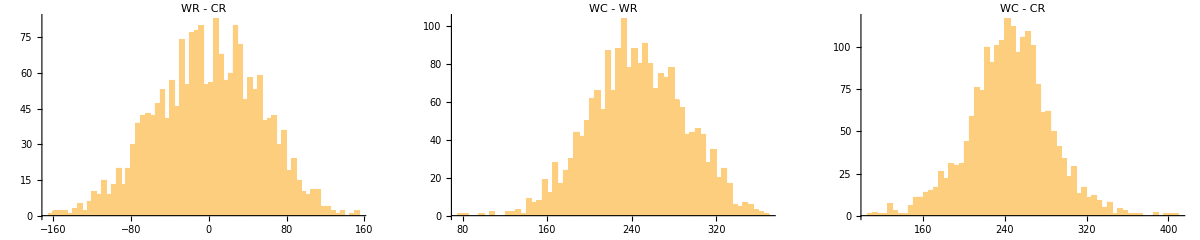

```mathematica
GraphicsGrid[{{WRvsCR,WCvsWR,WCvsCR}}]
```

## Bootstrapping

```mathematica
bootFiles=FileNames["*.csv","/home/alberto/Documents/Canids/2017-10-15_Admixture_project/Output_Stage_2/EAC/bootstrap"];
```

```mathematica
boots=Import[#,"TSV"]&/@bootFiles[[1;;2]];
```

```mathematica
bootsNOheader=Drop[boots[[#]],1]&/@Range[Length[boots]];
```

```mathematica
testinGroupBoots={#⟦4⟧,#⟦2⟧,#⟦1⟧,#⟦6⟧,#⟦5⟧,#⟦3⟧}&/@(Take[#,{6,12}]&/@bootsNOheader[[]]);
```

```mathematica
test=testinGroupBoots
```

{{1,1,0,0,0,0},{0,1,0,0,0,0},{3,1,2,0,0,0},{1,1,1,0,0,1},{0,0,2,1,0,0},{0,1,1,0,0,0},{0,0,0,3,0,0},{2,3,4,5,1,0},{0,0,3,3,0,1},{0,0,2,2,0,0},{2,1,0,0,3,4},{0,2,1,0,0,0},{0,0,2,0,0,0},{1,0,0,1,0,0},{0,0,0,0,0,3},{0,1,1,1,0,1},{1,0,0,0,0,0},{0,0,2,2,0,1},{0,1,3,0,1,0},{3,0,2,0,0,0},{0,1,2,1,0,0},{1,1,1,1,0,1},{0,0,1,1,0,0},{1,1,3,0,0,0},{1,1,2,0,1,1},{1,0,0,0,1,0},99948,{0,1,0,0,0,0},{1,1,1,2,0,0},{1,0,2,0,0,0},{0,1,2,0,0,0},{1,0,1,2,0,0},{0,0,1,0,0,0},{0,1,0,0,0,0},{0,1,2,1,0,0},{0,0,1,0,0,0},{0,2,0,1,0,0},{0,0,0,0,0,0},{1,0,1,1,0,1},{0,0,1,0,1,0},{1,1,1,1,0,0},{0,1,1,0,1,0},{1,0,1,0,0,0},{1,0,0,0,0,0},{0,1,0,0,0,0},{0,1,4,4,0,0},{1,0,1,0,0,0},{0,0,0,3,0,0},{1,3,2,1,0,0},{3,0,0,0,1,3},{2,1,0,0,0,2},{1,1,4,0,0,0},{2,1,1,0,0,0}}
 |  |  |  |

```mathematica
testcountsBoots=configCounts[testinGroupBoots[[#]],3]&/@Range[Length[testinGroupBoots]]
```

{SparseArray[…],SparseArray[…]}

```mathematica
Length[testinGroupBoots]
```

2